### Run

#### Get Capture Rate

```mathematica
PDict10GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicstallmasses[[1]],NuclearσDicstallmasses[[1]]]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 640.912, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 762.958, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
Keys@PDict10GeV
```

```mathematica
testpfs["PfNuc"][5,5]
```

Indeterminate

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

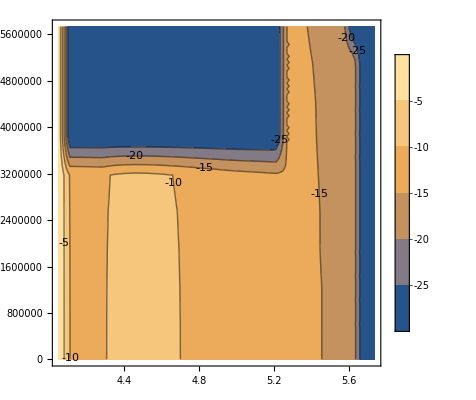

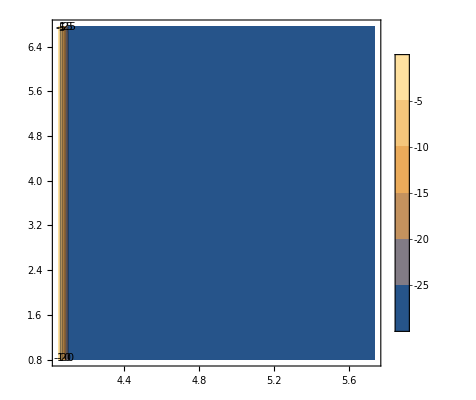

```mathematica
testpfs=InterpolatePc[PDict10GeV][[1]];
ContourPlot[("PfE"/.%)[vχ,Log10@bE],{vχ,("PfE"/.%)["Domain"][[1,1]],("PfE"/.%)["Domain"][[1,2]]},{bE,10^("PfE"/.%)["Domain"][[2,1]],10^("PfE"/.%)["Domain"][[2,2]]},ContourLabels->True,PlotRange->All,PlotLegends->Automatic]
ContourPlot[("PfNuc"/.%%)[vχ,bE],{vχ,("PfNuc"/.%%)["Domain"][[1,1]],("PfNuc"/.%%)["Domain"][[1,2]]},{bE,("PfNuc"/.%%)["Domain"][[2,1]],("PfNuc"/.%%)["Domain"][[2,2]]},ContourLabels->True,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
PDict1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[1]],ElectronicσDicstallmasses[[2]],NuclearσDicstallmasses[[2]]]
```

InterpolatingFunction::dmval: Input value {-26.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 342.925, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 375.952, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 644.162, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 748.219, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^8

20000

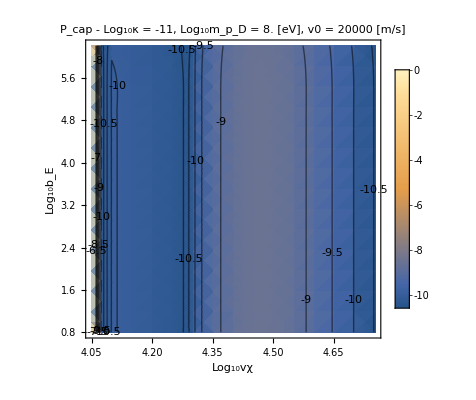

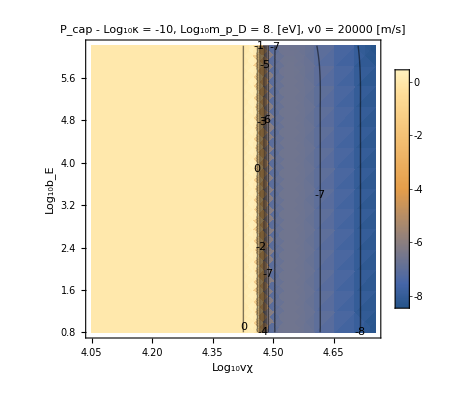

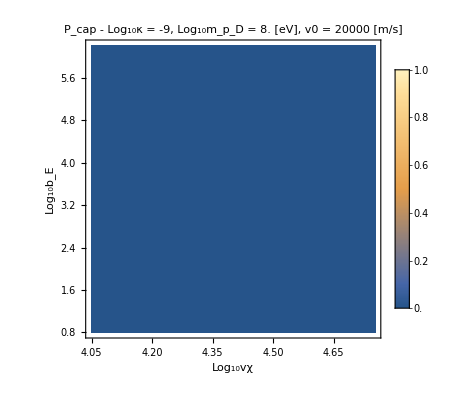

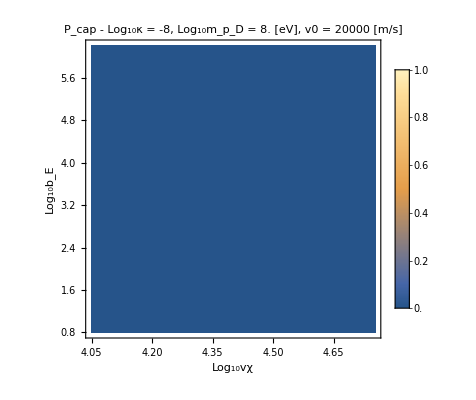

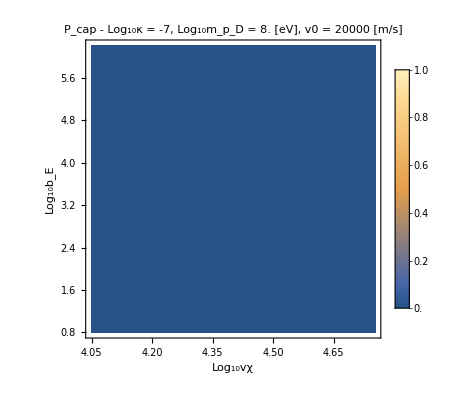

```mathematica
PDictp1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[2]]),κpoints, v0Points[[1]],ElectronicσDicstallmasses[[1]],NuclearσDicstallmasses[[1]]]
PlotPDist[PDictp1GeV]
```

```mathematica
PlotPDist[PDictp1GeV]
```

1.×10^8

20000

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPointPlot3D[Log10@{"vχE","κ","Pcap"}/.PDicttest]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Log10@{"vχE","bEarth","Pcap"}/.Gather[PDicttest,(#1["κ"]==#2["κ"])&]]
```

-Graphics3D-

1.×10^9

20000

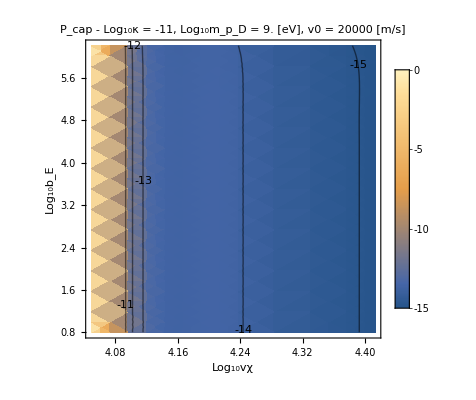

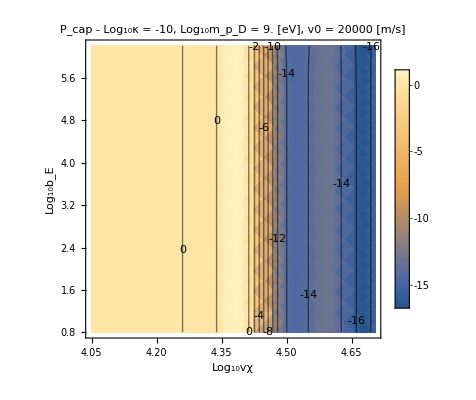

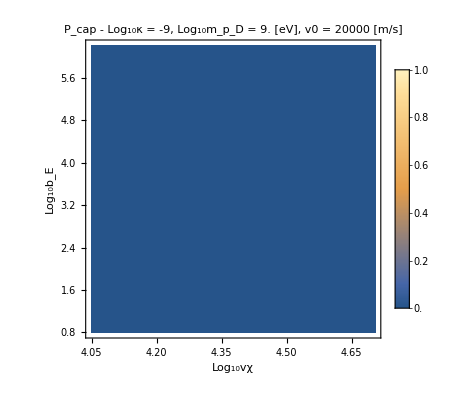

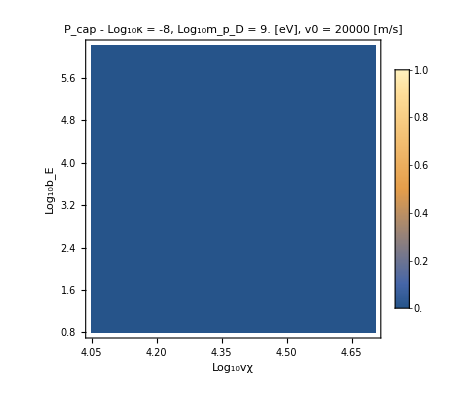

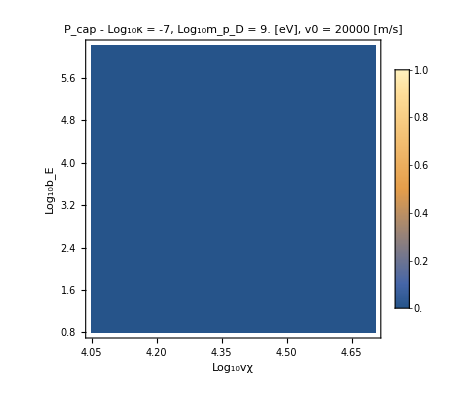

```mathematica
PlotPDist[PDicttest]
```

InterpolatingFunction::dmval: Input value {-25.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 579.033, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 633.18, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^10

20000

-Graphics-

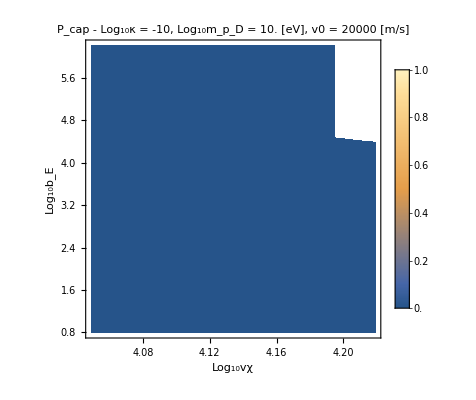

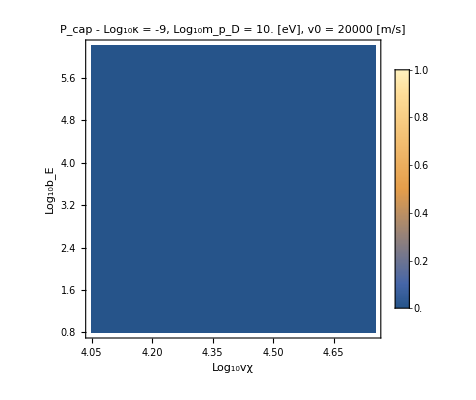

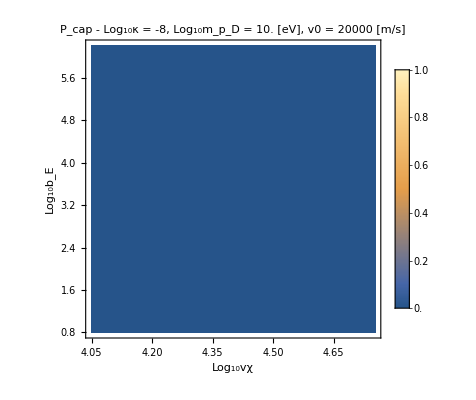

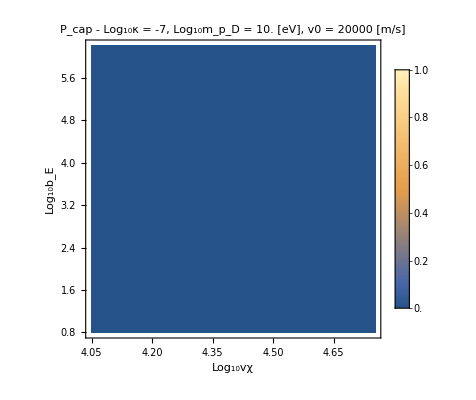

```mathematica
PDict10GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[2]]),κpoints, v0Points[[1]],ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]]
PlotPDist[PDict10GeV]
```

#### Scan over the masses 0.1 GeV to 10 GeV

switch to linear subdividing for impact parameter

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 573.809, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 614.262, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 658.83, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^8

20000

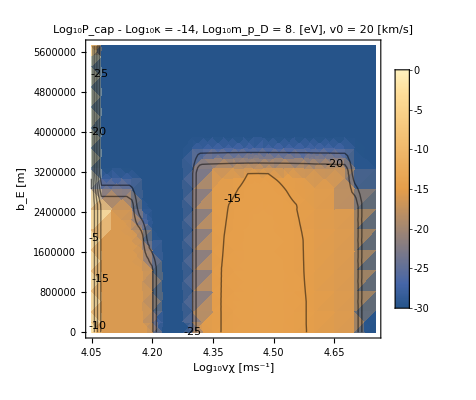

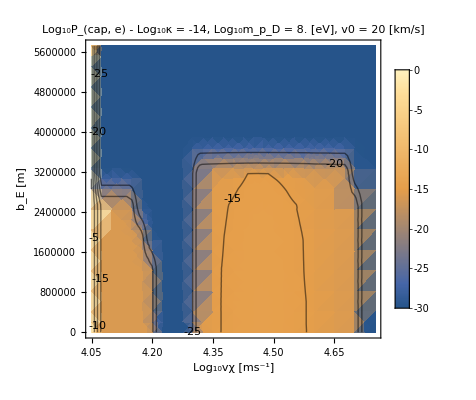

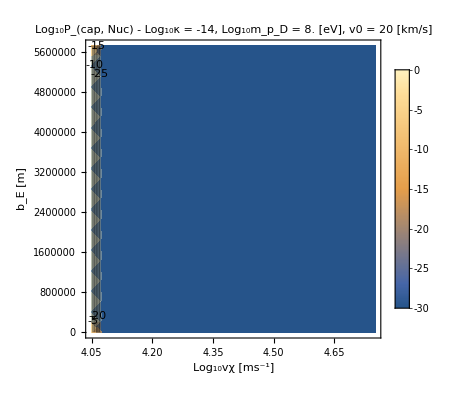

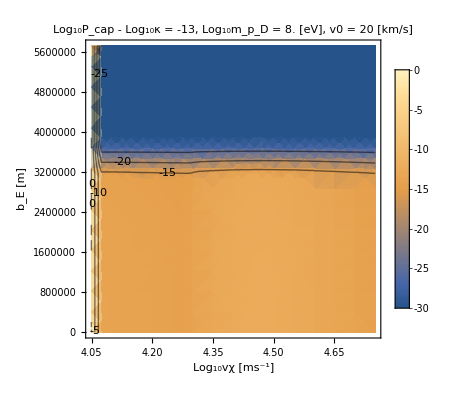

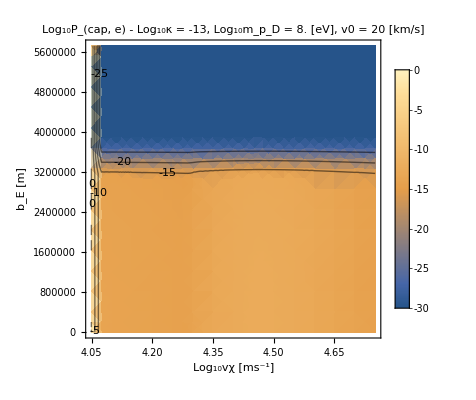

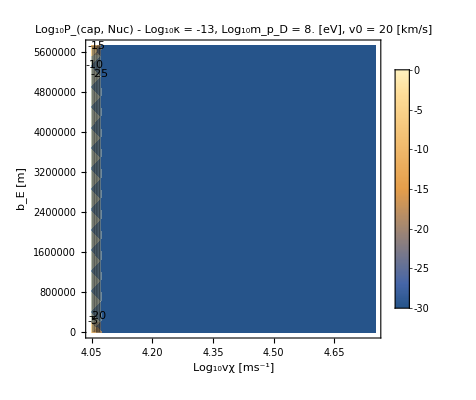

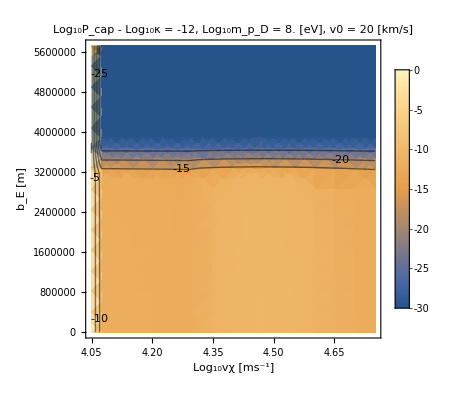

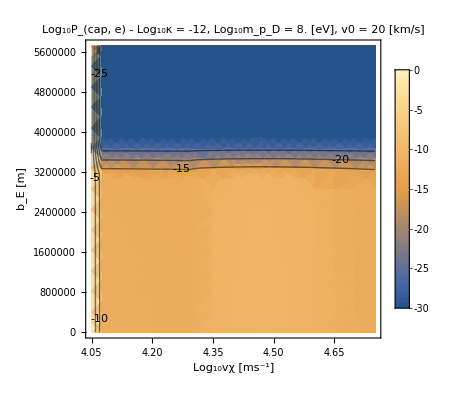

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 7.58756×10^35 and 1.50255×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

1.×10^8

220000

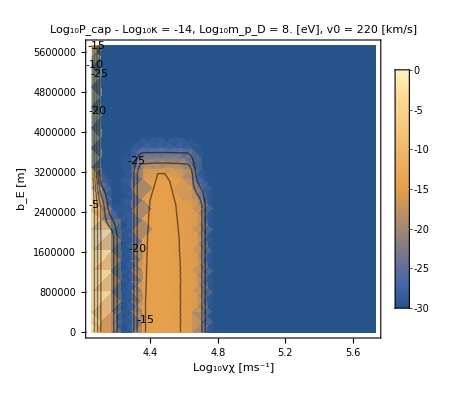

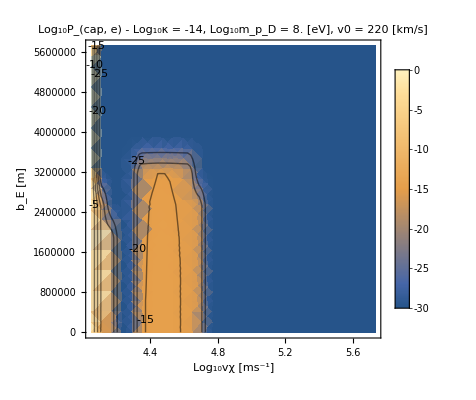

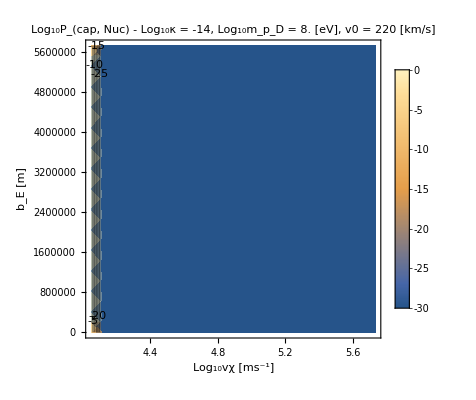

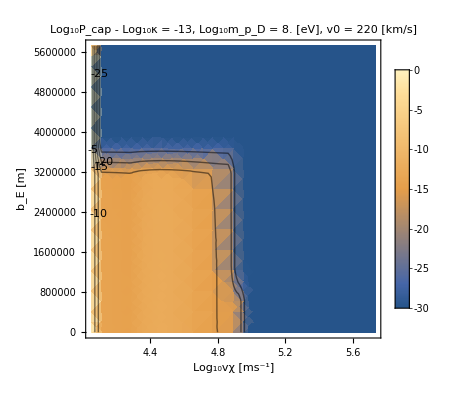

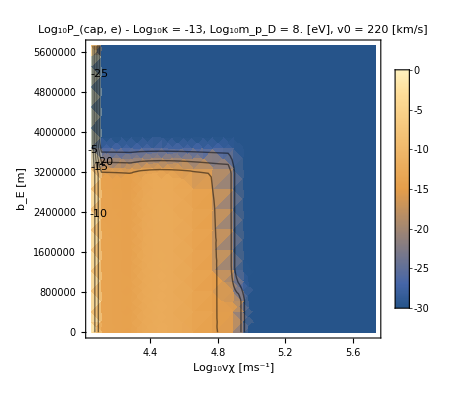

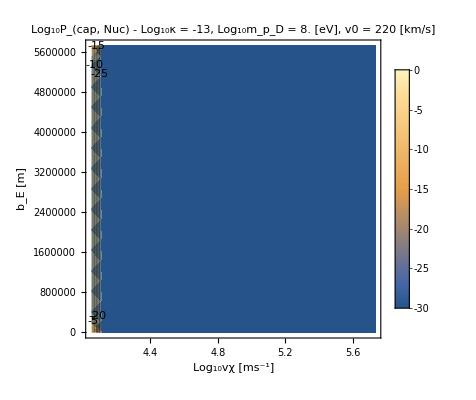

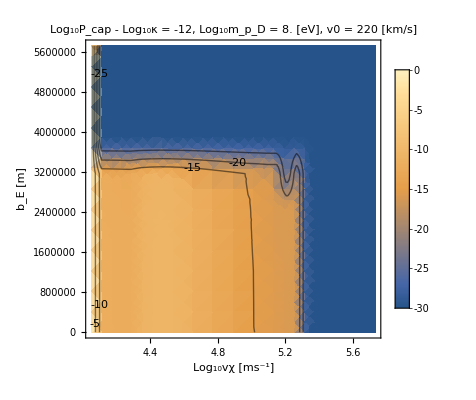

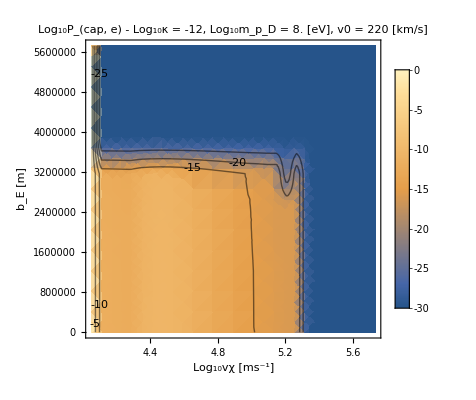

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21876.735141836}. NIntegrate obtained 3.04267×10^36 and 2.85934×10^33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {83774.4}. NIntegrate obtained 8.7922×10^38 and 1.4873×10^35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

1.×10^8

20000

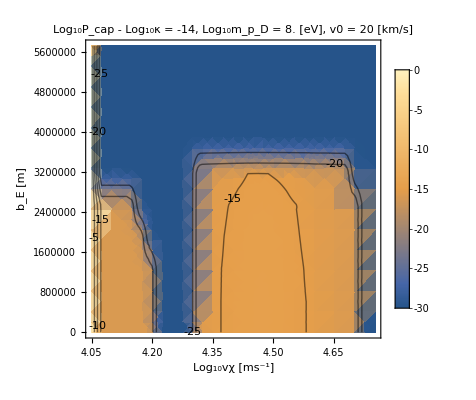

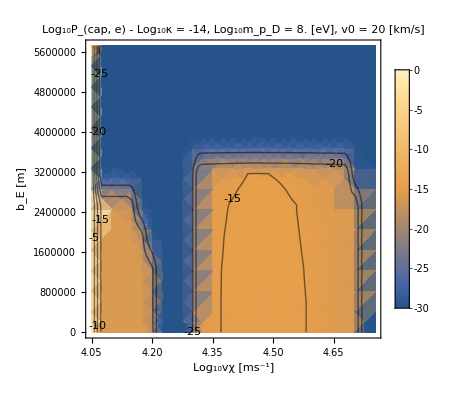

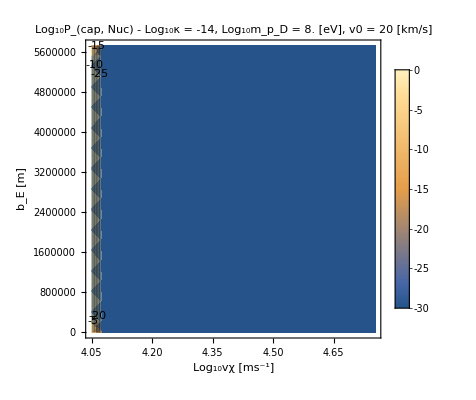

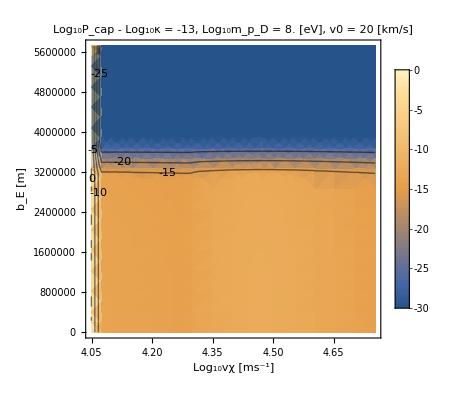

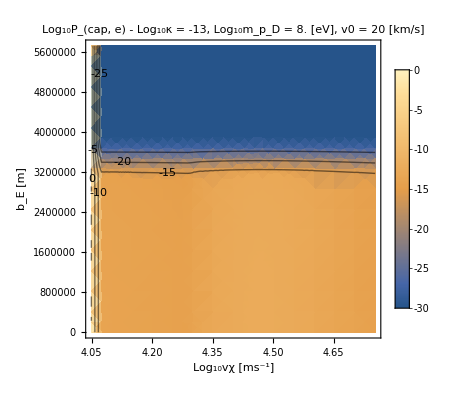

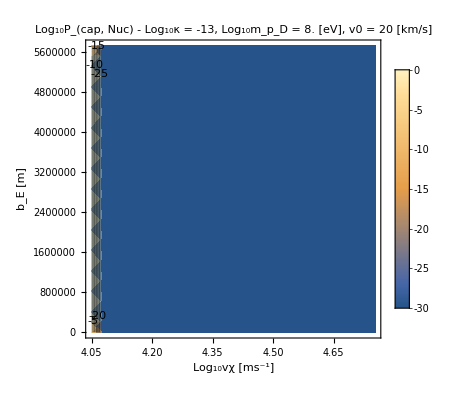

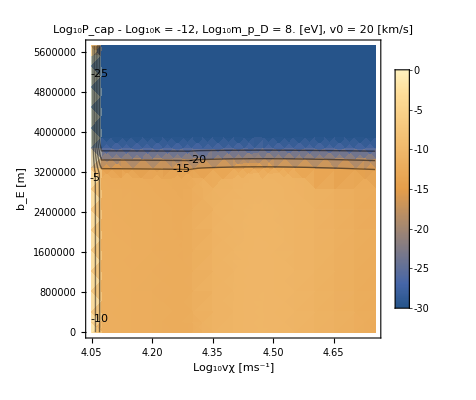

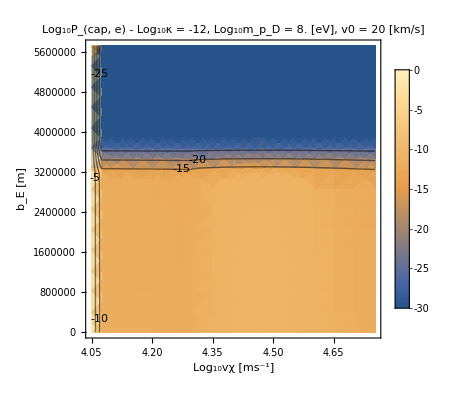

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

1.×10^8

220000

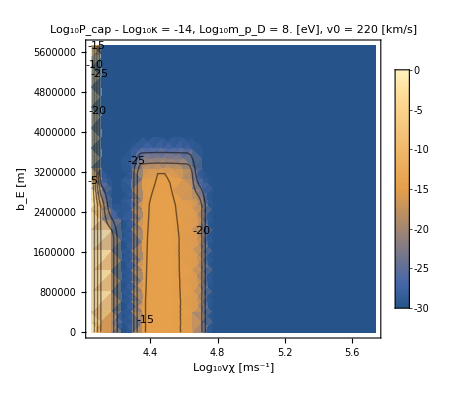

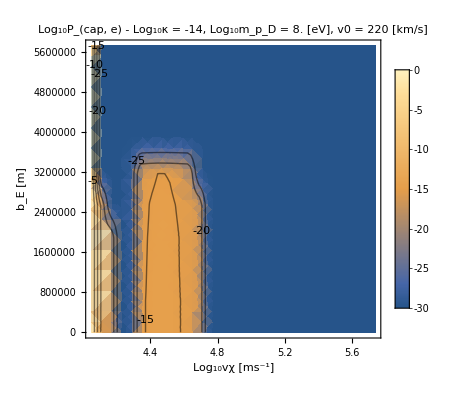

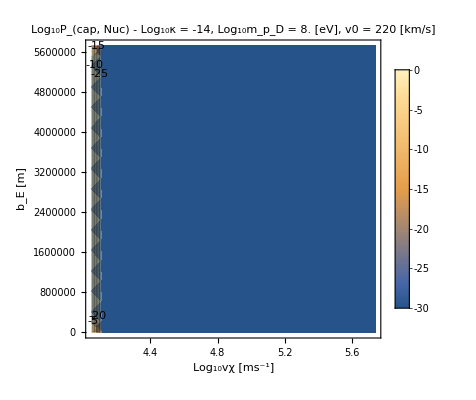

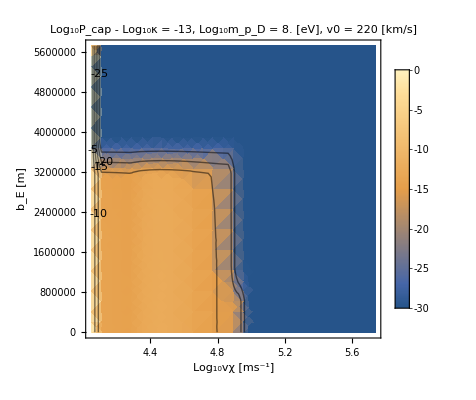

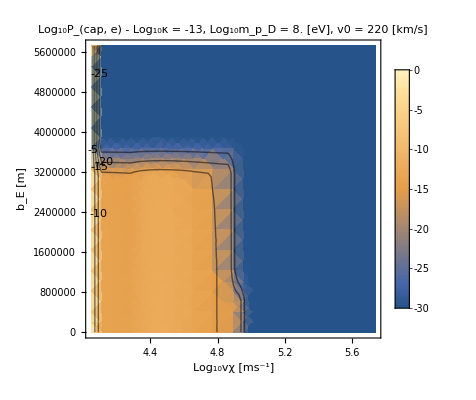

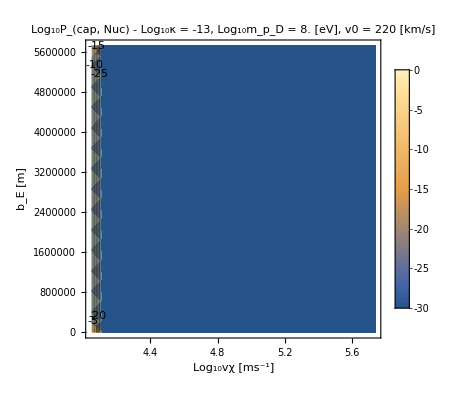

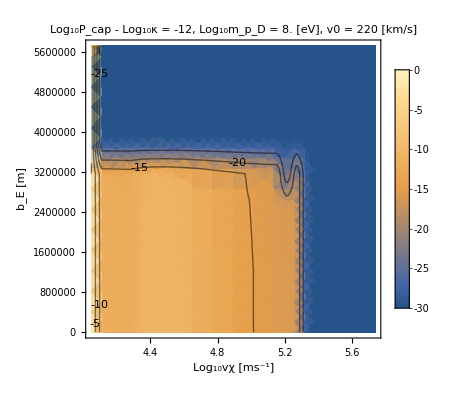

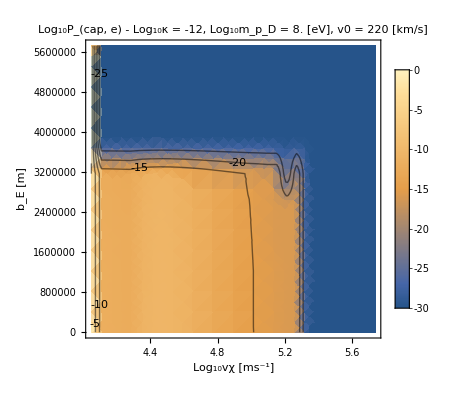

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.40135×10^15 nD,NcMax→8.94496×10^32 nD,timeenoughforequil→True,Nc→1.88789×10^27 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.25533×10^15 nD,NcMax→1.01383×10^33 nD,timeenoughforequil→True,Nc→2.13975×10^25 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70843×10^15 nD,NcMax→1.07714×10^33 nD,timeenoughforequil→True,Nc→2.27338×10^23 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.332×10^15 nD,NcMax→1.16428×10^33 nD,timeenoughforequil→True,Nc→2.45728×10^21 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.58018×10^18 nD,NcMax→9.19484×10^35 nD,timeenoughforequil→True,Nc→1.94063×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16375×10^13 nD,NcMax→1.62617×10^30 nD,timeenoughforequil→True,Nc→3.43215×10^24 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.31926×10^13 nD,NcMax→1.84347×10^30 nD,timeenoughforequil→True,Nc→3.89077×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.40276×10^13 nD,NcMax→1.96015×10^30 nD,timeenoughforequil→True,Nc→4.13703×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.51821×10^13 nD,NcMax→2.12148×10^30 nD,timeenoughforequil→True,Nc→4.47753×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.9825×10^16 nD,NcMax→2.77025×10^33 nD,timeenoughforequil→True,Nc→5.8468×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72868×10^18 nD,NcMax→8.005×10^35 nD,timeenoughforequil→True,Nc→1.68951×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.43694×10^19 nD,NcMax→6.19998×10^36 nD,timeenoughforequil→True,Nc→1.30855×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→1.31011×10^17 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.32425×10^15 nD,NcMax→8.83722×10^32 nD,timeenoughforequil→True,Nc→1.86516×10^27 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.16798×10^15 nD,NcMax→1.00162×10^33 nD,timeenoughforequil→True,Nc→2.11399×10^25 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.61556×10^15 nD,NcMax→1.06416×10^33 nD,timeenoughforequil→True,Nc→2.24599×10^23 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.23207×10^15 nD,NcMax→1.15031×10^33 nD,timeenoughforequil→True,Nc→2.42781×10^21 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.56612×10^18 nD,NcMax→9.1752×10^35 nD,timeenoughforequil→True,Nc→1.93649×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.1481×10^13 nD,NcMax→1.60431×10^30 nD,timeenoughforequil→True,Nc→3.386×10^24 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.30152×10^13 nD,NcMax→1.81868×10^30 nD,timeenoughforequil→True,Nc→3.83845×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.3839×10^13 nD,NcMax→1.93379×10^30 nD,timeenoughforequil→True,Nc→4.0814×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.49778×10^13 nD,NcMax→2.09293×10^30 nD,timeenoughforequil→True,Nc→4.41727×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.96087×10^16 nD,NcMax→2.74002×10^33 nD,timeenoughforequil→True,Nc→5.78301×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.71678×10^18 nD,NcMax→7.98836×10^35 nD,timeenoughforequil→True,Nc→1.686×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45846×10^19 nD,NcMax→6.23004×10^36 nD,timeenoughforequil→True,Nc→1.31489×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→1.31647×10^17 nD,Γtotal→3.39074×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictsp1GeVScan.dat

```mathematica
PDictsp1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[1]],NuclearσDicstallmasses[[1]]]
SaveIt[NotebookDirectory[]<>"PDictsp1GeVScan",PDictsp1GeVScan]
```

mpD: 1.×10^9

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^18

InterpolatingFunction::dmval: Input value {-26.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 266.296, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 310.188, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^9

20000

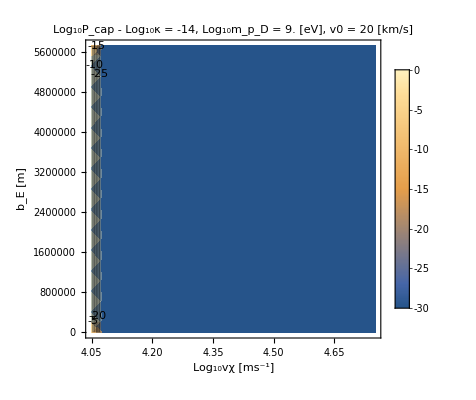

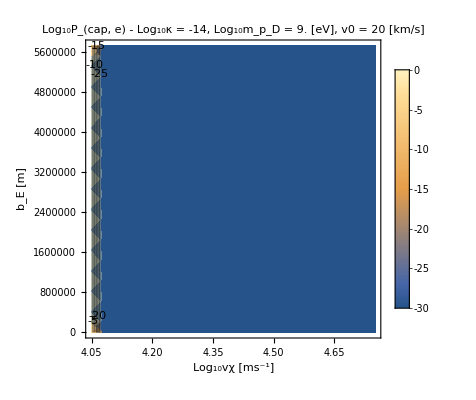

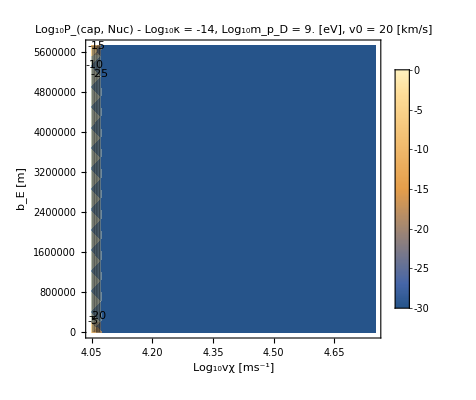

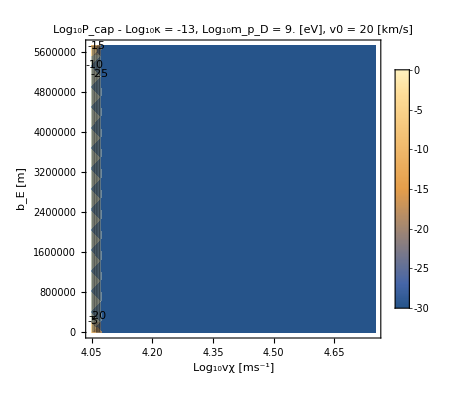

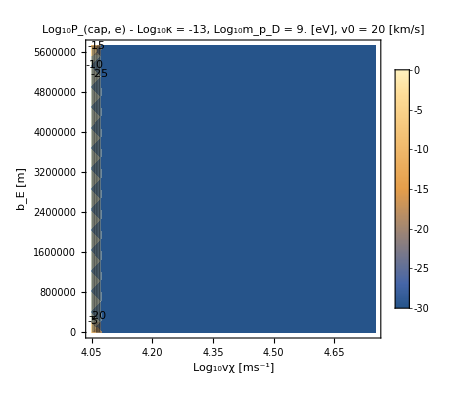

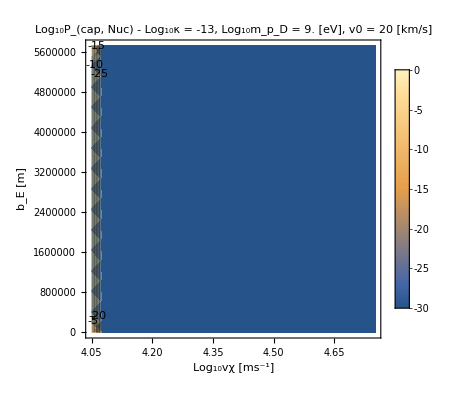

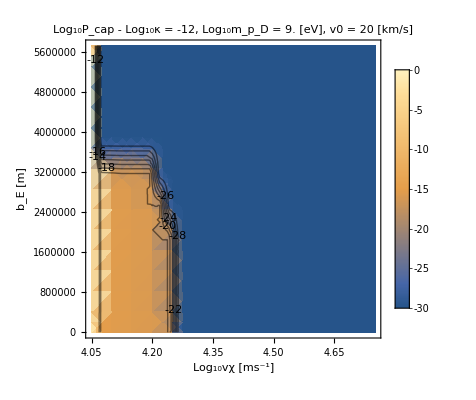

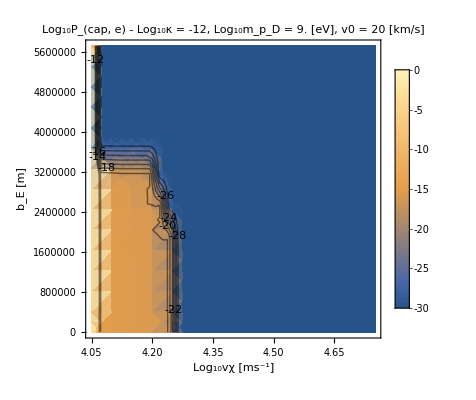

-Graphics-

-Graphics-

-Graphics-

«10 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {11852.68174912479798877029679715633392333984375}. NIntegrate obtained 1.04739×10^34 and 1.41715×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 7.53436×10^35 and 1.62816×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^16

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21876.735141836}. NIntegrate obtained 3.01726×10^36 and 1.75059×10^33 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^18

1.×10^9

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^16

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→2.96325×10^27 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→2.96325×10^25 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.04911×10^15 nD,NcMax→9.8501×10^32 nD,timeenoughforequil→True,Nc→3.64739×10^23 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.08331×10^16 nD,NcMax→1.26926×10^34 nD,timeenoughforequil→True,Nc→4.69994×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.53404×10^18 nD,NcMax→9.13037×10^35 nD,timeenoughforequil→True,Nc→3.38088×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→5.38095×10^24 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→5.38095×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.27666×10^13 nD,NcMax→1.78395×10^30 nD,timeenoughforequil→True,Nc→6.60578×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.34812×10^13 nD,NcMax→1.8838×10^30 nD,timeenoughforequil→True,Nc→6.9755×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.96594×10^16 nD,NcMax→2.74711×10^33 nD,timeenoughforequil→True,Nc→1.01723×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.10045×10^18 nD,NcMax→2.93507×10^35 nD,timeenoughforequil→True,Nc→1.08682×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.8794×10^19 nD,NcMax→5.4209×10^36 nD,timeenoughforequil→True,Nc→2.0073×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→2.29852×10^17 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→2.92755×10^27 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→2.92755×10^25 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.96423×10^15 nD,NcMax→9.73149×10^32 nD,timeenoughforequil→True,Nc→3.60347×10^23 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.98255×10^16 nD,NcMax→1.25518×10^34 nD,timeenoughforequil→True,Nc→4.6478×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.51963×10^18 nD,NcMax→9.11024×10^35 nD,timeenoughforequil→True,Nc→3.37342×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→5.30858×10^24 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→5.30858×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.2595×10^13 nD,NcMax→1.75996×10^30 nD,timeenoughforequil→True,Nc→6.51696×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.32998×10^13 nD,NcMax→1.85846×10^30 nD,timeenoughforequil→True,Nc→6.88167×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.94443×10^16 nD,NcMax→2.71705×10^33 nD,timeenoughforequil→True,Nc→1.0061×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.08999×10^18 nD,NcMax→2.92046×10^35 nD,timeenoughforequil→True,Nc→1.08141×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.8947×10^19 nD,NcMax→5.44228×10^36 nD,timeenoughforequil→True,Nc→2.01522×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→2.30969×10^17 nD,Γtotal→1.93265×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

```mathematica
PDicts1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[2]],NuclearσDicstallmasses[[2]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan]
```

```mathematica
PDicts10GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]]
SaveIt[NotebookDirectory[]<>"PDicts10GeVScan",PDicts10GeVScan]
```

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

InterpolatingFunction::dmval: Input value {-25.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 552.648, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 642.207, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^10

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14811.1}. NIntegrate obtained 2.78284×10^35 and 1.04943×10^32 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

1.×10^10

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 2.44235×10^23 and 2.56309×10^18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 2.62377×10^25 and 2.41453×10^20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^17

1.×10^10

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^15

1.×10^10

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^31 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^29 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^27 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.41337×10^18 nD,NcMax→3.37233×10^35 nD,timeenoughforequil→True,Nc→3.17155×10^26 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77664×10^18 nD,NcMax→1.08667×10^36 nD,timeenoughforequil→True,Nc→1.02197×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.022×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.022×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1591.35 nD,NcMax→2.22368×10^20 nD,timeenoughforequil→True,Nc→2.09129×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→170956. nD,NcMax→2.38886×10^22 nD,timeenoughforequil→True,Nc→2.24663×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.71628×10^7 nD,NcMax→2.39825×10^24 nD,timeenoughforequil→True,Nc→2.25546×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.72877×10^9 nD,NcMax→2.4157×10^26 nD,timeenoughforequil→True,Nc→2.27187×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.33694×10^15 nD,NcMax→3.26553×10^32 nD,timeenoughforequil→True,Nc→3.07111×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.00616×10^17 nD,NcMax→4.20067×10^34 nD,timeenoughforequil→True,Nc→3.95058×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.65712×10^19 nD,NcMax→2.31558×10^36 nD,timeenoughforequil→True,Nc→2.17772×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44204×10^19 nD,NcMax→6.20711×10^36 nD,timeenoughforequil→True,Nc→5.83755×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^31 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^29 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^27 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.39429×10^18 nD,NcMax→3.34567×10^35 nD,timeenoughforequil→True,Nc→3.14648×10^26 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.7779×10^18 nD,NcMax→1.08685×10^36 nD,timeenoughforequil→True,Nc→1.02214×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.02217×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.02217×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1657.76 nD,NcMax→2.31648×10^20 nD,timeenoughforequil→True,Nc→2.17857×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→179489. nD,NcMax→2.5081×10^22 nD,timeenoughforequil→True,Nc→2.35877×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.80108×10^7 nD,NcMax→2.51674×10^24 nD,timeenoughforequil→True,Nc→2.3669×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.81442×10^9 nD,NcMax→2.53539×10^26 nD,timeenoughforequil→True,Nc→2.38444×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.30762×10^15 nD,NcMax→3.22456×10^32 nD,timeenoughforequil→True,Nc→3.03257×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.9867×10^17 nD,NcMax→4.17347×10^34 nD,timeenoughforequil→True,Nc→3.92499×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.65846×10^19 nD,NcMax→2.31746×10^36 nD,timeenoughforequil→True,Nc→2.17949×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46364×10^19 nD,NcMax→6.23728×10^36 nD,timeenoughforequil→True,Nc→5.86593×10^21 nD,Γtotal→7.60943×10^11|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10GeVScan.dat

```mathematica
PDictsp1GeVScan[[1]][[1]]
LogPlot[v^2 E^(-"βD"("mpD")/2(v^2+("vesc")^2))/.Constants`EarthRepl/.%,{v,("vesc"/.Constants`EarthRepl),10^5},PlotRange->All]
```

<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,dNcMaxdt→4.45404×10^14 nD,NcMax→6.22387×10^31 nD,timeenoughforequil→True,Nc→0.0131359 nD,Γtotal→3.39074×10^16|>

-Graphics-

#### Scan over the masses 0.1 GeV to 10 GeV

switch to linear subdividing for impact parameter

```mathematica
PDictsp1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[1]],NuclearσDicstallmasses[[1]]]
SaveIt[NotebookDirectory[]<>"PDictsp1GeVScan",PDictsp1GeVScan]
```

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.20072×10^19 and 5.17388×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.68229×10^21 and 1.33179×10^16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 3.67963×10^23 and 2.19652×10^18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→277.577 nD,NcMax→3.87873×10^19 nD,timeenoughforequil→True,Nc→8.18632×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→31934. nD,NcMax→4.46231×10^21 nD,timeenoughforequil→True,Nc→9.41801×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.1911×10^6 nD,NcMax→4.45909×10^23 nD,timeenoughforequil→True,Nc→9.41121×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.19053×10^8 nD,NcMax→4.45829×10^25 nD,timeenoughforequil→True,Nc→9.40953×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.59255×10^17 nD,NcMax→2.22536×10^34 nD,timeenoughforequil→True,Nc→4.69677×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→46.227 nD,NcMax→6.45955×10^18 nD,timeenoughforequil→True,Nc→1.36333×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5171.12 nD,NcMax→7.22589×10^20 nD,timeenoughforequil→True,Nc→1.52507×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→520996. nD,NcMax→7.28017×10^22 nD,timeenoughforequil→True,Nc→1.53653×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.21234×10^7 nD,NcMax→7.28349×10^24 nD,timeenoughforequil→True,Nc→1.53723×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.59119×10^13 nD,NcMax→3.62081×10^30 nD,timeenoughforequil→True,Nc→7.64196×10^16 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.6767×10^17 nD,NcMax→1.21244×10^35 nD,timeenoughforequil→True,Nc→2.55894×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.55409×10^19 nD,NcMax→4.96633×10^36 nD,timeenoughforequil→True,Nc→1.04818×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→1.31009×10^17 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→281.798 nD,NcMax→3.93772×10^19 nD,timeenoughforequil→True,Nc→8.31082×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→32461.7 nD,NcMax→4.53605×10^21 nD,timeenoughforequil→True,Nc→9.57364×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24543×10^6 nD,NcMax→4.53502×10^23 nD,timeenoughforequil→True,Nc→9.57147×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24486×10^8 nD,NcMax→4.53423×10^25 nD,timeenoughforequil→True,Nc→9.56979×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.57936×10^17 nD,NcMax→2.20693×10^34 nD,timeenoughforequil→True,Nc→4.65788×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→45.2265 nD,NcMax→6.31975×10^18 nD,timeenoughforequil→True,Nc→1.33383×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5093.67 nD,NcMax→7.11766×10^20 nD,timeenoughforequil→True,Nc→1.50223×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→513027. nD,NcMax→7.16881×10^22 nD,timeenoughforequil→True,Nc→1.51303×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13242×10^7 nD,NcMax→7.1718×10^24 nD,timeenoughforequil→True,Nc→1.51366×10^13 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.56916×10^13 nD,NcMax→3.59003×10^30 nD,timeenoughforequil→True,Nc→7.577×10^16 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.69059×10^17 nD,NcMax→1.21438×10^35 nD,timeenoughforequil→True,Nc→2.56304×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.57059×10^19 nD,NcMax→4.98938×10^36 nD,timeenoughforequil→True,Nc→1.05304×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→1.31646×10^17 nD,Γtotal→3.39074×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictsp1GeVScan.dat

```mathematica
PDicts1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[2]],NuclearσDicstallmasses[[2]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan]
```

Part::partd: Part specification ElectronicσDicstallmasses⟦2⟧ is longer than depth of object.

Part::partd: Part specification NuclearσDicstallmasses⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {ElectronicσDicstallmasses} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

mpD: 5.61798×10^35 (mχ/.ElectronicσDicstallmasses)

meD/mpD: 1/10000

v0: 20000

βD: 3/(200020000 (mχ/.ElectronicσDicstallmasses))

κ is: 1.×10^-14

ReplaceAll::reps: {ElectronicσDicstallmasses⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NuclearσDicstallmasses⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

Join::incpt: Incompatible elements in Join[{},<||>] cannot be joined.

κ is: 1.×10^-13

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll::argt will be suppressed during this calculation.

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

Join::incpt: Incompatible elements in Join[{},<||>,<||>] cannot be joined.

κ is: 1.×10^-12

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

Join::incpt: Incompatible elements in Join[{},<||>,<||>,<||>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

κ is: 1.×10^-11

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

κ is: 1.×10^-10

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

κ is: 1.×10^-9

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

κ is: 1.×10^-8

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

κ is: 1.×10^-7

mχ must be the same in all processes:ReplaceAll[mχ,ElectronicσDicstallmasses⟦2⟧,mχ,NuclearσDicstallmasses⟦2⟧]

Set::shape: Lists {mpD$122005,meD$122005,vχMax$122005,βD$122005,v0$122005} and Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>] are not the same shape.

Gather::list: List expected at position 1 in Gather[Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],#1[κ]==#2[κ]&].

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[Pcap]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapE]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapNuc]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Part::partd: Part specification Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$122004[vχ,Log10[bE]],{vχ,Pfunc$122004[Domain]⟦1,1⟧,Pfunc$122004[Domain]⟦1,2⟧},«5»,PlotLabel→Log_10P_cap - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],«11»[«1»]}].

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$122004[vχ,Log10[bE]],«6»,PlotLabel→Log_10P_(cap, e) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10\*…ptBox[\(m\), SubscriptBox[\(p\), \(D\)]]\)<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],«1»}].

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of DensityPlot::plln will be suppressed during this calculation.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of ContourPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$122004[vχ,Log10[bE]],«6»,PlotLabel→Log_10P_(cap, Nuc) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10…tBox[\(m\), SubscriptBox[\(p\), \(D\)]]\)<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],«1»}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Set::shape: Lists {mpD$122845,meD$122845,vχMax$122845,βD$122845,v0$122845} and Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>] are not the same shape.

Gather::list: List expected at position 1 in Gather[Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],#1[κ]==#2[κ]&].

NIntegrate::nlim: vχ = 10.^(Interpolation[{{0.434294 Log[«1»],0.434294 Log[«1»]},0.434294 Log[Pcap]}/.Join[{},<||>,<||>,<||>,<||>,<||>,<||>,<||>,<||>],InterpolationOrder→1.][Domain]⟦1,1⟧) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Part::pkspec1: The expression regionindex/.NuclearσDicstallmasses cannot be used as a part specification.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

Table::iterb: Iterator {vχ,Round[vχ/.vχ],11200} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-1/2 vT^2 {2.49694×10^20,1.32379×10^19}⟦regionindex/.NuclearσDicstallmasses⟧ (mN/.NuclearσDicstallmasses)) vT^2 Total[Table[((Plus[«2»]^3-Power[«2»]) vχ^2 ⅇ^(-Part[«2»] «1» «1» vχ^2) HeavisideTheta[(ωmaxNuc[«4»]&)[vχ]-(«1»&)[«1»]] (10^Re[ReplaceAll[«2»][«2»]]&)[vχ,(«2» mχ$123380 Plus[«2»]&)[vχ]])/(3 vT vχ),{vχ,Round[vχ/.vχ],11200}]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::span: (regionindex/.NuclearσDicstallmasses);;(regionindex/.NuclearσDicstallmasses) is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Piecewise::pairs: The first argument {{1,3.486×10^6<r≤6.371×10^6},{1,r<3.486×10^6},{1,r>6.371×10^6}}⟦(regionindex/.NuclearσDicstallmasses);;(regionindex/.NuclearσDicstallmasses)⟧ of Piecewise is not a list of pairs.

TerminatedEvaluation[RecursionLimit]

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

```mathematica
PDicts10GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]]
SaveIt[NotebookDirectory[]<>"PDicts10GeVScan",PDicts10GeVScan]
```

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^10

20000

{1.78×10^-26,1.78×10^-30,73429.,8.42612×10^17,20000}

{1.78×10^-26,1.78×10^-30,73429.,8.42612×10^17,20000}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21096.5}. NIntegrate obtained 2.89119×10^19 and 3.89795×10^15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19071.6}. NIntegrate obtained 3.62753×10^21 and 3.7853×10^17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19071.6}. NIntegrate obtained 3.62378×10^23 and 4.35087×10^19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

#### Scan over the masses 1 MeV, 10 MeV, 100 GeV, and 1 TeV

switch to linear subdividing for impact parameter

```mathematica
PDicts1MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[1]],NuclearσDicst10MeVto1TeV[[1]]]
SaveIt[NotebookDirectory[]<>"PDicts1MeVScan",PDicts1MeVScan]
Clear[PDicts1MeVScan]
```

mpD: 1.×10^6

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^21

InterpolatingFunction::dmval: Input value {-29.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 467.32, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 478.105, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 494.243, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^6

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17542.}. NIntegrate obtained 8.93885×10^34 and 1.23357×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16573.}. NIntegrate obtained 8.60512×10^35 and 2.89145×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^19

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {363736.}. NIntegrate obtained 3.15739×10^20 and 9.24472×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^21

1.×10^6

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^19

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.11712×10^15 nD,NcMax→1.56101×10^32 nD,timeenoughforequil→False,Nc→1.56101×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^30 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^28 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^26 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.75206×10^17 nD,NcMax→1.08324×10^35 nD,timeenoughforequil→True,Nc→1.50131×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.46263×10^18 nD,NcMax→1.04279×10^36 nD,timeenoughforequil→True,Nc→1.44526×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.05725 nD,NcMax→2.8747×10^17 nD,timeenoughforequil→False,Nc→2.8747×10^17 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→2.01403×10^29 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→2.01403×10^27 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45318×10^30 nD,timeenoughforequil→True,Nc→2.01404×10^25 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.04035×10^13 nD,NcMax→1.45374×10^30 nD,timeenoughforequil→True,Nc→2.01481×10^23 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.08043×10^13 nD,NcMax→1.50974×10^30 nD,timeenoughforequil→True,Nc→2.09242×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.93358×10^14 nD,NcMax→1.24834×10^32 nD,timeenoughforequil→True,Nc→1.73013×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→8.60309×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.10366×10^15 nD,NcMax→1.54221×10^32 nD,timeenoughforequil→False,Nc→1.54221×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^30 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^28 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^26 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70596×10^17 nD,NcMax→1.0768×10^35 nD,timeenoughforequil→True,Nc→1.49239×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.46486×10^18 nD,NcMax→1.04311×10^36 nD,timeenoughforequil→True,Nc→1.44569×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.82067 nD,NcMax→3.94148×10^17 nD,timeenoughforequil→False,Nc→3.94148×10^17 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.98694×10^29 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.98694×10^27 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02597×10^13 nD,NcMax→1.43364×10^30 nD,timeenoughforequil→True,Nc→1.98695×10^25 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02638×10^13 nD,NcMax→1.43421×10^30 nD,timeenoughforequil→True,Nc→1.98775×10^23 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.06742×10^13 nD,NcMax→1.49156×10^30 nD,timeenoughforequil→True,Nc→2.06723×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.55446×10^14 nD,NcMax→1.19536×10^32 nD,timeenoughforequil→True,Nc→1.65671×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→8.64491×10^23 nD,Γtotal→5.16352×10^9|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1MeVScan.dat

```mathematica
PDicts10MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[2]],NuclearσDicst10MeVto1TeV[[2]]]
SaveIt[NotebookDirectory[]<>"PDicts10MeVScan",PDicts10MeVScan]
Clear[PDicts10MeVScan]
```

mpD: 1.×10^7

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^20

InterpolatingFunction::dmval: Input value {-28.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^7

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21858.6}. NIntegrate obtained 8.56078×10^35 and 1.03503×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^18

1.×10^7

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {33625.1}. NIntegrate obtained 3.9926×10^37 and 2.99376×10^34 for the integral and error estimates.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^20

1.×10^7

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21915.4}. NIntegrate obtained 8.68405×10^35 and 1.472×10^31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^18

1.×10^7

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^29 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.42419×10^18 nD,NcMax→1.03742×10^36 nD,timeenoughforequil→True,Nc→1.15829×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.21331×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.21331×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→1.62248×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→1.62248×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45318×10^30 nD,timeenoughforequil→True,Nc→1.62249×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.04046×10^13 nD,NcMax→1.45389×10^30 nD,timeenoughforequil→True,Nc→1.62328×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.09103×10^13 nD,NcMax→1.52456×10^30 nD,timeenoughforequil→True,Nc→1.70218×10^19 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.60144×10^17 nD,NcMax→3.63513×10^34 nD,timeenoughforequil→True,Nc→4.05865×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.4391×10^19 nD,NcMax→6.20299×10^36 nD,timeenoughforequil→True,Nc→6.92569×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→6.93057×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^29 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.42063×10^18 nD,NcMax→1.03692×10^36 nD,timeenoughforequil→True,Nc→1.15774×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.21351×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.21351×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.60066×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.60066×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02597×10^13 nD,NcMax→1.43364×10^30 nD,timeenoughforequil→True,Nc→1.60067×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02648×10^13 nD,NcMax→1.43435×10^30 nD,timeenoughforequil→True,Nc→1.60147×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.07756×10^13 nD,NcMax→1.50573×10^30 nD,timeenoughforequil→True,Nc→1.68116×10^19 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.58139×10^17 nD,NcMax→3.60712×10^34 nD,timeenoughforequil→True,Nc→4.02738×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46063×10^19 nD,NcMax→6.23308×10^36 nD,timeenoughforequil→True,Nc→6.95929×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→6.96426×10^19 nD,Γtotal→6.40961×10^13|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10MeVScan.dat

```mathematica
PDicts100GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[-2]],NuclearσDicst10MeVto1TeV[[-2]]]
SaveIt[NotebookDirectory[]<>"PDicts100GeVScan",PDicts100GeVScan]
Clear[PDicts100GeVScan]
```

mpD: 1.×10^11

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^16

InterpolatingFunction::dmval: Input value {-24.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 227.038, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 263.158, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 305.122, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^11

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {11853.1740880435}. NIntegrate obtained 2.24234×10^34 and 2.25617×10^31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {24501.4}. NIntegrate obtained 8.35956×10^35 and 4.09971×10^30 for the integral and error estimates.

General::munfl: Exp[-1682.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1682.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1683.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^14

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 1.06876×10^32 and 8.22163×10^26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^16

1.×10^11

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^14

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.94463×10^17 nD,NcMax→2.71734×10^34 nD,timeenoughforequil→False,Nc→2.71734×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.24968×10^18 nD,NcMax→1.01304×10^36 nD,timeenoughforequil→False,Nc→1.01304×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.96367×10^11 nD,NcMax→9.73071×10^28 nD,timeenoughforequil→False,Nc→9.73071×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.9632×10^13 nD,NcMax→9.73006×10^30 nD,timeenoughforequil→False,Nc→9.73006×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.91681×10^15 nD,NcMax→9.66524×10^32 nD,timeenoughforequil→False,Nc→9.66524×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.1106×10^17 nD,NcMax→5.74397×10^34 nD,timeenoughforequil→False,Nc→5.74397×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.51189×10^18 nD,NcMax→2.11264×10^35 nD,timeenoughforequil→False,Nc→2.11264×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91243×10^18 nD,NcMax→4.0697×10^35 nD,timeenoughforequil→False,Nc→4.0697×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.03648×10^18 nD,NcMax→1.26272×10^36 nD,timeenoughforequil→False,Nc→1.26272×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.4422×10^19 nD,NcMax→6.20733×10^36 nD,timeenoughforequil→False,Nc→6.20733×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.92417×10^17 nD,NcMax→2.68874×10^34 nD,timeenoughforequil→False,Nc→2.68874×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.2422×10^18 nD,NcMax→1.01199×10^36 nD,timeenoughforequil→False,Nc→1.01199×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.24009×10^11 nD,NcMax→1.0117×10^29 nD,timeenoughforequil→False,Nc→1.0117×10^29 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.23962×10^13 nD,NcMax→1.01163×10^31 nD,timeenoughforequil→False,Nc→1.01163×10^31 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.19336×10^15 nD,NcMax→1.00517×10^33 nD,timeenoughforequil→False,Nc→1.00517×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.33145×10^17 nD,NcMax→6.05257×10^34 nD,timeenoughforequil→False,Nc→6.05257×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.60683×10^18 nD,NcMax→2.24531×10^35 nD,timeenoughforequil→False,Nc→2.24531×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.99909×10^18 nD,NcMax→4.19079×10^35 nD,timeenoughforequil→False,Nc→4.19079×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.228×10^18 nD,NcMax→1.28948×10^36 nD,timeenoughforequil→False,Nc→1.28948×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46379×10^19 nD,NcMax→6.2375×10^36 nD,timeenoughforequil→False,Nc→6.2375×10^36 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100GeVScan.dat

```mathematica
PDicts1TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[-1]],NuclearσDicst10MeVto1TeV[[-1]]]
SaveIt[NotebookDirectory[]<>"PDicts1TeVScan",PDicts1TeVScan]
Clear[PDicts1TeVScan]
```

mpD: 1.×10^12

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^15

InterpolatingFunction::dmval: Input value {-23.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 551.562, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 635.678, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^12

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14811.1}. NIntegrate obtained 3.36988×10^35 and 9.95499×10^31 for the integral and error estimates.

General::munfl: Exp[-25362.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25366.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25371.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^13

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14874.1790264059}. NIntegrate obtained 4.51491×10^35 and 2.79359×10^32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {43318.9}. NIntegrate obtained 5.86707×10^37 and 5.62905×10^34 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^15

1.×10^12

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^13

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.92247×10^18 nD,NcMax→4.08372×10^35 nD,timeenoughforequil→False,Nc→4.08372×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77669×10^18 nD,NcMax→1.08668×10^36 nD,timeenoughforequil→False,Nc→1.08668×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→64.4479 nD,NcMax→9.00565×10^18 nD,timeenoughforequil→False,Nc→9.00565×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→22463.1 nD,NcMax→3.13889×10^21 nD,timeenoughforequil→False,Nc→3.13889×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.2431×10^6 nD,NcMax→3.13441×10^23 nD,timeenoughforequil→False,Nc→3.13441×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.2418×10^8 nD,NcMax→3.13258×10^25 nD,timeenoughforequil→False,Nc→3.13258×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.20924×10^10 nD,NcMax→3.08709×10^27 nD,timeenoughforequil→False,Nc→3.08709×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.94176×10^15 nD,NcMax→4.11067×10^32 nD,timeenoughforequil→False,Nc→4.11067×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.82278×10^17 nD,NcMax→5.34177×10^34 nD,timeenoughforequil→False,Nc→5.34177×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.04209×10^19 nD,NcMax→2.85352×10^36 nD,timeenoughforequil→False,Nc→2.85352×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.8177×10^18 nD,NcMax→3.93733×10^35 nD,timeenoughforequil→False,Nc→3.93733×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77795×10^18 nD,NcMax→1.08685×10^36 nD,timeenoughforequil→False,Nc→1.08685×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→123.547 nD,NcMax→1.72639×10^19 nD,timeenoughforequil→False,Nc→1.72639×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→43207. nD,NcMax→6.03755×10^21 nD,timeenoughforequil→False,Nc→6.03755×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.31441×10^6 nD,NcMax→6.02875×10^23 nD,timeenoughforequil→False,Nc→6.02875×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.31139×10^8 nD,NcMax→6.02454×10^25 nD,timeenoughforequil→False,Nc→6.02454×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.1937×10^10 nD,NcMax→5.86008×10^27 nD,timeenoughforequil→False,Nc→5.86008×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.90691×10^15 nD,NcMax→4.06198×10^32 nD,timeenoughforequil→False,Nc→4.06198×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.64537×10^17 nD,NcMax→5.09388×10^34 nD,timeenoughforequil→False,Nc→5.09388×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.93448×10^19 nD,NcMax→2.70316×10^36 nD,timeenoughforequil→False,Nc→2.70316×10^36 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1TeVScan.dat

#### Get Plots for Pcap E and Nuc

```mathematica
"mχ"("c")^2/("JpereV")/.ElectronicσDicst10MeVto1TeV[[3]]/.Constants`SIConstRepl
```

{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8}

```mathematica
PDict1MeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[1]],NuclearσDicst10MeVto1TeV[[1]]]
PlotPDist[PDict1MeV]
```

InterpolatingFunction::dmval: Input value {-29.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 471.036, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 467.725, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 511.325, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDictp1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[3]],NuclearσDicst10MeVto1TeV[[3]]]
PlotPDist[PDictp1GeV]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 640.912, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 762.958, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^8

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[4]],NuclearσDicst10MeVto1TeV[[4]]]
PlotPDist[PDict1GeV]
```

InterpolatingFunction::dmval: Input value {-26.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 340.432, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 491.321, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict100GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[6]],NuclearσDicst10MeVto1TeV[[6]]]
PlotPDist[PDict100GeV]
```

InterpolatingFunction::dmval: Input value {-24.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 305.666, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 436.713, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::munfl: Exp[-3360.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3360.63] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict1TeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[7]],NuclearσDicst10MeVto1TeV[[7]]]
PlotPDist[PDict1TeV]
```

InterpolatingFunction::dmval: Input value {-23.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 551.562, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 776.104, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::munfl: Exp[-26086.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26137.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

#### Hard Scatter Regime

```mathematica
PlotPDist[PDict1MeV]
```

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PlotPDist[PDict1GeV]
```

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PlotPDist[PDict1TeV]
```

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

### Scrap

#### Unit Test get trajectory

```mathematica
Plot[ELEarthTot[r,"mpD"/.mpDPoints[[1]],v0Points[[1]]]/.r->rt,{rt,1,"rE"/.Constants`EarthRepl}]
```

InterpolatingFunction::dmval: Input value {-27.7496,Log[20000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
?ΔrAveragedTot0
```

```mathematica
REt=dE[(("rE")/2/.Constants`EarthRepl)]/2
s=NDSolve[{D[l[t],{t,2}]==0,l'[0]==v0Points[[1]],l[0]==-REt,WhenEvent[l[t]==REt,"StopIntegration"]},l,{t,0,10^4}][[1]]
(l/.s)["Methods"]
(l/.s)["Domain"]
Plot[l'[t]/.s,{t,0,%[[1,2]]}]

Plot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2)/.s,{t,0,%%[[1,2]]}]
```

5.51745×10^6

{l→InterpolatingFunction[…]}

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

{{0.,551.745}}

-Graphics-

-Graphics-

1.10349×10^7

```mathematica
REt=dE[(("rE")/2/.Constants`EarthRepl)]/2
s=NDSolve[{D[l[t],{t,2}]==-((10^-10.5)^2("JpereV"/.Constants`SIConstRepl))/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2),"mpD"/.mpDPoints[[1]],D[l[t],t]],l'[0]==v0Points[[1]],l[0]==-REt,WhenEvent[l[t]==REt,"StopIntegration"]},l,{t,0,10^4}][[1]]
ldom=(l/.s)["Domain"]
Plot[l[t]/.s,{t,0,ldom[[1,2]]}]
Plot[l'[t]/.s,{t,0,ldom[[1,2]]}]
Plot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2)/.s,{t,0,ldom[[1,2]]}]
Plot[-((10^-10.5)^2("JpereV"/.Constants`SIConstRepl))/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t]/.s)^2),"mpD"/.mpDPoints[[1]],Abs[(l'[t]/.s)]],{t,0,ldom[[1,2]]}]
```

5.51745×10^6

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{l→InterpolatingFunction[…]}

{{0.,575.021}}

-Graphics-

-Graphics-

-Graphics-

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
(l/.s)[]
```

-5.571×10^6

```mathematica
-((10^-9)^2"JpereV"/.SIConstRepl)/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2),"mpD"/.mpDPoints[[1]],Abs[20000]]
```

InterpolatingFunction::dmval: Input value {-27.7496,Log[20000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

-4104.53

```mathematica
"rE"-"rcore"/.EarthRepl
```

2.885×10^6

```mathematica
√((("rE")/2/.Constants`EarthRepl)^2+(600000)^2)
```

3.24151×10^6

```mathematica
lDict=GetWeakCaptureTrajectory["mpD"/.mpDPoints[[1]],v0Points[[1]],(("rE")/2/.Constants`EarthRepl),10^-10.5]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

#### Unit Test Get weak capture probability

```mathematica
lDict=GetWeakCaptureTrajectory["mpD"/.mpDPoints[[1]],v0Points[[1]],(("rE")/2/.Constants`EarthRepl),10^-10.5]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

```mathematica
("l(t)"/.lDict)[400]
("v(t)"/.lDict)[400]
```

2.26501×10^6

18794.

```mathematica
("dσf"/.FeσDictemep1GeV[[2]])[4,]
```

InterpolatingFunction[…][4]

```mathematica
"ωmin"/.FeσDictemep1GeV[[2]]
ξofωandvχ[10%,%,("v(t)"/.lDict)[t],"mpD"/.mpDPoints[[1]],SIConstRepl]/.t->300
Re@("dσf"/.FeσDictemep1GeV[[2]])[Log10[("v(t)"/.lDict)[t]],Log10@ξofωandvχ[10%%,%%,("v(t)"/.lDict)[t],"mpD"/.mpDPoints[[1]],SIConstRepl]]/.t->300
```

6.5887×10^12

0.196182

-1.43955

```mathematica
"ξ"/.FeσDictemep1GeV[[2]]
```

{-4,-Log[10000/9999]/Log[10]}

```mathematica
Integrate["dσf"/.FeσDictemep1GeV[[2]] ]
```

```mathematica
lDict
```

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

```mathematica
(10^("ξ")/.FeσDictemep1GeV[[2]])[[1]]
```

1/10000

```mathematica
GetWeakCaptureProbability[lDict,FeσDictemep1GeV[[2]]]
```

<|SurvivalProb→1.,CaptureProb→1.26121×10^-13|>

```mathematica
GetWeakCaptureProbability[lDict,FeσDictemep1GeV[[2]]]
```

<|SurvivalProb→1.,CaptureProb→1.26121×10^-13|>

```mathematica
GetWeakCaptureProbability[lDict,Fe2eDictUnitTest]
```

3.16228×10^-11

1.91532×10^29

-Graphics-

-Graphics-

2 (3.51912×10^12 10^Re[σofξf[4.26419,-0.0000581831]]+3.52005×10^12 10^Re[σofξf[4.26431,-0.0000581751]]+3.52098×10^12 10^Re[σofξf[4.26442,-0.0000581671]]+3.52192×10^12 10^Re[σofξf[4.26454,-0.0000581591]]+3.52285×10^12 10^Re[σofξf[4.26465,-0.0000581511]]+3.52378×10^12 10^Re[σofξf[4.26477,-0.0000581431]]+3.52472×10^12 10^Re[σofξf[4.26488,-0.0000581351]]+3.52565×10^12 10^Re[σofξf[4.265,-0.0000581272]]+3.52658×10^12 10^Re[σofξf[4.26511,-0.0000581192]]+3.52751×10^12 10^Re[σofξf[4.26523,-0.0000581113]]+3.52844×10^12 10^Re[σofξf[4.26534,-0.0000581034]]+3.52938×10^12 10^Re[σofξf[4.26546,-0.0000580954]]+3.53031×10^12 10^Re[σofξf[4.26557,-0.0000580875]]+3.53124×10^12 10^Re[σofξf[4.26569,-0.0000580796]]+3.53217×10^12 10^Re[σofξf[4.2658,-0.0000580717]]+3.5331×10^12 10^Re[σofξf[4.26591,-0.0000580638]]+3.53403×10^12 10^Re[σofξf[4.26603,-0.0000580559]]+3.53496×10^12 10^Re[σofξf[4.26614,-0.000058048]]+3.53589×10^12 10^Re[σofξf[4.26626,-0.0000580402]]+3.53682×10^12 10^Re[σofξf[4.26637,-0.0000580323]]+3.53775×10^12 10^Re[σofξf[4.26649,-0.0000580244]]+3.53868×10^12 10^Re[σofξf[4.2666,-0.0000580166]]+3.53961×10^12 10^Re[σofξf[4.26671,-0.0000580088]]+3.54054×10^12 10^Re[σofξf[4.26683,-0.0000580009]]+3.54147×10^12 10^Re[σofξf[4.26694,-0.0000579931]]+3.5424×10^12 10^Re[σofξf[4.26706,-0.0000579853]]+3.54333×10^12 10^Re[σofξf[4.26717,-0.0000579775]]+3.54426×10^12 10^Re[σofξf[4.26728,-0.0000579697]]+3.54519×10^12 10^Re[σofξf[4.2674,-0.0000579619]]+3.54611×10^12 10^Re[σofξf[4.26751,-0.0000579541]]+3.54704×10^12 10^Re[σofξf[4.26762,-0.0000579463]]+3.54797×10^12 10^Re[σofξf[4.26774,-0.0000579386]]+3.5489×10^12 10^Re[σofξf[4.26785,-0.0000579308]]+3.54983×10^12 10^Re[σofξf[4.26797,-0.000057923]]+3.55075×10^12 10^Re[σofξf[4.26808,-0.0000579153]]+3.55168×10^12 10^Re[σofξf[4.26819,-0.0000579076]]+3.55261×10^12 10^Re[σofξf[4.26831,-0.0000578998]]+3.55353×10^12 10^Re[σofξf[4.26842,-0.0000578921]]+3.55446×10^12 10^Re[σofξf[4.26853,-0.0000578844]]+3.55539×10^12 10^Re[σofξf[4.26865,-0.0000578767]]+3.55631×10^12 10^Re[σofξf[4.26876,-0.000057869]]+3.55724×10^12 10^Re[σofξf[4.26887,-0.0000578613]]+3.55817×10^12 10^Re[σofξf[4.26898,-0.0000578536]]+3.55909×10^12 10^Re[σofξf[4.2691,-0.0000578459]]+3.56002×10^12 10^Re[σofξf[4.26921,-0.0000578383]]+3.56094×10^12 10^Re[σofξf[4.26932,-0.0000578306]]+3.56187×10^12 10^Re[σofξf[4.26944,-0.000057823]]+3.56279×10^12 10^Re[σofξf[4.26955,-0.0000578153]]+3.56372×10^12 10^Re[σofξf[4.26966,-0.0000578077]]+3.56464×10^12 10^Re[σofξf[4.26977,-0.0000578]]+3.56557×10^12 10^Re[σofξf[4.26989,-0.0000577924]]+3.56649×10^12 10^Re[σofξf[4.27,-0.0000577848]]+3.56742×10^12 10^Re[σofξf[4.27011,-0.0000577772]]+3.56834×10^12 10^Re[σofξf[4.27022,-0.0000577696]]+3.56926×10^12 10^Re[σofξf[4.27034,-0.000057762]]+3.57019×10^12 10^Re[σofξf[4.27045,-0.0000577544]]+3.57111×10^12 10^Re[σofξf[4.27056,-0.0000577468]]+3.57203×10^12 10^Re[σofξf[4.27067,-0.0000577393]]+3.57296×10^12 10^Re[σofξf[4.27079,-0.0000577317]]+3.57388×10^12 10^Re[σofξf[4.2709,-0.0000577242]]+3.5748×10^12 10^Re[σofξf[4.27101,-0.0000577166]]+3.57573×10^12 10^Re[σofξf[4.27112,-0.0000577091]]+3.57665×10^12 10^Re[σofξf[4.27123,-0.0000577015]]+3.57757×10^12 10^Re[σofξf[4.27135,-0.000057694]]+3.57849×10^12 10^Re[σofξf[4.27146,-0.0000576865]]+3.57942×10^12 10^Re[σofξf[4.27157,-0.000057679]]+3.58034×10^12 10^Re[σofξf[4.27168,-0.0000576715]]+3.58126×10^12 10^Re[σofξf[4.27179,-0.000057664]]+3.58218×10^12 10^Re[σofξf[4.27191,-0.0000576565]]+3.5831×10^12 10^Re[σofξf[4.27202,-0.000057649]]+3.58402×10^12 10^Re[σofξf[4.27213,-0.0000576415]]+3.58494×10^12 10^Re[σofξf[4.27224,-0.0000576341]]+3.58586×10^12 10^Re[σofξf[4.27235,-0.0000576266]]+3.58678×10^12 10^Re[σofξf[4.27246,-0.0000576192]]+3.5877×10^12 10^Re[σofξf[4.27257,-0.0000576117]]+3.58862×10^12 10^Re[σofξf[4.27269,-0.0000576043]]+3.58954×10^12 10^Re[σofξf[4.2728,-0.0000575969]]+3.59046×10^12 10^Re[σofξf[4.27291,-0.0000575894]]+3.59138×10^12 10^Re[σofξf[4.27302,-0.000057582]]+3.5923×10^12 10^Re[σofξf[4.27313,-0.0000575746]]+3.59322×10^12 10^Re[σofξf[4.27324,-0.0000575672]]+3.59414×10^12 10^Re[σofξf[4.27335,-0.0000575598]]+3.59506×10^12 10^Re[σofξf[4.27346,-0.0000575524]]+3.59598×10^12 10^Re[σofξf[4.27358,-0.0000575451]]+3.5969×10^12 10^Re[σofξf[4.27369,-0.0000575377]]+3.59782×10^12 10^Re[σofξf[4.2738,-0.0000575303]]+3.59874×10^12 10^Re[σofξf[4.27391,-0.000057523]]+3.59965×10^12 10^Re[σofξf[4.27402,-0.0000575156]]+3.60057×10^12 10^Re[σofξf[4.27413,-0.0000575083]]+3.60149×10^12 10^Re[σofξf[4.27424,-0.0000575009]]+3.60241×10^12 10^Re[σofξf[4.27435,-0.0000574936]]+3.60332×10^12 10^Re[σofξf[4.27446,-0.0000574863]]+3.60424×10^12 10^Re[σofξf[4.27457,-0.000057479]]+3.60516×10^12 10^Re[σofξf[4.27468,-0.0000574717]]+3.60607×10^12 10^Re[σofξf[4.27479,-0.0000574644]]+3.60699×10^12 10^Re[σofξf[4.2749,-0.0000574571]]+3.60791×10^12 10^Re[σofξf[4.27501,-0.0000574498]]+3.60882×10^12 10^Re[σofξf[4.27512,-0.0000574425]]+3.60974×10^12 10^Re[σofξf[4.27523,-0.0000574352]]+3.61066×10^12 10^Re[σofξf[4.27534,-0.000057428]]+3.61157×10^12 10^Re[σofξf[4.27545,-0.0000574207]]+3.61249×10^12 10^Re[σofξf[4.27556,-0.0000574135]]+3.6134×10^12 10^Re[σofξf[4.27567,-0.0000574062]]+3.61432×10^12 10^Re[σofξf[4.27578,-0.000057399]]+3.61523×10^12 10^Re[σofξf[4.27589,-0.0000573918]]+3.61615×10^12 10^Re[σofξf[4.276,-0.0000573845]]+3.61706×10^12 10^Re[σofξf[4.27611,-0.0000573773]]+3.61798×10^12 10^Re[σofξf[4.27622,-0.0000573701]]+3.61889×10^12 10^Re[σofξf[4.27633,-0.0000573629]]+3.61981×10^12 10^Re[σofξf[4.27644,-0.0000573557]]+3.62106×10^12 10^Re[σofξf[4.27659,-0.0000573459]]+3.62268×10^12 10^Re[σofξf[4.27679,-0.0000573331]]+3.62431×10^12 10^Re[σofξf[4.27698,-0.0000573204]]+3.62593×10^12 10^Re[σofξf[4.27718,-0.0000573077]]+3.62755×10^12 10^Re[σofξf[4.27737,-0.000057295]]+3.62918×10^12 10^Re[σofξf[4.27757,-0.0000572823]]+3.6308×10^12 10^Re[σofξf[4.27776,-0.0000572697]]+3.63242×10^12 10^Re[σofξf[4.27795,-0.000057257]]+3.63404×10^12 10^Re[σofξf[4.27815,-0.0000572444]]+3.63566×10^12 10^Re[σofξf[4.27834,-0.0000572318]]+3.63728×10^12 10^Re[σofξf[4.27854,-0.0000572193]]+3.6389×10^12 10^Re[σofξf[4.27873,-0.0000572067]]+3.64052×10^12 10^Re[σofξf[4.27892,-0.0000571942]]+3.64214×10^12 10^Re[σofξf[4.27912,-0.0000571817]]+3.64376×10^12 10^Re[σofξf[4.27931,-0.0000571692]]+3.64538×10^12 10^Re[σofξf[4.2795,-0.0000571568]]+3.647×10^12 10^Re[σofξf[4.27969,-0.0000571443]]+3.64862×10^12 10^Re[σofξf[4.27989,-0.0000571319]]+3.65023×10^12 10^Re[σofξf[4.28008,-0.0000571195]]+3.65185×10^12 10^Re[σofξf[4.28027,-0.0000571071]]+3.65347×10^12 10^Re[σofξf[4.28046,-0.0000570947]]+3.65508×10^12 10^Re[σofξf[4.28066,-0.0000570824]]+3.6567×10^12 10^Re[σofξf[4.28085,-0.0000570701]]+3.65831×10^12 10^Re[σofξf[4.28104,-0.0000570577]]+3.65993×10^12 10^Re[σofξf[4.28123,-0.0000570455]]+3.66154×10^12 10^Re[σofξf[4.28142,-0.0000570332]]+3.66316×10^12 10^Re[σofξf[4.28161,-0.000057021]]+3.66477×10^12 10^Re[σofξf[4.28181,-0.0000570087]]+3.66638×10^12 10^Re[σofξf[4.282,-0.0000569965]]+3.668×10^12 10^Re[σofξf[4.28219,-0.0000569843]]+3.66961×10^12 10^Re[σofξf[4.28238,-0.0000569722]]+3.67122×10^12 10^Re[σofξf[4.28257,-0.00005696]]+3.67283×10^12 10^Re[σofξf[4.28276,-0.0000569479]]+3.67445×10^12 10^Re[σofξf[4.28295,-0.0000569358]]+3.67606×10^12 10^Re[σofξf[4.28314,-0.0000569237]]+3.67767×10^12 10^Re[σofξf[4.28333,-0.0000569116]]+3.67928×10^12 10^Re[σofξf[4.28352,-0.0000568996]]+3.68089×10^12 10^Re[σofξf[4.28371,-0.0000568875]]+3.6825×10^12 10^Re[σofξf[4.2839,-0.0000568755]]+3.6841×10^12 10^Re[σofξf[4.28409,-0.0000568635]]+3.68571×10^12 10^Re[σofξf[4.28428,-0.0000568516]]+3.68732×10^12 10^Re[σofξf[4.28447,-0.0000568396]]+3.68893×10^12 10^Re[σofξf[4.28466,-0.0000568277]]+3.69054×10^12 10^Re[σofξf[4.28485,-0.0000568158]]+3.69214×10^12 10^Re[σofξf[4.28504,-0.0000568039]]+3.69375×10^12 10^Re[σofξf[4.28523,-0.000056792]]+3.69535×10^12 10^Re[σofξf[4.28541,-0.0000567801]]+3.69696×10^12 10^Re[σofξf[4.2856,-0.0000567683]]+3.69857×10^12 10^Re[σofξf[4.28579,-0.0000567565]]+3.70017×10^12 10^Re[σofξf[4.28598,-0.0000567447]]+3.70177×10^12 10^Re[σofξf[4.28617,-0.0000567329]]+3.70338×10^12 10^Re[σofξf[4.28636,-0.0000567211]]+3.70498×10^12 10^Re[σofξf[4.28654,-0.0000567094]]+3.70658×10^12 10^Re[σofξf[4.28673,-0.0000566976]]+3.70819×10^12 10^Re[σofξf[4.28692,-0.0000566859]]+3.70979×10^12 10^Re[σofξf[4.28711,-0.0000566742]]+3.71139×10^12 10^Re[σofξf[4.2873,-0.0000566626]]+3.71299×10^12 10^Re[σofξf[4.28748,-0.0000566509]]+3.71459×10^12 10^Re[σofξf[4.28767,-0.0000566393]]+3.7162×10^12 10^Re[σofξf[4.28786,-0.0000566277]]+3.7178×10^12 10^Re[σofξf[4.28804,-0.0000566161]]+3.7194×10^12 10^Re[σofξf[4.28823,-0.0000566045]]+3.721×10^12 10^Re[σofξf[4.28842,-0.0000565929]]+3.72259×10^12 10^Re[σofξf[4.2886,-0.0000565814]]+3.72419×10^12 10^Re[σofξf[4.28879,-0.0000565699]]+3.72579×10^12 10^Re[σofξf[4.28898,-0.0000565583]]+3.72739×10^12 10^Re[σofξf[4.28916,-0.0000565469]]+3.72899×10^12 10^Re[σofξf[4.28935,-0.0000565354]]+3.73058×10^12 10^Re[σofξf[4.28954,-0.0000565239]]+3.73218×10^12 10^Re[σofξf[4.28972,-0.0000565125]]+3.73378×10^12 10^Re[σofξf[4.28991,-0.0000565011]]+3.73537×10^12 10^Re[σofξf[4.29009,-0.0000564897]]+3.73697×10^12 10^Re[σofξf[4.29028,-0.0000564783]]+3.73856×10^12 10^Re[σofξf[4.29046,-0.0000564669]]+3.73961×10^12 10^Re[σofξf[4.29058,-0.0000564595]]+3.7405×10^12 10^Re[σofξf[4.29069,-0.0000564531]]+3.7414×10^12 10^Re[σofξf[4.29079,-0.0000564468]]+3.74229×10^12 10^Re[σofξf[4.2909,-0.0000564405]]+3.74318×10^12 10^Re[σofξf[4.291,-0.0000564341]]+3.74407×10^12 10^Re[σofξf[4.2911,-0.0000564278]]+3.74496×10^12 10^Re[σofξf[4.29121,-0.0000564215]]+3.74585×10^12 10^Re[σofξf[4.29131,-0.0000564152]]+3.74674×10^12 10^Re[σofξf[4.29141,-0.0000564089]]+3.74763×10^12 10^Re[σofξf[4.29152,-0.0000564026]]+3.74852×10^12 10^Re[σofξf[4.29162,-0.0000563963]]+3.74941×10^12 10^Re[σofξf[4.29172,-0.00005639]]+3.7503×10^12 10^Re[σofξf[4.29182,-0.0000563837]]+3.75119×10^12 10^Re[σofξf[4.29193,-0.0000563775]]+3.75208×10^12 10^Re[σofξf[4.29203,-0.0000563712]]+3.75297×10^12 10^Re[σofξf[4.29213,-0.0000563649]]+3.75386×10^12 10^Re[σofξf[4.29224,-0.0000563587]]+3.75475×10^12 10^Re[σofξf[4.29234,-0.0000563524]]+3.75564×10^12 10^Re[σofξf[4.29244,-0.0000563462]]+3.75653×10^12 10^Re[σofξf[4.29255,-0.00005634]]+3.75742×10^12 10^Re[σofξf[4.29265,-0.0000563337]]+3.75831×10^12 10^Re[σofξf[4.29275,-0.0000563275]]+3.7592×10^12 10^Re[σofξf[4.29285,-0.0000563213]]+3.76009×10^12 10^Re[σofξf[4.29296,-0.0000563151]]+3.76097×10^12 10^Re[σofξf[4.29306,-0.0000563088]]+3.76186×10^12 10^Re[σofξf[4.29316,-0.0000563026]]+3.76275×10^12 10^Re[σofξf[4.29326,-0.0000562964]]+3.76364×10^12 10^Re[σofξf[4.29337,-0.0000562902]]+3.76453×10^12 10^Re[σofξf[4.29347,-0.0000562841]]+3.76541×10^12 10^Re[σofξf[4.29357,-0.0000562779]]+3.7663×10^12 10^Re[σofξf[4.29367,-0.0000562717]]+3.76719×10^12 10^Re[σofξf[4.29378,-0.0000562655]]+3.76807×10^12 10^Re[σofξf[4.29388,-0.0000562594]]+3.76896×10^12 10^Re[σofξf[4.29398,-0.0000562532]]+3.76985×10^12 10^Re[σofξf[4.29408,-0.0000562471]]+3.77073×10^12 10^Re[σofξf[4.29418,-0.0000562409]]+3.77162×10^12 10^Re[σofξf[4.29429,-0.0000562348]]+3.77251×10^12 10^Re[σofξf[4.29439,-0.0000562286]]+3.77339×10^12 10^Re[σofξf[4.29449,-0.0000562225]]+3.77428×10^12 10^Re[σofξf[4.29459,-0.0000562164]]+3.77516×10^12 10^Re[σofξf[4.29469,-0.0000562102]]+3.77605×10^12 10^Re[σofξf[4.2948,-0.0000562041]]+3.77693×10^12 10^Re[σofξf[4.2949,-0.000056198]]+3.77782×10^12 10^Re[σofξf[4.295,-0.0000561919]]+3.7787×10^12 10^Re[σofξf[4.2951,-0.0000561858]]+3.77959×10^12 10^Re[σofξf[4.2952,-0.0000561797]]+3.78047×10^12 10^Re[σofξf[4.2953,-0.0000561736]]+3.78136×10^12 10^Re[σofξf[4.29541,-0.0000561675]]+3.78224×10^12 10^Re[σofξf[4.29551,-0.0000561615]]+3.78313×10^12 10^Re[σofξf[4.29561,-0.0000561554]]+3.78401×10^12 10^Re[σofξf[4.29571,-0.0000561493]]+3.7849×10^12 10^Re[σofξf[4.29581,-0.0000561433]]+3.78578×10^12 10^Re[σofξf[4.29591,-0.0000561372]]+3.78666×10^12 10^Re[σofξf[4.29601,-0.0000561312]]+3.78755×10^12 10^Re[σofξf[4.29612,-0.0000561251]]+3.78843×10^12 10^Re[σofξf[4.29622,-0.0000561191]]+3.78931×10^12 10^Re[σofξf[4.29632,-0.000056113]]+3.7902×10^12 10^Re[σofξf[4.29642,-0.000056107]]+3.79108×10^12 10^Re[σofξf[4.29652,-0.000056101]]+3.79196×10^12 10^Re[σofξf[4.29662,-0.000056095]]+3.79284×10^12 10^Re[σofξf[4.29672,-0.000056089]]+3.79373×10^12 10^Re[σofξf[4.29682,-0.000056083]]+3.79461×10^12 10^Re[σofξf[4.29693,-0.000056077]]+3.79549×10^12 10^Re[σofξf[4.29703,-0.000056071]]+3.79637×10^12 10^Re[σofξf[4.29713,-0.000056065]]+3.79725×10^12 10^Re[σofξf[4.29723,-0.000056059]]+3.79814×10^12 10^Re[σofξf[4.29733,-0.000056053]]+3.79902×10^12 10^Re[σofξf[4.29743,-0.000056047]]+3.7999×10^12 10^Re[σofξf[4.29753,-0.0000560411]]+3.80078×10^12 10^Re[σofξf[4.29763,-0.0000560351]]+3.80166×10^12 10^Re[σofξf[4.29773,-0.0000560291]]+3.80254×10^12 10^Re[σofξf[4.29783,-0.0000560232]]+3.80342×10^12 10^Re[σofξf[4.29793,-0.0000560172]]+3.8043×10^12 10^Re[σofξf[4.29803,-0.0000560113]]+3.80518×10^12 10^Re[σofξf[4.29813,-0.0000560054]]+3.80606×10^12 10^Re[σofξf[4.29823,-0.0000559994]]+3.80694×10^12 10^Re[σofξf[4.29833,-0.0000559935]]+3.80782×10^12 10^Re[σofξf[4.29843,-0.0000559876]]+3.8087×10^12 10^Re[σofξf[4.29854,-0.0000559817]]+3.80958×10^12 10^Re[σofξf[4.29864,-0.0000559758]]+3.81046×10^12 10^Re[σofξf[4.29874,-0.0000559698]]+3.81134×10^12 10^Re[σofξf[4.29884,-0.0000559639]]+3.81222×10^12 10^Re[σofξf[4.29894,-0.0000559581]]+3.8131×10^12 10^Re[σofξf[4.29904,-0.0000559522]]+3.81398×10^12 10^Re[σofξf[4.29914,-0.0000559463]]+3.81486×10^12 10^Re[σofξf[4.29924,-0.0000559404]]+3.81573×10^12 10^Re[σofξf[4.29934,-0.0000559345]]+3.81661×10^12 10^Re[σofξf[4.29944,-0.0000559287]]+3.81749×10^12 10^Re[σofξf[4.29954,-0.0000559228]]+3.81837×10^12 10^Re[σofξf[4.29964,-0.0000559169]]+3.81925×10^12 10^Re[σofξf[4.29974,-0.0000559111]]+3.82012×10^12 10^Re[σofξf[4.29984,-0.0000559052]]+3.821×10^12 10^Re[σofξf[4.29994,-0.0000558994]]+3.82188×10^12 10^Re[σofξf[4.30004,-0.0000558936]]+3.82275×10^12 10^Re[σofξf[4.30013,-0.0000558877]]+3.82363×10^12 10^Re[σofξf[4.30023,-0.0000558819]]+3.82451×10^12 10^Re[σofξf[4.30033,-0.0000558761]]+3.82539×10^12 10^Re[σofξf[4.30043,-0.0000558702]]+3.82626×10^12 10^Re[σofξf[4.30053,-0.0000558644]]+3.82714×10^12 10^Re[σofξf[4.30063,-0.0000558586]]+3.82801×10^12 10^Re[σofξf[4.30073,-0.0000558528]]+3.82889×10^12 10^Re[σofξf[4.30083,-0.000055847]]+3.82977×10^12 10^Re[σofξf[4.30093,-0.0000558412]]+3.83064×10^12 10^Re[σofξf[4.30103,-0.0000558354]])

<|SurvivalProb→ⅇ^(-2 (3.51912×10^12 10^Re[σofξf[4.26419,-0.0000581831]]+3.52005×10^12 10^Re[σofξf[4.26431,-0.0000581751]]+3.52098×10^12 10^Re[σofξf[4.26442,-0.0000581671]]+3.52192×10^12 10^Re[σofξf[4.26454,-0.0000581591]]+3.52285×10^12 10^Re[σofξf[4.26465,-0.0000581511]]+3.52378×10^12 10^Re[σofξf[4.26477,-0.0000581431]]+3.52472×10^12 10^Re[σofξf[4.26488,-0.0000581351]]+3.52565×10^12 10^Re[σofξf[4.265,-0.0000581272]]+3.52658×10^12 10^Re[σofξf[4.26511,-0.0000581192]]+3.52751×10^12 10^Re[σofξf[4.26523,-0.0000581113]]+3.52844×10^12 10^Re[σofξf[4.26534,-0.0000581034]]+3.52938×10^12 10^Re[σofξf[4.26546,-0.0000580954]]+3.53031×10^12 10^Re[σofξf[4.26557,-0.0000580875]]+3.53124×10^12 10^Re[σofξf[4.26569,-0.0000580796]]+3.53217×10^12 10^Re[σofξf[4.2658,-0.0000580717]]+3.5331×10^12 10^Re[σofξf[4.26591,-0.0000580638]]+3.53403×10^12 10^Re[σofξf[4.26603,-0.0000580559]]+3.53496×10^12 10^Re[σofξf[4.26614,-0.000058048]]+3.53589×10^12 10^Re[σofξf[4.26626,-0.0000580402]]+3.53682×10^12 10^Re[σofξf[4.26637,-0.0000580323]]+3.53775×10^12 10^Re[σofξf[4.26649,-0.0000580244]]+3.53868×10^12 10^Re[σofξf[4.2666,-0.0000580166]]+3.53961×10^12 10^Re[σofξf[4.26671,-0.0000580088]]+3.54054×10^12 10^Re[σofξf[4.26683,-0.0000580009]]+3.54147×10^12 10^Re[σofξf[4.26694,-0.0000579931]]+3.5424×10^12 10^Re[σofξf[4.26706,-0.0000579853]]+3.54333×10^12 10^Re[σofξf[4.26717,-0.0000579775]]+3.54426×10^12 10^Re[σofξf[4.26728,-0.0000579697]]+3.54519×10^12 10^Re[σofξf[4.2674,-0.0000579619]]+3.54611×10^12 10^Re[σofξf[4.26751,-0.0000579541]]+3.54704×10^12 10^Re[σofξf[4.26762,-0.0000579463]]+3.54797×10^12 10^Re[σofξf[4.26774,-0.0000579386]]+3.5489×10^12 10^Re[σofξf[4.26785,-0.0000579308]]+3.54983×10^12 10^Re[σofξf[4.26797,-0.000057923]]+3.55075×10^12 10^Re[σofξf[4.26808,-0.0000579153]]+3.55168×10^12 10^Re[σofξf[4.26819,-0.0000579076]]+3.55261×10^12 10^Re[σofξf[4.26831,-0.0000578998]]+3.55353×10^12 10^Re[σofξf[4.26842,-0.0000578921]]+3.55446×10^12 10^Re[σofξf[4.26853,-0.0000578844]]+3.55539×10^12 10^Re[σofξf[4.26865,-0.0000578767]]+3.55631×10^12 10^Re[σofξf[4.26876,-0.000057869]]+3.55724×10^12 10^Re[σofξf[4.26887,-0.0000578613]]+3.55817×10^12 10^Re[σofξf[4.26898,-0.0000578536]]+3.55909×10^12 10^Re[σofξf[4.2691,-0.0000578459]]+3.56002×10^12 10^Re[σofξf[4.26921,-0.0000578383]]+3.56094×10^12 10^Re[σofξf[4.26932,-0.0000578306]]+3.56187×10^12 10^Re[σofξf[4.26944,-0.000057823]]+3.56279×10^12 10^Re[σofξf[4.26955,-0.0000578153]]+3.56372×10^12 10^Re[σofξf[4.26966,-0.0000578077]]+3.56464×10^12 10^Re[σofξf[4.26977,-0.0000578]]+3.56557×10^12 10^Re[σofξf[4.26989,-0.0000577924]]+3.56649×10^12 10^Re[σofξf[4.27,-0.0000577848]]+3.56742×10^12 10^Re[σofξf[4.27011,-0.0000577772]]+3.56834×10^12 10^Re[σofξf[4.27022,-0.0000577696]]+3.56926×10^12 10^Re[σofξf[4.27034,-0.000057762]]+3.57019×10^12 10^Re[σofξf[4.27045,-0.0000577544]]+3.57111×10^12 10^Re[σofξf[4.27056,-0.0000577468]]+3.57203×10^12 10^Re[σofξf[4.27067,-0.0000577393]]+3.57296×10^12 10^Re[σofξf[4.27079,-0.0000577317]]+3.57388×10^12 10^Re[σofξf[4.2709,-0.0000577242]]+3.5748×10^12 10^Re[σofξf[4.27101,-0.0000577166]]+3.57573×10^12 10^Re[σofξf[4.27112,-0.0000577091]]+3.57665×10^12 10^Re[σofξf[4.27123,-0.0000577015]]+3.57757×10^12 10^Re[σofξf[4.27135,-0.000057694]]+3.57849×10^12 10^Re[σofξf[4.27146,-0.0000576865]]+3.57942×10^12 10^Re[σofξf[4.27157,-0.000057679]]+3.58034×10^12 10^Re[σofξf[4.27168,-0.0000576715]]+3.58126×10^12 10^Re[σofξf[4.27179,-0.000057664]]+3.58218×10^12 10^Re[σofξf[4.27191,-0.0000576565]]+3.5831×10^12 10^Re[σofξf[4.27202,-0.000057649]]+3.58402×10^12 10^Re[σofξf[4.27213,-0.0000576415]]+3.58494×10^12 10^Re[σofξf[4.27224,-0.0000576341]]+3.58586×10^12 10^Re[σofξf[4.27235,-0.0000576266]]+3.58678×10^12 10^Re[σofξf[4.27246,-0.0000576192]]+3.5877×10^12 10^Re[σofξf[4.27257,-0.0000576117]]+3.58862×10^12 10^Re[σofξf[4.27269,-0.0000576043]]+3.58954×10^12 10^Re[σofξf[4.2728,-0.0000575969]]+3.59046×10^12 10^Re[σofξf[4.27291,-0.0000575894]]+3.59138×10^12 10^Re[σofξf[4.27302,-0.000057582]]+3.5923×10^12 10^Re[σofξf[4.27313,-0.0000575746]]+3.59322×10^12 10^Re[σofξf[4.27324,-0.0000575672]]+3.59414×10^12 10^Re[σofξf[4.27335,-0.0000575598]]+3.59506×10^12 10^Re[σofξf[4.27346,-0.0000575524]]+3.59598×10^12 10^Re[σofξf[4.27358,-0.0000575451]]+3.5969×10^12 10^Re[σofξf[4.27369,-0.0000575377]]+3.59782×10^12 10^Re[σofξf[4.2738,-0.0000575303]]+3.59874×10^12 10^Re[σofξf[4.27391,-0.000057523]]+3.59965×10^12 10^Re[σofξf[4.27402,-0.0000575156]]+3.60057×10^12 10^Re[σofξf[4.27413,-0.0000575083]]+3.60149×10^12 10^Re[σofξf[4.27424,-0.0000575009]]+3.60241×10^12 10^Re[σofξf[4.27435,-0.0000574936]]+3.60332×10^12 10^Re[σofξf[4.27446,-0.0000574863]]+3.60424×10^12 10^Re[σofξf[4.27457,-0.000057479]]+3.60516×10^12 10^Re[σofξf[4.27468,-0.0000574717]]+3.60607×10^12 10^Re[σofξf[4.27479,-0.0000574644]]+3.60699×10^12 10^Re[σofξf[4.2749,-0.0000574571]]+3.60791×10^12 10^Re[σofξf[4.27501,-0.0000574498]]+3.60882×10^12 10^Re[σofξf[4.27512,-0.0000574425]]+3.60974×10^12 10^Re[σofξf[4.27523,-0.0000574352]]+3.61066×10^12 10^Re[σofξf[4.27534,-0.000057428]]+3.61157×10^12 10^Re[σofξf[4.27545,-0.0000574207]]+3.61249×10^12 10^Re[σofξf[4.27556,-0.0000574135]]+3.6134×10^12 10^Re[σofξf[4.27567,-0.0000574062]]+3.61432×10^12 10^Re[σofξf[4.27578,-0.000057399]]+3.61523×10^12 10^Re[σofξf[4.27589,-0.0000573918]]+3.61615×10^12 10^Re[σofξf[4.276,-0.0000573845]]+3.61706×10^12 10^Re[σofξf[4.27611,-0.0000573773]]+3.61798×10^12 10^Re[σofξf[4.27622,-0.0000573701]]+3.61889×10^12 10^Re[σofξf[4.27633,-0.0000573629]]+3.61981×10^12 10^Re[σofξf[4.27644,-0.0000573557]]+3.62106×10^12 10^Re[σofξf[4.27659,-0.0000573459]]+3.62268×10^12 10^Re[σofξf[4.27679,-0.0000573331]]+3.62431×10^12 10^Re[σofξf[4.27698,-0.0000573204]]+3.62593×10^12 10^Re[σofξf[4.27718,-0.0000573077]]+3.62755×10^12 10^Re[σofξf[4.27737,-0.000057295]]+3.62918×10^12 10^Re[σofξf[4.27757,-0.0000572823]]+3.6308×10^12 10^Re[σofξf[4.27776,-0.0000572697]]+3.63242×10^12 10^Re[σofξf[4.27795,-0.000057257]]+3.63404×10^12 10^Re[σofξf[4.27815,-0.0000572444]]+3.63566×10^12 10^Re[σofξf[4.27834,-0.0000572318]]+3.63728×10^12 10^Re[σofξf[4.27854,-0.0000572193]]+3.6389×10^12 10^Re[σofξf[4.27873,-0.0000572067]]+3.64052×10^12 10^Re[σofξf[4.27892,-0.0000571942]]+3.64214×10^12 10^Re[σofξf[4.27912,-0.0000571817]]+3.64376×10^12 10^Re[σofξf[4.27931,-0.0000571692]]+3.64538×10^12 10^Re[σofξf[4.2795,-0.0000571568]]+3.647×10^12 10^Re[σofξf[4.27969,-0.0000571443]]+3.64862×10^12 10^Re[σofξf[4.27989,-0.0000571319]]+3.65023×10^12 10^Re[σofξf[4.28008,-0.0000571195]]+3.65185×10^12 10^Re[σofξf[4.28027,-0.0000571071]]+3.65347×10^12 10^Re[σofξf[4.28046,-0.0000570947]]+3.65508×10^12 10^Re[σofξf[4.28066,-0.0000570824]]+3.6567×10^12 10^Re[σofξf[4.28085,-0.0000570701]]+3.65831×10^12 10^Re[σofξf[4.28104,-0.0000570577]]+3.65993×10^12 10^Re[σofξf[4.28123,-0.0000570455]]+3.66154×10^12 10^Re[σofξf[4.28142,-0.0000570332]]+3.66316×10^12 10^Re[σofξf[4.28161,-0.000057021]]+3.66477×10^12 10^Re[σofξf[4.28181,-0.0000570087]]+3.66638×10^12 10^Re[σofξf[4.282,-0.0000569965]]+3.668×10^12 10^Re[σofξf[4.28219,-0.0000569843]]+3.66961×10^12 10^Re[σofξf[4.28238,-0.0000569722]]+3.67122×10^12 10^Re[σofξf[4.28257,-0.00005696]]+3.67283×10^12 10^Re[σofξf[4.28276,-0.0000569479]]+3.67445×10^12 10^Re[σofξf[4.28295,-0.0000569358]]+3.67606×10^12 10^Re[σofξf[4.28314,-0.0000569237]]+3.67767×10^12 10^Re[σofξf[4.28333,-0.0000569116]]+3.67928×10^12 10^Re[σofξf[4.28352,-0.0000568996]]+3.68089×10^12 10^Re[σofξf[4.28371,-0.0000568875]]+3.6825×10^12 10^Re[σofξf[4.2839,-0.0000568755]]+3.6841×10^12 10^Re[σofξf[4.28409,-0.0000568635]]+3.68571×10^12 10^Re[σofξf[4.28428,-0.0000568516]]+3.68732×10^12 10^Re[σofξf[4.28447,-0.0000568396]]+3.68893×10^12 10^Re[σofξf[4.28466,-0.0000568277]]+3.69054×10^12 10^Re[σofξf[4.28485,-0.0000568158]]+3.69214×10^12 10^Re[σofξf[4.28504,-0.0000568039]]+3.69375×10^12 10^Re[σofξf[4.28523,-0.000056792]]+3.69535×10^12 10^Re[σofξf[4.28541,-0.0000567801]]+3.69696×10^12 10^Re[σofξf[4.2856,-0.0000567683]]+3.69857×10^12 10^Re[σofξf[4.28579,-0.0000567565]]+3.70017×10^12 10^Re[σofξf[4.28598,-0.0000567447]]+3.70177×10^12 10^Re[σofξf[4.28617,-0.0000567329]]+3.70338×10^12 10^Re[σofξf[4.28636,-0.0000567211]]+3.70498×10^12 10^Re[σofξf[4.28654,-0.0000567094]]+3.70658×10^12 10^Re[σofξf[4.28673,-0.0000566976]]+3.70819×10^12 10^Re[σofξf[4.28692,-0.0000566859]]+3.70979×10^12 10^Re[σofξf[4.28711,-0.0000566742]]+3.71139×10^12 10^Re[σofξf[4.2873,-0.0000566626]]+3.71299×10^12 10^Re[σofξf[4.28748,-0.0000566509]]+3.71459×10^12 10^Re[σofξf[4.28767,-0.0000566393]]+3.7162×10^12 10^Re[σofξf[4.28786,-0.0000566277]]+3.7178×10^12 10^Re[σofξf[4.28804,-0.0000566161]]+3.7194×10^12 10^Re[σofξf[4.28823,-0.0000566045]]+3.721×10^12 10^Re[σofξf[4.28842,-0.0000565929]]+3.72259×10^12 10^Re[σofξf[4.2886,-0.0000565814]]+3.72419×10^12 10^Re[σofξf[4.28879,-0.0000565699]]+3.72579×10^12 10^Re[σofξf[4.28898,-0.0000565583]]+3.72739×10^12 10^Re[σofξf[4.28916,-0.0000565469]]+3.72899×10^12 10^Re[σofξf[4.28935,-0.0000565354]]+3.73058×10^12 10^Re[σofξf[4.28954,-0.0000565239]]+3.73218×10^12 10^Re[σofξf[4.28972,-0.0000565125]]+3.73378×10^12 10^Re[σofξf[4.28991,-0.0000565011]]+3.73537×10^12 10^Re[σofξf[4.29009,-0.0000564897]]+3.73697×10^12 10^Re[σofξf[4.29028,-0.0000564783]]+3.73856×10^12 10^Re[σofξf[4.29046,-0.0000564669]]+3.73961×10^12 10^Re[σofξf[4.29058,-0.0000564595]]+3.7405×10^12 10^Re[σofξf[4.29069,-0.0000564531]]+3.7414×10^12 10^Re[σofξf[4.29079,-0.0000564468]]+3.74229×10^12 10^Re[σofξf[4.2909,-0.0000564405]]+3.74318×10^12 10^Re[σofξf[4.291,-0.0000564341]]+3.74407×10^12 10^Re[σofξf[4.2911,-0.0000564278]]+3.74496×10^12 10^Re[σofξf[4.29121,-0.0000564215]]+3.74585×10^12 10^Re[σofξf[4.29131,-0.0000564152]]+3.74674×10^12 10^Re[σofξf[4.29141,-0.0000564089]]+3.74763×10^12 10^Re[σofξf[4.29152,-0.0000564026]]+3.74852×10^12 10^Re[σofξf[4.29162,-0.0000563963]]+3.74941×10^12 10^Re[σofξf[4.29172,-0.00005639]]+3.7503×10^12 10^Re[σofξf[4.29182,-0.0000563837]]+3.75119×10^12 10^Re[σofξf[4.29193,-0.0000563775]]+3.75208×10^12 10^Re[σofξf[4.29203,-0.0000563712]]+3.75297×10^12 10^Re[σofξf[4.29213,-0.0000563649]]+3.75386×10^12 10^Re[σofξf[4.29224,-0.0000563587]]+3.75475×10^12 10^Re[σofξf[4.29234,-0.0000563524]]+3.75564×10^12 10^Re[σofξf[4.29244,-0.0000563462]]+3.75653×10^12 10^Re[σofξf[4.29255,-0.00005634]]+3.75742×10^12 10^Re[σofξf[4.29265,-0.0000563337]]+3.75831×10^12 10^Re[σofξf[4.29275,-0.0000563275]]+3.7592×10^12 10^Re[σofξf[4.29285,-0.0000563213]]+3.76009×10^12 10^Re[σofξf[4.29296,-0.0000563151]]+3.76097×10^12 10^Re[σofξf[4.29306,-0.0000563088]]+3.76186×10^12 10^Re[σofξf[4.29316,-0.0000563026]]+3.76275×10^12 10^Re[σofξf[4.29326,-0.0000562964]]+3.76364×10^12 10^Re[σofξf[4.29337,-0.0000562902]]+3.76453×10^12 10^Re[σofξf[4.29347,-0.0000562841]]+3.76541×10^12 10^Re[σofξf[4.29357,-0.0000562779]]+3.7663×10^12 10^Re[σofξf[4.29367,-0.0000562717]]+3.76719×10^12 10^Re[σofξf[4.29378,-0.0000562655]]+3.76807×10^12 10^Re[σofξf[4.29388,-0.0000562594]]+3.76896×10^12 10^Re[σofξf[4.29398,-0.0000562532]]+3.76985×10^12 10^Re[σofξf[4.29408,-0.0000562471]]+3.77073×10^12 10^Re[σofξf[4.29418,-0.0000562409]]+3.77162×10^12 10^Re[σofξf[4.29429,-0.0000562348]]+3.77251×10^12 10^Re[σofξf[4.29439,-0.0000562286]]+3.77339×10^12 10^Re[σofξf[4.29449,-0.0000562225]]+3.77428×10^12 10^Re[σofξf[4.29459,-0.0000562164]]+3.77516×10^12 10^Re[σofξf[4.29469,-0.0000562102]]+3.77605×10^12 10^Re[σofξf[4.2948,-0.0000562041]]+3.77693×10^12 10^Re[σofξf[4.2949,-0.000056198]]+3.77782×10^12 10^Re[σofξf[4.295,-0.0000561919]]+3.7787×10^12 10^Re[σofξf[4.2951,-0.0000561858]]+3.77959×10^12 10^Re[σofξf[4.2952,-0.0000561797]]+3.78047×10^12 10^Re[σofξf[4.2953,-0.0000561736]]+3.78136×10^12 10^Re[σofξf[4.29541,-0.0000561675]]+3.78224×10^12 10^Re[σofξf[4.29551,-0.0000561615]]+3.78313×10^12 10^Re[σofξf[4.29561,-0.0000561554]]+3.78401×10^12 10^Re[σofξf[4.29571,-0.0000561493]]+3.7849×10^12 10^Re[σofξf[4.29581,-0.0000561433]]+3.78578×10^12 10^Re[σofξf[4.29591,-0.0000561372]]+3.78666×10^12 10^Re[σofξf[4.29601,-0.0000561312]]+3.78755×10^12 10^Re[σofξf[4.29612,-0.0000561251]]+3.78843×10^12 10^Re[σofξf[4.29622,-0.0000561191]]+3.78931×10^12 10^Re[σofξf[4.29632,-0.000056113]]+3.7902×10^12 10^Re[σofξf[4.29642,-0.000056107]]+3.79108×10^12 10^Re[σofξf[4.29652,-0.000056101]]+3.79196×10^12 10^Re[σofξf[4.29662,-0.000056095]]+3.79284×10^12 10^Re[σofξf[4.29672,-0.000056089]]+3.79373×10^12 10^Re[σofξf[4.29682,-0.000056083]]+3.79461×10^12 10^Re[σofξf[4.29693,-0.000056077]]+3.79549×10^12 10^Re[σofξf[4.29703,-0.000056071]]+3.79637×10^12 10^Re[σofξf[4.29713,-0.000056065]]+3.79725×10^12 10^Re[σofξf[4.29723,-0.000056059]]+3.79814×10^12 10^Re[σofξf[4.29733,-0.000056053]]+3.79902×10^12 10^Re[σofξf[4.29743,-0.000056047]]+3.7999×10^12 10^Re[σofξf[4.29753,-0.0000560411]]+3.80078×10^12 10^Re[σofξf[4.29763,-0.0000560351]]+3.80166×10^12 10^Re[σofξf[4.29773,-0.0000560291]]+3.80254×10^12 10^Re[σofξf[4.29783,-0.0000560232]]+3.80342×10^12 10^Re[σofξf[4.29793,-0.0000560172]]+3.8043×10^12 10^Re[σofξf[4.29803,-0.0000560113]]+3.80518×10^12 10^Re[σofξf[4.29813,-0.0000560054]]+3.80606×10^12 10^Re[σofξf[4.29823,-0.0000559994]]+3.80694×10^12 10^Re[σofξf[4.29833,-0.0000559935]]+3.80782×10^12 10^Re[σofξf[4.29843,-0.0000559876]]+3.8087×10^12 10^Re[σofξf[4.29854,-0.0000559817]]+3.80958×10^12 10^Re[σofξf[4.29864,-0.0000559758]]+3.81046×10^12 10^Re[σofξf[4.29874,-0.0000559698]]+3.81134×10^12 10^Re[σofξf[4.29884,-0.0000559639]]+3.81222×10^12 10^Re[σofξf[4.29894,-0.0000559581]]+3.8131×10^12 10^Re[σofξf[4.29904,-0.0000559522]]+3.81398×10^12 10^Re[σofξf[4.29914,-0.0000559463]]+3.81486×10^12 10^Re[σofξf[4.29924,-0.0000559404]]+3.81573×10^12 10^Re[σofξf[4.29934,-0.0000559345]]+3.81661×10^12 10^Re[σofξf[4.29944,-0.0000559287]]+3.81749×10^12 10^Re[σofξf[4.29954,-0.0000559228]]+3.81837×10^12 10^Re[σofξf[4.29964,-0.0000559169]]+3.81925×10^12 10^Re[σofξf[4.29974,-0.0000559111]]+3.82012×10^12 10^Re[σofξf[4.29984,-0.0000559052]]+3.821×10^12 10^Re[σofξf[4.29994,-0.0000558994]]+3.82188×10^12 10^Re[σofξf[4.30004,-0.0000558936]]+3.82275×10^12 10^Re[σofξf[4.30013,-0.0000558877]]+3.82363×10^12 10^Re[σofξf[4.30023,-0.0000558819]]+3.82451×10^12 10^Re[σofξf[4.30033,-0.0000558761]]+3.82539×10^12 10^Re[σofξf[4.30043,-0.0000558702]]+3.82626×10^12 10^Re[σofξf[4.30053,-0.0000558644]]+3.82714×10^12 10^Re[σofξf[4.30063,-0.0000558586]]+3.82801×10^12 10^Re[σofξf[4.30073,-0.0000558528]]+3.82889×10^12 10^Re[σofξf[4.30083,-0.000055847]]+3.82977×10^12 10^Re[σofξf[4.30093,-0.0000558412]]+3.83064×10^12 10^Re[σofξf[4.30103,-0.0000558354]])),CaptureProb→1-ⅇ^(-2 (3.51912×10^12 10^Re[σofξf[4.26419,-0.0000581831]]+3.52005×10^12 10^Re[σofξf[4.26431,-0.0000581751]]+3.52098×10^12 10^Re[σofξf[4.26442,-0.0000581671]]+3.52192×10^12 10^Re[σofξf[4.26454,-0.0000581591]]+3.52285×10^12 10^Re[σofξf[4.26465,-0.0000581511]]+3.52378×10^12 10^Re[σofξf[4.26477,-0.0000581431]]+3.52472×10^12 10^Re[σofξf[4.26488,-0.0000581351]]+3.52565×10^12 10^Re[σofξf[4.265,-0.0000581272]]+3.52658×10^12 10^Re[σofξf[4.26511,-0.0000581192]]+3.52751×10^12 10^Re[σofξf[4.26523,-0.0000581113]]+3.52844×10^12 10^Re[σofξf[4.26534,-0.0000581034]]+3.52938×10^12 10^Re[σofξf[4.26546,-0.0000580954]]+3.53031×10^12 10^Re[σofξf[4.26557,-0.0000580875]]+3.53124×10^12 10^Re[σofξf[4.26569,-0.0000580796]]+3.53217×10^12 10^Re[σofξf[4.2658,-0.0000580717]]+3.5331×10^12 10^Re[σofξf[4.26591,-0.0000580638]]+3.53403×10^12 10^Re[σofξf[4.26603,-0.0000580559]]+3.53496×10^12 10^Re[σofξf[4.26614,-0.000058048]]+3.53589×10^12 10^Re[σofξf[4.26626,-0.0000580402]]+3.53682×10^12 10^Re[σofξf[4.26637,-0.0000580323]]+3.53775×10^12 10^Re[σofξf[4.26649,-0.0000580244]]+3.53868×10^12 10^Re[σofξf[4.2666,-0.0000580166]]+3.53961×10^12 10^Re[σofξf[4.26671,-0.0000580088]]+3.54054×10^12 10^Re[σofξf[4.26683,-0.0000580009]]+3.54147×10^12 10^Re[σofξf[4.26694,-0.0000579931]]+3.5424×10^12 10^Re[σofξf[4.26706,-0.0000579853]]+3.54333×10^12 10^Re[σofξf[4.26717,-0.0000579775]]+3.54426×10^12 10^Re[σofξf[4.26728,-0.0000579697]]+3.54519×10^12 10^Re[σofξf[4.2674,-0.0000579619]]+3.54611×10^12 10^Re[σofξf[4.26751,-0.0000579541]]+3.54704×10^12 10^Re[σofξf[4.26762,-0.0000579463]]+3.54797×10^12 10^Re[σofξf[4.26774,-0.0000579386]]+3.5489×10^12 10^Re[σofξf[4.26785,-0.0000579308]]+3.54983×10^12 10^Re[σofξf[4.26797,-0.000057923]]+3.55075×10^12 10^Re[σofξf[4.26808,-0.0000579153]]+3.55168×10^12 10^Re[σofξf[4.26819,-0.0000579076]]+3.55261×10^12 10^Re[σofξf[4.26831,-0.0000578998]]+3.55353×10^12 10^Re[σofξf[4.26842,-0.0000578921]]+3.55446×10^12 10^Re[σofξf[4.26853,-0.0000578844]]+3.55539×10^12 10^Re[σofξf[4.26865,-0.0000578767]]+3.55631×10^12 10^Re[σofξf[4.26876,-0.000057869]]+3.55724×10^12 10^Re[σofξf[4.26887,-0.0000578613]]+3.55817×10^12 10^Re[σofξf[4.26898,-0.0000578536]]+3.55909×10^12 10^Re[σofξf[4.2691,-0.0000578459]]+3.56002×10^12 10^Re[σofξf[4.26921,-0.0000578383]]+3.56094×10^12 10^Re[σofξf[4.26932,-0.0000578306]]+3.56187×10^12 10^Re[σofξf[4.26944,-0.000057823]]+3.56279×10^12 10^Re[σofξf[4.26955,-0.0000578153]]+3.56372×10^12 10^Re[σofξf[4.26966,-0.0000578077]]+3.56464×10^12 10^Re[σofξf[4.26977,-0.0000578]]+3.56557×10^12 10^Re[σofξf[4.26989,-0.0000577924]]+3.56649×10^12 10^Re[σofξf[4.27,-0.0000577848]]+3.56742×10^12 10^Re[σofξf[4.27011,-0.0000577772]]+3.56834×10^12 10^Re[σofξf[4.27022,-0.0000577696]]+3.56926×10^12 10^Re[σofξf[4.27034,-0.000057762]]+3.57019×10^12 10^Re[σofξf[4.27045,-0.0000577544]]+3.57111×10^12 10^Re[σofξf[4.27056,-0.0000577468]]+3.57203×10^12 10^Re[σofξf[4.27067,-0.0000577393]]+3.57296×10^12 10^Re[σofξf[4.27079,-0.0000577317]]+3.57388×10^12 10^Re[σofξf[4.2709,-0.0000577242]]+3.5748×10^12 10^Re[σofξf[4.27101,-0.0000577166]]+3.57573×10^12 10^Re[σofξf[4.27112,-0.0000577091]]+3.57665×10^12 10^Re[σofξf[4.27123,-0.0000577015]]+3.57757×10^12 10^Re[σofξf[4.27135,-0.000057694]]+3.57849×10^12 10^Re[σofξf[4.27146,-0.0000576865]]+3.57942×10^12 10^Re[σofξf[4.27157,-0.000057679]]+3.58034×10^12 10^Re[σofξf[4.27168,-0.0000576715]]+3.58126×10^12 10^Re[σofξf[4.27179,-0.000057664]]+3.58218×10^12 10^Re[σofξf[4.27191,-0.0000576565]]+3.5831×10^12 10^Re[σofξf[4.27202,-0.000057649]]+3.58402×10^12 10^Re[σofξf[4.27213,-0.0000576415]]+3.58494×10^12 10^Re[σofξf[4.27224,-0.0000576341]]+3.58586×10^12 10^Re[σofξf[4.27235,-0.0000576266]]+3.58678×10^12 10^Re[σofξf[4.27246,-0.0000576192]]+3.5877×10^12 10^Re[σofξf[4.27257,-0.0000576117]]+3.58862×10^12 10^Re[σofξf[4.27269,-0.0000576043]]+3.58954×10^12 10^Re[σofξf[4.2728,-0.0000575969]]+3.59046×10^12 10^Re[σofξf[4.27291,-0.0000575894]]+3.59138×10^12 10^Re[σofξf[4.27302,-0.000057582]]+3.5923×10^12 10^Re[σofξf[4.27313,-0.0000575746]]+3.59322×10^12 10^Re[σofξf[4.27324,-0.0000575672]]+3.59414×10^12 10^Re[σofξf[4.27335,-0.0000575598]]+3.59506×10^12 10^Re[σofξf[4.27346,-0.0000575524]]+3.59598×10^12 10^Re[σofξf[4.27358,-0.0000575451]]+3.5969×10^12 10^Re[σofξf[4.27369,-0.0000575377]]+3.59782×10^12 10^Re[σofξf[4.2738,-0.0000575303]]+3.59874×10^12 10^Re[σofξf[4.27391,-0.000057523]]+3.59965×10^12 10^Re[σofξf[4.27402,-0.0000575156]]+3.60057×10^12 10^Re[σofξf[4.27413,-0.0000575083]]+3.60149×10^12 10^Re[σofξf[4.27424,-0.0000575009]]+3.60241×10^12 10^Re[σofξf[4.27435,-0.0000574936]]+3.60332×10^12 10^Re[σofξf[4.27446,-0.0000574863]]+3.60424×10^12 10^Re[σofξf[4.27457,-0.000057479]]+3.60516×10^12 10^Re[σofξf[4.27468,-0.0000574717]]+3.60607×10^12 10^Re[σofξf[4.27479,-0.0000574644]]+3.60699×10^12 10^Re[σofξf[4.2749,-0.0000574571]]+3.60791×10^12 10^Re[σofξf[4.27501,-0.0000574498]]+3.60882×10^12 10^Re[σofξf[4.27512,-0.0000574425]]+3.60974×10^12 10^Re[σofξf[4.27523,-0.0000574352]]+3.61066×10^12 10^Re[σofξf[4.27534,-0.000057428]]+3.61157×10^12 10^Re[σofξf[4.27545,-0.0000574207]]+3.61249×10^12 10^Re[σofξf[4.27556,-0.0000574135]]+3.6134×10^12 10^Re[σofξf[4.27567,-0.0000574062]]+3.61432×10^12 10^Re[σofξf[4.27578,-0.000057399]]+3.61523×10^12 10^Re[σofξf[4.27589,-0.0000573918]]+3.61615×10^12 10^Re[σofξf[4.276,-0.0000573845]]+3.61706×10^12 10^Re[σofξf[4.27611,-0.0000573773]]+3.61798×10^12 10^Re[σofξf[4.27622,-0.0000573701]]+3.61889×10^12 10^Re[σofξf[4.27633,-0.0000573629]]+3.61981×10^12 10^Re[σofξf[4.27644,-0.0000573557]]+3.62106×10^12 10^Re[σofξf[4.27659,-0.0000573459]]+3.62268×10^12 10^Re[σofξf[4.27679,-0.0000573331]]+3.62431×10^12 10^Re[σofξf[4.27698,-0.0000573204]]+3.62593×10^12 10^Re[σofξf[4.27718,-0.0000573077]]+3.62755×10^12 10^Re[σofξf[4.27737,-0.000057295]]+3.62918×10^12 10^Re[σofξf[4.27757,-0.0000572823]]+3.6308×10^12 10^Re[σofξf[4.27776,-0.0000572697]]+3.63242×10^12 10^Re[σofξf[4.27795,-0.000057257]]+3.63404×10^12 10^Re[σofξf[4.27815,-0.0000572444]]+3.63566×10^12 10^Re[σofξf[4.27834,-0.0000572318]]+3.63728×10^12 10^Re[σofξf[4.27854,-0.0000572193]]+3.6389×10^12 10^Re[σofξf[4.27873,-0.0000572067]]+3.64052×10^12 10^Re[σofξf[4.27892,-0.0000571942]]+3.64214×10^12 10^Re[σofξf[4.27912,-0.0000571817]]+3.64376×10^12 10^Re[σofξf[4.27931,-0.0000571692]]+3.64538×10^12 10^Re[σofξf[4.2795,-0.0000571568]]+3.647×10^12 10^Re[σofξf[4.27969,-0.0000571443]]+3.64862×10^12 10^Re[σofξf[4.27989,-0.0000571319]]+3.65023×10^12 10^Re[σofξf[4.28008,-0.0000571195]]+3.65185×10^12 10^Re[σofξf[4.28027,-0.0000571071]]+3.65347×10^12 10^Re[σofξf[4.28046,-0.0000570947]]+3.65508×10^12 10^Re[σofξf[4.28066,-0.0000570824]]+3.6567×10^12 10^Re[σofξf[4.28085,-0.0000570701]]+3.65831×10^12 10^Re[σofξf[4.28104,-0.0000570577]]+3.65993×10^12 10^Re[σofξf[4.28123,-0.0000570455]]+3.66154×10^12 10^Re[σofξf[4.28142,-0.0000570332]]+3.66316×10^12 10^Re[σofξf[4.28161,-0.000057021]]+3.66477×10^12 10^Re[σofξf[4.28181,-0.0000570087]]+3.66638×10^12 10^Re[σofξf[4.282,-0.0000569965]]+3.668×10^12 10^Re[σofξf[4.28219,-0.0000569843]]+3.66961×10^12 10^Re[σofξf[4.28238,-0.0000569722]]+3.67122×10^12 10^Re[σofξf[4.28257,-0.00005696]]+3.67283×10^12 10^Re[σofξf[4.28276,-0.0000569479]]+3.67445×10^12 10^Re[σofξf[4.28295,-0.0000569358]]+3.67606×10^12 10^Re[σofξf[4.28314,-0.0000569237]]+3.67767×10^12 10^Re[σofξf[4.28333,-0.0000569116]]+3.67928×10^12 10^Re[σofξf[4.28352,-0.0000568996]]+3.68089×10^12 10^Re[σofξf[4.28371,-0.0000568875]]+3.6825×10^12 10^Re[σofξf[4.2839,-0.0000568755]]+3.6841×10^12 10^Re[σofξf[4.28409,-0.0000568635]]+3.68571×10^12 10^Re[σofξf[4.28428,-0.0000568516]]+3.68732×10^12 10^Re[σofξf[4.28447,-0.0000568396]]+3.68893×10^12 10^Re[σofξf[4.28466,-0.0000568277]]+3.69054×10^12 10^Re[σofξf[4.28485,-0.0000568158]]+3.69214×10^12 10^Re[σofξf[4.28504,-0.0000568039]]+3.69375×10^12 10^Re[σofξf[4.28523,-0.000056792]]+3.69535×10^12 10^Re[σofξf[4.28541,-0.0000567801]]+3.69696×10^12 10^Re[σofξf[4.2856,-0.0000567683]]+3.69857×10^12 10^Re[σofξf[4.28579,-0.0000567565]]+3.70017×10^12 10^Re[σofξf[4.28598,-0.0000567447]]+3.70177×10^12 10^Re[σofξf[4.28617,-0.0000567329]]+3.70338×10^12 10^Re[σofξf[4.28636,-0.0000567211]]+3.70498×10^12 10^Re[σofξf[4.28654,-0.0000567094]]+3.70658×10^12 10^Re[σofξf[4.28673,-0.0000566976]]+3.70819×10^12 10^Re[σofξf[4.28692,-0.0000566859]]+3.70979×10^12 10^Re[σofξf[4.28711,-0.0000566742]]+3.71139×10^12 10^Re[σofξf[4.2873,-0.0000566626]]+3.71299×10^12 10^Re[σofξf[4.28748,-0.0000566509]]+3.71459×10^12 10^Re[σofξf[4.28767,-0.0000566393]]+3.7162×10^12 10^Re[σofξf[4.28786,-0.0000566277]]+3.7178×10^12 10^Re[σofξf[4.28804,-0.0000566161]]+3.7194×10^12 10^Re[σofξf[4.28823,-0.0000566045]]+3.721×10^12 10^Re[σofξf[4.28842,-0.0000565929]]+3.72259×10^12 10^Re[σofξf[4.2886,-0.0000565814]]+3.72419×10^12 10^Re[σofξf[4.28879,-0.0000565699]]+3.72579×10^12 10^Re[σofξf[4.28898,-0.0000565583]]+3.72739×10^12 10^Re[σofξf[4.28916,-0.0000565469]]+3.72899×10^12 10^Re[σofξf[4.28935,-0.0000565354]]+3.73058×10^12 10^Re[σofξf[4.28954,-0.0000565239]]+3.73218×10^12 10^Re[σofξf[4.28972,-0.0000565125]]+3.73378×10^12 10^Re[σofξf[4.28991,-0.0000565011]]+3.73537×10^12 10^Re[σofξf[4.29009,-0.0000564897]]+3.73697×10^12 10^Re[σofξf[4.29028,-0.0000564783]]+3.73856×10^12 10^Re[σofξf[4.29046,-0.0000564669]]+3.73961×10^12 10^Re[σofξf[4.29058,-0.0000564595]]+3.7405×10^12 10^Re[σofξf[4.29069,-0.0000564531]]+3.7414×10^12 10^Re[σofξf[4.29079,-0.0000564468]]+3.74229×10^12 10^Re[σofξf[4.2909,-0.0000564405]]+3.74318×10^12 10^Re[σofξf[4.291,-0.0000564341]]+3.74407×10^12 10^Re[σofξf[4.2911,-0.0000564278]]+3.74496×10^12 10^Re[σofξf[4.29121,-0.0000564215]]+3.74585×10^12 10^Re[σofξf[4.29131,-0.0000564152]]+3.74674×10^12 10^Re[σofξf[4.29141,-0.0000564089]]+3.74763×10^12 10^Re[σofξf[4.29152,-0.0000564026]]+3.74852×10^12 10^Re[σofξf[4.29162,-0.0000563963]]+3.74941×10^12 10^Re[σofξf[4.29172,-0.00005639]]+3.7503×10^12 10^Re[σofξf[4.29182,-0.0000563837]]+3.75119×10^12 10^Re[σofξf[4.29193,-0.0000563775]]+3.75208×10^12 10^Re[σofξf[4.29203,-0.0000563712]]+3.75297×10^12 10^Re[σofξf[4.29213,-0.0000563649]]+3.75386×10^12 10^Re[σofξf[4.29224,-0.0000563587]]+3.75475×10^12 10^Re[σofξf[4.29234,-0.0000563524]]+3.75564×10^12 10^Re[σofξf[4.29244,-0.0000563462]]+3.75653×10^12 10^Re[σofξf[4.29255,-0.00005634]]+3.75742×10^12 10^Re[σofξf[4.29265,-0.0000563337]]+3.75831×10^12 10^Re[σofξf[4.29275,-0.0000563275]]+3.7592×10^12 10^Re[σofξf[4.29285,-0.0000563213]]+3.76009×10^12 10^Re[σofξf[4.29296,-0.0000563151]]+3.76097×10^12 10^Re[σofξf[4.29306,-0.0000563088]]+3.76186×10^12 10^Re[σofξf[4.29316,-0.0000563026]]+3.76275×10^12 10^Re[σofξf[4.29326,-0.0000562964]]+3.76364×10^12 10^Re[σofξf[4.29337,-0.0000562902]]+3.76453×10^12 10^Re[σofξf[4.29347,-0.0000562841]]+3.76541×10^12 10^Re[σofξf[4.29357,-0.0000562779]]+3.7663×10^12 10^Re[σofξf[4.29367,-0.0000562717]]+3.76719×10^12 10^Re[σofξf[4.29378,-0.0000562655]]+3.76807×10^12 10^Re[σofξf[4.29388,-0.0000562594]]+3.76896×10^12 10^Re[σofξf[4.29398,-0.0000562532]]+3.76985×10^12 10^Re[σofξf[4.29408,-0.0000562471]]+3.77073×10^12 10^Re[σofξf[4.29418,-0.0000562409]]+3.77162×10^12 10^Re[σofξf[4.29429,-0.0000562348]]+3.77251×10^12 10^Re[σofξf[4.29439,-0.0000562286]]+3.77339×10^12 10^Re[σofξf[4.29449,-0.0000562225]]+3.77428×10^12 10^Re[σofξf[4.29459,-0.0000562164]]+3.77516×10^12 10^Re[σofξf[4.29469,-0.0000562102]]+3.77605×10^12 10^Re[σofξf[4.2948,-0.0000562041]]+3.77693×10^12 10^Re[σofξf[4.2949,-0.000056198]]+3.77782×10^12 10^Re[σofξf[4.295,-0.0000561919]]+3.7787×10^12 10^Re[σofξf[4.2951,-0.0000561858]]+3.77959×10^12 10^Re[σofξf[4.2952,-0.0000561797]]+3.78047×10^12 10^Re[σofξf[4.2953,-0.0000561736]]+3.78136×10^12 10^Re[σofξf[4.29541,-0.0000561675]]+3.78224×10^12 10^Re[σofξf[4.29551,-0.0000561615]]+3.78313×10^12 10^Re[σofξf[4.29561,-0.0000561554]]+3.78401×10^12 10^Re[σofξf[4.29571,-0.0000561493]]+3.7849×10^12 10^Re[σofξf[4.29581,-0.0000561433]]+3.78578×10^12 10^Re[σofξf[4.29591,-0.0000561372]]+3.78666×10^12 10^Re[σofξf[4.29601,-0.0000561312]]+3.78755×10^12 10^Re[σofξf[4.29612,-0.0000561251]]+3.78843×10^12 10^Re[σofξf[4.29622,-0.0000561191]]+3.78931×10^12 10^Re[σofξf[4.29632,-0.000056113]]+3.7902×10^12 10^Re[σofξf[4.29642,-0.000056107]]+3.79108×10^12 10^Re[σofξf[4.29652,-0.000056101]]+3.79196×10^12 10^Re[σofξf[4.29662,-0.000056095]]+3.79284×10^12 10^Re[σofξf[4.29672,-0.000056089]]+3.79373×10^12 10^Re[σofξf[4.29682,-0.000056083]]+3.79461×10^12 10^Re[σofξf[4.29693,-0.000056077]]+3.79549×10^12 10^Re[σofξf[4.29703,-0.000056071]]+3.79637×10^12 10^Re[σofξf[4.29713,-0.000056065]]+3.79725×10^12 10^Re[σofξf[4.29723,-0.000056059]]+3.79814×10^12 10^Re[σofξf[4.29733,-0.000056053]]+3.79902×10^12 10^Re[σofξf[4.29743,-0.000056047]]+3.7999×10^12 10^Re[σofξf[4.29753,-0.0000560411]]+3.80078×10^12 10^Re[σofξf[4.29763,-0.0000560351]]+3.80166×10^12 10^Re[σofξf[4.29773,-0.0000560291]]+3.80254×10^12 10^Re[σofξf[4.29783,-0.0000560232]]+3.80342×10^12 10^Re[σofξf[4.29793,-0.0000560172]]+3.8043×10^12 10^Re[σofξf[4.29803,-0.0000560113]]+3.80518×10^12 10^Re[σofξf[4.29813,-0.0000560054]]+3.80606×10^12 10^Re[σofξf[4.29823,-0.0000559994]]+3.80694×10^12 10^Re[σofξf[4.29833,-0.0000559935]]+3.80782×10^12 10^Re[σofξf[4.29843,-0.0000559876]]+3.8087×10^12 10^Re[σofξf[4.29854,-0.0000559817]]+3.80958×10^12 10^Re[σofξf[4.29864,-0.0000559758]]+3.81046×10^12 10^Re[σofξf[4.29874,-0.0000559698]]+3.81134×10^12 10^Re[σofξf[4.29884,-0.0000559639]]+3.81222×10^12 10^Re[σofξf[4.29894,-0.0000559581]]+3.8131×10^12 10^Re[σofξf[4.29904,-0.0000559522]]+3.81398×10^12 10^Re[σofξf[4.29914,-0.0000559463]]+3.81486×10^12 10^Re[σofξf[4.29924,-0.0000559404]]+3.81573×10^12 10^Re[σofξf[4.29934,-0.0000559345]]+3.81661×10^12 10^Re[σofξf[4.29944,-0.0000559287]]+3.81749×10^12 10^Re[σofξf[4.29954,-0.0000559228]]+3.81837×10^12 10^Re[σofξf[4.29964,-0.0000559169]]+3.81925×10^12 10^Re[σofξf[4.29974,-0.0000559111]]+3.82012×10^12 10^Re[σofξf[4.29984,-0.0000559052]]+3.821×10^12 10^Re[σofξf[4.29994,-0.0000558994]]+3.82188×10^12 10^Re[σofξf[4.30004,-0.0000558936]]+3.82275×10^12 10^Re[σofξf[4.30013,-0.0000558877]]+3.82363×10^12 10^Re[σofξf[4.30023,-0.0000558819]]+3.82451×10^12 10^Re[σofξf[4.30033,-0.0000558761]]+3.82539×10^12 10^Re[σofξf[4.30043,-0.0000558702]]+3.82626×10^12 10^Re[σofξf[4.30053,-0.0000558644]]+3.82714×10^12 10^Re[σofξf[4.30063,-0.0000558586]]+3.82801×10^12 10^Re[σofξf[4.30073,-0.0000558528]]+3.82889×10^12 10^Re[σofξf[4.30083,-0.000055847]]+3.82977×10^12 10^Re[σofξf[4.30093,-0.0000558412]]+3.83064×10^12 10^Re[σofξf[4.30103,-0.0000558354]]))|>

```mathematica
lDict
```

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

```mathematica
Round[527.0012234]
```

527

```mathematica
(*FrontEndTokenExecute@"Save"*)
```

```mathematica
Abs[{0,1} -ϵ]
```

{Abs[ϵ],Abs[1-ϵ]}

#### Unit Test σ interpolations

```mathematica
Clear[InterpolatevχandωσdEReξ]
```

```mathematica
Fe2eDictUnitTest=InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],FeTotalparams[[2]],10,60,10^-4,4,True,True]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00115}. NIntegrate obtained 0.0000906509 and 1.07932×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00505}. NIntegrate obtained 0.00114213 and 1.22574×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00871}. NIntegrate obtained 0.00163584 and 2.23753×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-824.485] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759.901] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.949] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
("JpereV")^-1/.SIConstRepl
```

6.2422×10^18

```mathematica
"InterdEdlf"/.Fe2eDictUnitTest
Plot[Log10[(("JpereV")^-1/.SIConstRepl)]+%[vχ],{vχ,%["Domain"][[1,1]],%["Domain"][[1,2]]}]
```

InterpolatingFunction[…]

-Graphics-

Why is this so small? I was expecting O(-this) - I was missing comparing J to eV

```mathematica
"σofξf"/.Fe2eDictUnitTest
DensityPlot[%[vχ,ξ],{vχ,%["Domain"][[1,1]],%["Domain"][[1,2]]},{ξ,%["Domain"][[2,1]],%["Domain"][[2,2]]},PlotLegends->Automatic,PlotRange->{{%["Domain"][[1,1]],%["Domain"][[1,2]]},{%["Domain"][[2,1]],%["Domain"][[2,2]]}}]
%%[%%["Domain"][[1,2]],%%["Domain"][[2,2]]]
```

InterpolatingFunction[…]

-Graphics-

-41.7968

```mathematica
GetWeakCaptureProbability[lDict,Fe2eDictUnitTest]
```

InterpolatingFunction::dmval: Input value {4.30103,-0.0000558354} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.30098,-0.0000558383} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.30093,-0.0000558412} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|SurvivalProb→1.,CaptureProb→5.2719×10^-10|>

```mathematica
Log10@"σofξTable"/.Fe2eDictUnitTest
```

{{{{3.62242,-Log[10000]/Log[10]},-21.7035},{{3.62242,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-21.7035},{{3.62242,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-21.7035},{{3.62242,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-21.7035},{{3.62242,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-21.7035},{{3.62242,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-21.7036},{{3.62242,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-21.7036},{{3.62242,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-21.7036},{{3.62242,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-21.7036},{{3.62242,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-21.7037},{{3.62242,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-21.7037},{{3.62242,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-21.7038},{{3.62242,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-21.7038},{{3.62242,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-21.7039},{{3.62242,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-21.704},{{3.62242,Log[(√3 1111^(1/4))/10000]/Log[10]},-21.7041},{{3.62242,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-21.7042},{{3.62242,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-21.7044},{{3.62242,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-21.7045},{{3.62242,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-21.7047},{{3.62242,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-21.7049},{{3.62242,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-21.7052},{{3.62242,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-21.7055},{{3.62242,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-21.7058},{{3.62242,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-21.7062},{{3.62242,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-21.7067},{{3.62242,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-21.7072},{{3.62242,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-21.7078},{{3.62242,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-21.7086},{{3.62242,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-21.7094},{{3.62242,Log[(3 √1111)/10000]/Log[10]},-21.7104},{{3.62242,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-21.7116},{{3.62242,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-21.713},{{3.62242,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-21.7146},{{3.62242,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-21.7164},{{3.62242,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-21.7186},{{3.62242,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-21.7211},{{3.62242,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-21.7241},{{3.62242,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-21.7276},{{3.62242,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-21.7317},{{3.62242,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-21.7365},{{3.62242,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-21.7422},{{3.62242,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-21.7488},{{3.62242,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-21.7566},{{3.62242,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-21.7658},{{3.62242,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-21.7766},{{3.62242,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-21.7895},{{3.62242,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-21.8048},{{3.62242,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-21.8231},{{3.62242,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-21.845},{{3.62242,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-21.8715},{{3.62242,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-21.9036},{{3.62242,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-21.9431},{{3.62242,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-21.9921},{{3.62242,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-22.0542},{{3.62242,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-22.1348},{{3.62242,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-22.243},{{3.62242,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-22.3974},{{3.62242,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-22.6292},{{3.62242,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-23.2124},{{3.62242,-Log[10000/9999]/Log[10]},Indeterminate}},{{{4.038,-Log[10000]/Log[10]},-21.1855},{{4.038,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-21.1855},{{4.038,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-21.1855},{{4.038,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-21.1855},{{4.038,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-21.1856},{{4.038,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-21.1856},{{4.038,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-21.1856},{{4.038,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-21.1856},{{4.038,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-21.1857},{{4.038,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-21.1857},{{4.038,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-21.1857},{{4.038,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-21.1858},{{4.038,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-21.1859},{{4.038,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-21.1859},{{4.038,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-21.186},{{4.038,Log[(√3 1111^(1/4))/10000]/Log[10]},-21.1861},{{4.038,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-21.1862},{{4.038,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-21.1863},{{4.038,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-21.1865},{{4.038,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-21.1867},{{4.038,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-21.1869},{{4.038,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-21.1871},{{4.038,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-21.1874},{{4.038,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-21.1877},{{4.038,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-21.1881},{{4.038,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-21.1885},{{4.038,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-21.1891},{{4.038,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-21.1897},{{4.038,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-21.1904},{{4.038,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-21.1912},{{4.038,Log[(3 √1111)/10000]/Log[10]},-21.1921},{{4.038,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-21.1932},{{4.038,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-21.1945},{{4.038,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-21.196},{{4.038,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-21.1978},{{4.038,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-21.1998},{{4.038,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-21.2022},{{4.038,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-21.205},{{4.038,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-21.2082},{{4.038,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-21.212},{{4.038,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-21.2164},{{4.038,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-21.2215},{{4.038,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-21.2275},{{4.038,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-21.2346},{{4.038,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-21.2428},{{4.038,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-21.2525},{{4.038,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-21.264},{{4.038,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-21.2775},{{4.038,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-21.2937},{{4.038,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-21.313},{{4.038,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-21.3363},{{4.038,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-21.3647},{{4.038,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-21.3997},{{4.038,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-21.4436},{{4.038,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-21.4997},{{4.038,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-21.5733},{{4.038,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-21.6738},{{4.038,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-21.8196},{{4.038,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-22.0427},{{4.038,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-22.6159},{{4.038,-Log[10000/9999]/Log[10]},Indeterminate}},{{{4.45357,-Log[10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-20.9422},{{4.45357,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-20.9423},{{4.45357,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-20.9423},{{4.45357,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-20.9423},{{4.45357,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-20.9424},{{4.45357,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-20.9424},{{4.45357,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-20.9424},{{4.45357,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-20.9425},{{4.45357,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-20.9425},{{4.45357,Log[(√3 1111^(1/4))/10000]/Log[10]},-20.9426},{{4.45357,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-20.9427},{{4.45357,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-20.9428},{{4.45357,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-20.9429},{{4.45357,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-20.943},{{4.45357,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-20.9432},{{4.45357,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-20.9434},{{4.45357,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-20.9436},{{4.45357,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-20.9438},{{4.45357,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-20.9441},{{4.45357,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-20.9444},{{4.45357,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-20.9448},{{4.45357,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-20.9452},{{4.45357,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-20.9457},{{4.45357,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-20.9463},{{4.45357,Log[(3 √1111)/10000]/Log[10]},-20.947},{{4.45357,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-20.9478},{{4.45357,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-20.9487},{{4.45357,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-20.9498},{{4.45357,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-20.951},{{4.45357,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-20.9525},{{4.45357,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-20.9542},{{4.45357,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-20.9562},{{4.45357,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-20.9585},{{4.45357,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-20.9613},{{4.45357,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-20.9646},{{4.45357,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-20.9685},{{4.45357,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-20.9732},{{4.45357,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-20.9789},{{4.45357,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-20.9858},{{4.45357,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-20.9943},{{4.45357,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-21.0048},{{4.45357,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-21.0178},{{4.45357,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-21.0343},{{4.45357,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-21.0552},{{4.45357,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-21.0817},{{4.45357,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-21.1158},{{4.45357,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-21.1607},{{4.45357,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-21.22},{{4.45357,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-21.2995},{{4.45357,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-21.4079},{{4.45357,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-21.56},{{4.45357,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-21.7843},{{4.45357,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-22.1163},{{4.45357,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-23.0319},{{4.45357,-Log[10000/9999]/Log[10]},Indeterminate}},{{{4.86914,-Log[10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-20.8285},{{4.86914,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-20.8286},{{4.86914,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-20.8286},{{4.86914,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-20.8286},{{4.86914,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-20.8286},{{4.86914,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-20.8287},{{4.86914,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-20.8287},{{4.86914,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-20.8288},{{4.86914,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-20.8288},{{4.86914,Log[(√3 1111^(1/4))/10000]/Log[10]},-20.8289},{{4.86914,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-20.829},{{4.86914,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-20.829},{{4.86914,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-20.8291},{{4.86914,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-20.8293},{{4.86914,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-20.8294},{{4.86914,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-20.8296},{{4.86914,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-20.8297},{{4.86914,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-20.83},{{4.86914,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-20.8302},{{4.86914,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-20.8305},{{4.86914,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-20.8309},{{4.86914,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-20.8313},{{4.86914,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-20.8318},{{4.86914,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-20.8324},{{4.86914,Log[(3 √1111)/10000]/Log[10]},-20.8332},{{4.86914,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-20.834},{{4.86914,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-20.8351},{{4.86914,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-20.8365},{{4.86914,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-20.8381},{{4.86914,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-20.8402},{{4.86914,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-20.8428},{{4.86914,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-20.8462},{{4.86914,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-20.8504},{{4.86914,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-20.8558},{{4.86914,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-20.8627},{{4.86914,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-20.8717},{{4.86914,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-20.8834},{{4.86914,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-20.8984},{{4.86914,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-20.9178},{{4.86914,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-20.9429},{{4.86914,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-20.9753},{{4.86914,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-21.0174},{{4.86914,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-21.072},{{4.86914,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-21.1435},{{4.86914,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-21.2377},{{4.86914,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-21.364},{{4.86914,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-21.5378},{{4.86914,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-21.7879},{{4.86914,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-22.1882},{{4.86914,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-22.9424},{{4.86914,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-23.8692},{{4.86914,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-24.6236},{{4.86914,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-25.362},{{4.86914,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-26.473},{{4.86914,-Log[10000/9999]/Log[10]},Indeterminate}},{{{5.28471,-Log[10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-20.7851},{{5.28471,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-20.7852},{{5.28471,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-20.7852},{{5.28471,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-20.7852},{{5.28471,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-20.7852},{{5.28471,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-20.7853},{{5.28471,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-20.7853},{{5.28471,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-20.7853},{{5.28471,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-20.7854},{{5.28471,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-20.7855},{{5.28471,Log[(√3 1111^(1/4))/10000]/Log[10]},-20.7855},{{5.28471,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-20.7856},{{5.28471,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-20.7857},{{5.28471,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-20.7859},{{5.28471,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-20.786},{{5.28471,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-20.7862},{{5.28471,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-20.7865},{{5.28471,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-20.7868},{{5.28471,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-20.7872},{{5.28471,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-20.7877},{{5.28471,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-20.7883},{{5.28471,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-20.7891},{{5.28471,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-20.7902},{{5.28471,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-20.7916},{{5.28471,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-20.7933},{{5.28471,Log[(3 √1111)/10000]/Log[10]},-20.7957},{{5.28471,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-20.7987},{{5.28471,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-20.8026},{{5.28471,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-20.8077},{{5.28471,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-20.8142},{{5.28471,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-20.8227},{{5.28471,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-20.8337},{{5.28471,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-20.8478},{{5.28471,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-20.8661},{{5.28471,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-20.8897},{{5.28471,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-20.9201},{{5.28471,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-20.9594},{{5.28471,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-21.0103},{{5.28471,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-21.0764},{{5.28471,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-21.1629},{{5.28471,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-21.2774},{{5.28471,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-21.4319},{{5.28471,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-21.6477},{{5.28471,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-21.9654},{{5.28471,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-22.4846},{{5.28471,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-23.2234},{{5.28471,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-23.9349},{{5.28471,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-24.5123},{{5.28471,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-25.046},{{5.28471,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-25.5734},{{5.28471,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-26.1113},{{5.28471,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-26.6762},{{5.28471,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-27.2946},{{5.28471,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-27.966},{{5.28471,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-29.0348},{{5.28471,-Log[10000/9999]/Log[10]},Indeterminate}},{{{5.70029,-Log[10000]/Log[10]},-20.767},{{5.70029,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-20.767},{{5.70029,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-20.767},{{5.70029,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-20.7671},{{5.70029,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-20.7671},{{5.70029,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-20.7671},{{5.70029,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-20.7671},{{5.70029,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-20.7671},{{5.70029,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-20.7672},{{5.70029,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-20.7672},{{5.70029,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-20.7673},{{5.70029,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-20.7674},{{5.70029,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-20.7675},{{5.70029,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-20.7676},{{5.70029,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-20.7677},{{5.70029,Log[(√3 1111^(1/4))/10000]/Log[10]},-20.768},{{5.70029,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-20.7682},{{5.70029,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-20.7686},{{5.70029,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-20.7691},{{5.70029,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-20.7697},{{5.70029,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-20.7705},{{5.70029,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-20.7716},{{5.70029,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-20.773},{{5.70029,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-20.7748},{{5.70029,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-20.7771},{{5.70029,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-20.7802},{{5.70029,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-20.7841},{{5.70029,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-20.7893},{{5.70029,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-20.796},{{5.70029,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-20.8046},{{5.70029,Log[(3 √1111)/10000]/Log[10]},-20.8158},{{5.70029,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-20.8304},{{5.70029,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-20.8492},{{5.70029,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-20.8736},{{5.70029,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-20.9052},{{5.70029,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-20.9463},{{5.70029,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-21.},{{5.70029,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-21.0703},{{5.70029,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-21.1627},{{5.70029,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-21.2848},{{5.70029,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-21.4462},{{5.70029,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-21.6578},{{5.70029,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-21.9326},{{5.70029,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-22.2909},{{5.70029,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-22.765},{{5.70029,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-23.4328},{{5.70029,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-24.1909},{{5.70029,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-24.7951},{{5.70029,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-25.2927},{{5.70029,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-25.7665},{{5.70029,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-26.2319},{{5.70029,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-26.6966},{{5.70029,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-27.1658},{{5.70029,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-27.6443},{{5.70029,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-28.1376},{{5.70029,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-28.6529},{{5.70029,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-29.2024},{{5.70029,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-29.81},{{5.70029,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-30.4742},{{5.70029,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-31.5378},{{5.70029,-Log[10000/9999]/Log[10]},Indeterminate}},{{{6.11586,-Log[10000]/Log[10]},-20.7389},{{6.11586,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-20.7389},{{6.11586,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-20.7389},{{6.11586,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-20.739},{{6.11586,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-20.739},{{6.11586,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-20.7391},{{6.11586,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-20.7392},{{6.11586,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-20.7393},{{6.11586,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-20.7395},{{6.11586,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-20.7397},{{6.11586,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-20.74},{{6.11586,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-20.7403},{{6.11586,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-20.7408},{{6.11586,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-20.7414},{{6.11586,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-20.7422},{{6.11586,Log[(√3 1111^(1/4))/10000]/Log[10]},-20.7433},{{6.11586,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-20.7447},{{6.11586,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-20.7465},{{6.11586,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-20.7489},{{6.11586,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-20.752},{{6.11586,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-20.756},{{6.11586,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-20.7614},{{6.11586,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-20.7684},{{6.11586,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-20.7776},{{6.11586,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-20.7898},{{6.11586,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-20.8062},{{6.11586,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-20.8284},{{6.11586,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-20.859},{{6.11586,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-20.9018},{{6.11586,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-20.9624},{{6.11586,Log[(3 √1111)/10000]/Log[10]},-21.0468},{{6.11586,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-21.1565},{{6.11586,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-21.2859},{{6.11586,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-21.4293},{{6.11586,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-21.5849},{{6.11586,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-21.7547},{{6.11586,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-21.9435},{{6.11586,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-22.1591},{{6.11586,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-22.4139},{{6.11586,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-22.7265},{{6.11586,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-23.128},{{6.11586,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-23.6859},{{6.11586,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-24.5996},{{6.11586,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-25.5122},{{6.11586,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-26.052},{{6.11586,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-26.5292},{{6.11586,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-26.9855},{{6.11586,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-27.4325},{{6.11586,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-27.8759},{{6.11586,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-28.3195},{{6.11586,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-28.7661},{{6.11586,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-29.2183},{{6.11586,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-29.6791},{{6.11586,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-30.1517},{{6.11586,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-30.6408},{{6.11586,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-31.1532},{{6.11586,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-31.7005},{{6.11586,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-32.3066},{{6.11586,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-32.9698},{{6.11586,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-34.0327},{{6.11586,-Log[10000/9999]/Log[10]},Indeterminate}},{{{6.53143,-Log[10000]/Log[10]},-21.1333},{{6.53143,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-21.1336},{{6.53143,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-21.1341},{{6.53143,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-21.1346},{{6.53143,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-21.1353},{{6.53143,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-21.1363},{{6.53143,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-21.1376},{{6.53143,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-21.1393},{{6.53143,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-21.1416},{{6.53143,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-21.1446},{{6.53143,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-21.1487},{{6.53143,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-21.1543},{{6.53143,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-21.1621},{{6.53143,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-21.1732},{{6.53143,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-21.1899},{{6.53143,Log[(√3 1111^(1/4))/10000]/Log[10]},-21.2171},{{6.53143,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-21.268},{{6.53143,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-21.3651},{{6.53143,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-21.4984},{{6.53143,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-21.6302},{{6.53143,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-21.7491},{{6.53143,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-21.8569},{{6.53143,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-21.9566},{{6.53143,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-22.0507},{{6.53143,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-22.141},{{6.53143,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-22.2293},{{6.53143,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-22.3166},{{6.53143,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-22.4042},{{6.53143,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-22.4927},{{6.53143,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-22.5831},{{6.53143,Log[(3 √1111)/10000]/Log[10]},-22.6763},{{6.53143,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-22.7735},{{6.53143,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-22.8766},{{6.53143,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-22.9879},{{6.53143,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-23.1113},{{6.53143,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-23.2532},{{6.53143,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-23.4255},{{6.53143,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-23.6571},{{6.53143,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-23.9942},{{6.53143,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-24.4976},{{6.53143,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-25.6735},{{6.53143,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-27.0931},{{6.53143,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-27.6576},{{6.53143,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-28.1503},{{6.53143,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-28.6142},{{6.53143,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-29.0634},{{6.53143,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-29.505},{{6.53143,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-29.9433},{{6.53143,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-30.3812},{{6.53143,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-30.8212},{{6.53143,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-31.2653},{{6.53143,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-31.7158},{{6.53143,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-32.1754},{{6.53143,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-32.6471},{{6.53143,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-33.1356},{{6.53143,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-33.6476},{{6.53143,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-34.1947},{{6.53143,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-34.8005},{{6.53143,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-35.4636},{{6.53143,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-36.5263},{{6.53143,-Log[10000/9999]/Log[10]},Indeterminate}},{{{6.94701,-Log[10000]/Log[10]},-21.814},{{6.94701,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-21.8271},{{6.94701,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-21.8487},{{6.94701,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-21.8908},{{6.94701,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-21.9863},{{6.94701,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-22.143},{{6.94701,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-22.304},{{6.94701,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-22.4424},{{6.94701,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-22.5624},{{6.94701,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-22.6695},{{6.94701,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-22.7675},{{6.94701,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-22.8588},{{6.94701,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-22.9453},{{6.94701,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-23.0284},{{6.94701,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-23.109},{{6.94701,Log[(√3 1111^(1/4))/10000]/Log[10]},-23.1877},{{6.94701,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-23.265},{{6.94701,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-23.3411},{{6.94701,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-23.4163},{{6.94701,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-23.491},{{6.94701,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-23.5653},{{6.94701,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-23.6394},{{6.94701,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-23.7138},{{6.94701,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-23.7884},{{6.94701,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-23.8636},{{6.94701,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-23.9397},{{6.94701,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-24.0169},{{6.94701,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-24.0957},{{6.94701,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-24.1765},{{6.94701,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-24.2598},{{6.94701,Log[(3 √1111)/10000]/Log[10]},-24.3463},{{6.94701,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-24.4371},{{6.94701,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-24.5333},{{6.94701,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-24.637},{{6.94701,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-24.7509},{{6.94701,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-24.8802},{{6.94701,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-25.033},{{6.94701,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-25.2251},{{6.94701,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-25.4948},{{6.94701,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-26.7676},{{6.94701,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-29.0403},{{6.94701,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-29.6602},{{6.94701,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-30.1804},{{6.94701,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-30.6591},{{6.94701,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-31.1166},{{6.94701,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-31.5624},{{6.94701,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-32.0021},{{6.94701,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-32.4392},{{6.94701,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-32.8764},{{6.94701,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-33.3158},{{6.94701,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-33.7596},{{6.94701,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-34.2099},{{6.94701,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-34.6692},{{6.94701,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-35.1409},{{6.94701,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-35.6293},{{6.94701,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-36.1412},{{6.94701,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-36.6882},{{6.94701,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-37.2941},{{6.94701,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-37.9563},{{6.94701,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-39.0166},{{6.94701,-Log[10000/9999]/Log[10]},Indeterminate}},{{{7.36258,-Log[10000]/Log[10]},-23.7872},{{7.36258,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-23.8709},{{7.36258,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-23.952},{{7.36258,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-24.0308},{{7.36258,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-24.1078},{{7.36258,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-24.1833},{{7.36258,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-24.2574},{{7.36258,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-24.3304},{{7.36258,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-24.4026},{{7.36258,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-24.474},{{7.36258,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-24.5449},{{7.36258,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-24.6152},{{7.36258,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-24.6853},{{7.36258,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-24.755},{{7.36258,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-24.8248},{{7.36258,Log[(√3 1111^(1/4))/10000]/Log[10]},-24.8944},{{7.36258,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-24.9638},{{7.36258,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-25.0335},{{7.36258,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-25.1032},{{7.36258,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-25.1734},{{7.36258,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-25.2442},{{7.36258,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-25.315},{{7.36258,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-25.3863},{{7.36258,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-25.4582},{{7.36258,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-25.5305},{{7.36258,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-25.6042},{{7.36258,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-25.6793},{{7.36258,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-25.7562},{{7.36258,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-25.835},{{7.36258,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-25.9166},{{7.36258,Log[(3 √1111)/10000]/Log[10]},-26.0011},{{7.36258,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-26.0892},{{7.36258,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-26.1822},{{7.36258,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-26.2815},{{7.36258,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-26.3898},{{7.36258,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-26.5111},{{7.36258,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-26.6522},{{7.36258,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-26.8226},{{7.36258,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-27.0288},{{7.36258,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-28.4934},{{7.36258,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-31.6034},{{7.36258,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-32.1624},{{7.36258,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-32.6779},{{7.36258,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-33.1548},{{7.36258,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-33.6113},{{7.36258,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-34.0567},{{7.36258,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-34.4961},{{7.36258,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-34.933},{{7.36258,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-35.3701},{{7.36258,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-35.8094},{{7.36258,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-36.2532},{{7.36258,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-36.7034},{{7.36258,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-37.1628},{{7.36258,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-37.635},{{7.36258,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-38.1243},{{7.36258,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-38.6364},{{7.36258,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-39.1918},{{7.36258,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-39.7531},{{7.36258,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-40.3369},{{7.36258,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-41.3397},{{7.36258,-Log[10000/9999]/Log[10]},Indeterminate}},{{{7.77815,-Log[10000]/Log[10]},-25.5402},{{7.77815,Log[(3^(1/30) 1111^(1/60))/10000]/Log[10]},-25.6103},{{7.77815,Log[(3^(1/15) 1111^(1/30))/10000]/Log[10]},-25.679},{{7.77815,Log[(3^(1/10) 1111^(1/20))/10000]/Log[10]},-25.747},{{7.77815,Log[(3^(2/15) 1111^(1/15))/10000]/Log[10]},-25.8154},{{7.77815,Log[(3^(1/6) 1111^(1/12))/10000]/Log[10]},-25.8825},{{7.77815,Log[(3^(1/5) 1111^(1/10))/10000]/Log[10]},-25.9495},{{7.77815,Log[(3^(7/30) 1111^(7/60))/10000]/Log[10]},-26.0172},{{7.77815,Log[(3^(4/15) 1111^(2/15))/10000]/Log[10]},-26.0849},{{7.77815,Log[(3^(3/10) 1111^(3/20))/10000]/Log[10]},-26.1526},{{7.77815,Log[(3^(1/3) 1111^(1/6))/10000]/Log[10]},-26.2195},{{7.77815,Log[(3^(11/30) 1111^(11/60))/10000]/Log[10]},-26.2868},{{7.77815,Log[(3^(2/5) 1111^(1/5))/10000]/Log[10]},-26.3542},{{7.77815,Log[(3^(13/30) 1111^(13/60))/10000]/Log[10]},-26.422},{{7.77815,Log[(3^(7/15) 1111^(7/30))/10000]/Log[10]},-26.4883},{{7.77815,Log[(√3 1111^(1/4))/10000]/Log[10]},-26.5561},{{7.77815,Log[(3^(8/15) 1111^(4/15))/10000]/Log[10]},-26.6235},{{7.77815,Log[(3^(17/30) 1111^(17/60))/10000]/Log[10]},-26.6911},{{7.77815,Log[(3^(3/5) 1111^(3/10))/10000]/Log[10]},-26.7628},{{7.77815,Log[(3^(19/30) 1111^(19/60))/10000]/Log[10]},-26.8286},{{7.77815,Log[(3^(2/3) 1111^(1/3))/10000]/Log[10]},-26.8924},{{7.77815,Log[(3^(7/10) 1111^(7/20))/10000]/Log[10]},-26.9596},{{7.77815,Log[(3^(11/15) 1111^(11/30))/10000]/Log[10]},-27.0312},{{7.77815,Log[(3^(23/30) 1111^(23/60))/10000]/Log[10]},-27.1081},{{7.77815,Log[(3^(4/5) 1111^(2/5))/10000]/Log[10]},-27.1849},{{7.77815,Log[(3^(5/6) 1111^(5/12))/10000]/Log[10]},-27.2616},{{7.77815,Log[(3^(13/15) 1111^(13/30))/10000]/Log[10]},-27.337},{{7.77815,Log[(3^(9/10) 1111^(9/20))/10000]/Log[10]},-27.4132},{{7.77815,Log[(3^(14/15) 1111^(7/15))/10000]/Log[10]},-27.4913},{{7.77815,Log[(3^(29/30) 1111^(29/60))/10000]/Log[10]},-27.5704},{{7.77815,Log[(3 √1111)/10000]/Log[10]},-27.6521},{{7.77815,Log[(3 3^(1/30) 1111^(31/60))/10000]/Log[10]},-27.7361},{{7.77815,Log[(3 3^(1/15) 1111^(8/15))/10000]/Log[10]},-27.8244},{{7.77815,Log[(3 3^(1/10) 1111^(11/20))/10000]/Log[10]},-27.9191},{{7.77815,Log[(3 3^(2/15) 1111^(17/30))/10000]/Log[10]},-28.018},{{7.77815,Log[(3 3^(1/6) 1111^(7/12))/10000]/Log[10]},-28.1327},{{7.77815,Log[(3 3^(1/5) 1111^(3/5))/10000]/Log[10]},-28.2519},{{7.77815,Log[(3 3^(7/30) 1111^(37/60))/10000]/Log[10]},-28.3874},{{7.77815,Log[(3 3^(4/15) 1111^(19/30))/10000]/Log[10]},-28.535},{{7.77815,Log[(3 3^(3/10) 1111^(13/20))/10000]/Log[10]},-30.1336},{{7.77815,Log[(3 3^(1/3) 1111^(2/3))/10000]/Log[10]},-34.1206},{{7.77815,Log[(3 3^(11/30) 1111^(41/60))/10000]/Log[10]},-34.6572},{{7.77815,Log[(3 3^(2/5) 1111^(7/10))/10000]/Log[10]},-35.172},{{7.77815,Log[(3 3^(13/30) 1111^(43/60))/10000]/Log[10]},-35.6485},{{7.77815,Log[(3 3^(7/15) 1111^(11/15))/10000]/Log[10]},-36.1049},{{7.77815,Log[(3 √3 1111^(3/4))/10000]/Log[10]},-36.5502},{{7.77815,Log[(3 3^(8/15) 1111^(23/30))/10000]/Log[10]},-36.9894},{{7.77815,Log[(3 3^(17/30) 1111^(47/60))/10000]/Log[10]},-37.4262},{{7.77815,Log[(3 3^(3/5) 1111^(4/5))/10000]/Log[10]},-37.8626},{{7.77815,Log[(3 3^(19/30) 1111^(49/60))/10000]/Log[10]},-38.2993},{{7.77815,Log[(3 3^(2/3) 1111^(5/6))/10000]/Log[10]},-38.7359},{{7.77815,Log[(3 3^(7/10) 1111^(17/20))/10000]/Log[10]},-39.1632},{{7.77815,Log[(3 3^(11/15) 1111^(13/15))/10000]/Log[10]},-39.5781},{{7.77815,Log[(3 3^(23/30) 1111^(53/60))/10000]/Log[10]},-40.0424},{{7.77815,Log[(3 3^(4/5) 1111^(9/10))/10000]/Log[10]},-40.4845},{{7.77815,Log[(3 3^(5/6) 1111^(11/12))/10000]/Log[10]},-42.3962},{{7.77815,Log[(3 3^(13/15) 1111^(14/15))/10000]/Log[10]},-41.802},{{7.77815,Log[(3 3^(9/10) 1111^(19/20))/10000]/Log[10]},-41.5555},{{7.77815,Log[(3 3^(14/15) 1111^(29/30))/10000]/Log[10]},-41.5041},{{7.77815,Log[(3 3^(29/30) 1111^(59/60))/10000]/Log[10]},-41.7968},{{7.77815,-Log[10000/9999]/Log[10]},Indeterminate}}}

#### Analytic speed dist at Earth - from appendix

Flux density at ∞ is

- n_p_D f_∞(v_∞)  ∫_(toward Earth) dΩ  v.r̂ 

Angular Integral of v . r̂ = v∞ cosθ is

```mathematica
2 π Integrate[Subscript[v, ∞] cosθ^2,{cosθ,0,1}]
```

(2 π v_∞)/3

So just do (2π)/3 times the gravitationally focussed boltzmann distribution, times a factor of number density

ϕ_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 

This is INCOMING flux density, total flux is zero

So the incoming rate is then

ϕ_∞ A_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 4 π (r_∞)^2

** ** caveat is we need to constrain the integral so that only the particles with impact parameter low enough to reach a given r are included. This expression diverges in the limit r_∞ -> ∞

```mathematica
cosθ = vr/v
```

```mathematica
Integrate[(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->-v∞) - (%/.vr∞->-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvdistatearth=2 (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand
Print["Factor of 2 from other velocity sign. \n \n Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2/(v∞)^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))"]
```

(√(vesc^2+(vr∞)^2))/(v∞)

((r∞-√(-r^2+(r∞)^2)) √(vesc^2+(v∞)^2))/(r∞ v∞)

(v^2 f[r∞,v∞])/(v∞)^2

Factor of 2 from other velocity sign. 
 
 Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2/(v∞)^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))

```mathematica
Integrate[v^2 E^(-β m/2 v^2),{v,0,∞}]//Normal
Normofveldist=A/.Solve[n ==A %,A][[1]]
```

(√(π/2))/(m β)^(3/2)

n √(2/π) (m β)^(3/2)

```mathematica
vdistatearth=Normofveldist unnormedvdistatearth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2)

```mathematica
natEarth =Integrate[vdistatearth,{v,0,∞}]
```

ConditionalExpression[ⅇ^(1/2 m vesc^2 β) n, Re[m β]>0]

```mathematica
vrintermsofbE=vr/.Solve[bE==rE vperp/v/.vperp->√(v^2-vr^2),vr][[2]]//Simplify//PowerExpand
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(-bE^2+rE^2) v)/rE

#### Flux at Earth - from appendix

```mathematica
ϕE = vdistatearth vrintermsofbE
```

```mathematica
Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

(1/2 vr∞ √(vesc^2+(vr∞)^2)+1/2 vesc^2 Log[-vr∞+√(vesc^2+(vr∞)^2)])/(v∞)

1/(2 r∞ v∞)(√(vesc^2+(v∞)^2) (r∞ v∞-√(-r^2+(r∞)^2) √((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2))+r∞ vesc^2 Log[-v∞+√(vesc^2+(v∞)^2)]-r∞ vesc^2 Log[(√(-r^2+(r∞)^2) √(vesc^2+(v∞)^2))/(r∞)-√((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2)])

(v^2 f[r∞,v∞])/(2 v∞)

No factor of 2 here since we only want the incoming flux.

```mathematica
ϕE = vdistatearth vrintermsofbE
```

```mathematica
Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

```mathematica
vfluxdistatearth=Normofveldist unnormedvfluxdistEarth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n v^2 √(v^2-vesc^2) (m β)^(3/2))/(√(2 π))

```mathematica
fluxatEarth=Integrate[vfluxdistatearth,{v,vesc,∞}]//PowerExpand
```

ConditionalExpression[(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π)), Re[vesc]>0&&Im[vesc]==0&&Re[m β]>0]

```mathematica
Normal@fluxatEarth
```

(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π))

Units here are v n ([mβ] =[1/v^2])

```mathematica
Plot[BesselK[1,x] E^x,{x,1,1000}]
```

-Graphics-

```mathematica
Normal@Series[BesselK[1,x],{x,∞,1}]
Plot[%E^x,{x,1,1000},PlotRange->{0,0.2}]
Plot[√(π/(2 x)),{x,1,1000},PlotRange->{0,0.2}]
```

(ⅇ^-x √(π/2))/(√x)

-Graphics-

-Graphics-

```mathematica
Series[BesselK[1,x],{x,∞,1}]
```

ⅇ^(-x+O[1/x]^2) (√(π/2) √(1/x)+O[1/x]^(3/2))

So at low temperatures compared to mχ vesc^2 the flux goes as 1/(√ratio)

```mathematica
Series[Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),{vr∞,√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)),v∞}],{r∞,∞,2}]
```

$Aborted

#### Get distribution of vE and bE

```mathematica
vr∞sol=Solve[b==(r∞√((v∞)^2-(vr∞)^2))/v,vr∞][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{vr∞→(√(-b^2 v^2+(r∞)^2 (v∞)^2))/(r∞)}

```mathematica
vr∞tobJacobian=D[vr∞/.vr∞sol,b]
```

-(b v^2)/(r √(-b^2 v^2+r^2 (v∞)^2))

This is the expression for the INCOMING velocity distribution (in terms of bE and )

```mathematica
vrvdist=vr∞tobJacobian(r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v](Pcap[v,b])(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞)/.vr∞sol
```

-(b r∞ v^3 √(-b^2 v^2+(r∞)^2 (v∞)^2) f[r∞,v∞] Pcap[v,b])/(r^3 √(v^2-vesc^2) v∞ √(-b^2 v^2+r^2 (v∞)^2) √(vesc^2+(-b^2 v^2+(r∞)^2 (v∞)^2)/(r∞)^2))

Where

```mathematica
vr∞∈{-v∞,-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2))};
```

We then integrate over vr∞ and expand in large r∞/r. Using the Liebniz rule, this gives

```mathematica
Series[√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)),{r∞,∞,2}]
```

√((v∞)^2)-(r^2 (vesc^2+(v∞)^2))/(2 √((v∞)^2) (r∞)^2)+O[1/(r∞)]^3

```mathematica
b==(r √((v∞)^2-(vr∞)^2))/v/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2))//PowerExpand
```

b==(r^2 √(vesc^2+(v∞)^2))/(r∞ v)

```mathematica
r∞(vrvdist/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))D[√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)),r∞]/.v∞->√(v^2-vesc^2)//Simplify//PowerExpand
Series[vrvdist,{r∞,∞,1}]/.v∞->√(v^2-vesc^2)//Normal//Simplify//PowerExpand
```

-(b v^4 √(-b^2 v^2+(r∞)^2 (v^2-vesc^2)) f[r∞,√(v^2-vesc^2)] Pcap[v,b])/(r √(1-b^2/(r∞)^2) r∞ (v^2-vesc^2) √((1-r^2/(r∞)^2) v^2-vesc^2) √(-b^2 v^2+r^2 (v^2-vesc^2)))

-(v^2 (-b^3 vesc^2+2 b (r∞)^2 (v^2-vesc^2)) f[r∞,√(v^2-vesc^2)] Pcap[v,b])/(2 r^3 (v^2-vesc^2)^(3/2) √(-b^2 v^2+r^2 (v^2-vesc^2)))

```mathematica
Solve[r∞==b∞ (v∞)/(√((v∞)^2-(vr∞)^2))/.vr∞sol]//Simplify//PowerExpand
```

{{r∞→(b∞ r v∞)/(b v)}}

```mathematica
b∞->b v/(v∞)
```

b∞→(b v)/(v∞)

#### Get distribution of vE and bE

```mathematica
vr∞sol=Solve[b==(r √((v∞)^2-(vr∞)^2))/v,vr∞][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{vr∞→(√(-b^2 v^2+r^2 (v∞)^2))/r}

This is the expression for the INCOMING velocity distribution (in terms of bE and )

```mathematica
vrvdist=(r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v](Pcap[v,b])(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞)
```

((r∞)^2 v vr∞ f[r∞,v∞] Pcap[v,b])/(r^2 √(v^2-vesc^2) √(vesc^2+(vr∞)^2) v∞)

Where

```mathematica
vr∞∈{-v∞,-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2))};
```

We then integrate over vr∞ and expand in large r∞/r. Using the Liebniz rule, this gives

```mathematica
Series[√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)),{r∞,∞,2}]
```

√((v∞)^2)-(r^2 (vesc^2+(v∞)^2))/(2 √((v∞)^2) (r∞)^2)+O[1/(r∞)]^3

```mathematica
r∞(vrvdist/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))D[√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)),r∞]/.v∞->√(v^2-vesc^2)//Simplify//PowerExpand
Series[%,{r∞,∞,0}]//Normal
vbdistatEarthnobweight =%/.f->(#2^2 E^(-β m/2#2^2)&)
```

(v^2 f[r∞,√(v^2-vesc^2)] Pcap[v,b])/(√(1-r^2/(r∞)^2) (v^2-vesc^2))

(v^2 f[r∞,√(v^2-vesc^2)] Pcap[v,b])/(v^2-vesc^2)

ⅇ^(-1/2 m (v^2-vesc^2) β) v^2 Pcap[v,b]

So just weight by cross-sectional area of the earth

```mathematica
Nb=Integrate[ π b^2,{b,0,rE}]
```

(π rE^3)/3

```mathematica
Pb = Nb^-1 π b^2 db//Simplify
```

(3 b^2 db)/rE^3

```mathematica
Integrate[v^2 E^(-β m/2 v^2),{v,0,∞}]//Normal
Normofveldist=A/.Solve[n ==A %,A][[1]]
```

(√(π/2))/(m β)^(3/2)

n √(2/π) (m β)^(3/2)

```mathematica
vdistatEarth = Normofveldist vbdistatEarthnobweight Pb
```

(3 b^2 db ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2) Pcap[v,b])/rE^3

```mathematica
FluxdensityatEarth = ((3 b^2 db ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2) Pcap[v,b])/rE^3) vr /. vr->v/(√(1 + b^2/rE^2))
```

(3 b^2 db ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^3 (m β)^(3/2) Pcap[v,b])/(√(1+b^2/rE^2) rE^3)

```mathematica
Integrate[√(vT^2-2vT v cosθ + v^2),{cosθ,-1,1}]
```

ConditionalExpression[(-((v-vT)^2)^(3/2)+((v+vT)^2)^(3/2))/(3 v vT), ]

#### Unit test region handling

```mathematica
Clear[InterpolatevχandωσdEReξ]
```

```mathematica
testFeintwregion = InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],FeTotalparams[[2]],10,60,10^-4,4,True,True,2,"Fe 2"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00115}. NIntegrate obtained 0.0000906509 and 1.07932×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00505}. NIntegrate obtained 0.00114213 and 1.22574×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00871}. NIntegrate obtained 0.00163584 and 2.23753×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-824.485] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759.901] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.949] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
Clear[InterpolatevχandωσdERNucξ]
```

```mathematica
testFeintwregionNuc=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs,2,"Fe 2"]
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
GetCaptureRate[("meD/mpD"/.meDPoints[[2]]),v0Points[[1]],{testFeintwregion},{testFeintwregionNuc}]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.48361} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{<|Psurv→1.,Pcap→1.22125×10^-13,CSDcap→False,vχE→30451.8,bEarth→4.67575×10^6,vfinal→30450.3,κ→1.82824×10^-12,κrescaling→0.01|>,<|Psurv→1.,Pcap→1.22269×10^-12,CSDcap→False,vχE→30451.8,bEarth→4.67575×10^6,vfinal→30436.6,κ→5.78139×10^-12,κrescaling→0.0316228|>,<|Psurv→1.,Pcap→1.24417×10^-11,CSDcap→False,vχE→30451.8,bEarth→4.67575×10^6,vfinal→30298.8,κ→1.82824×10^-11,κrescaling→0.1|>,<|Psurv→1.,Pcap→1.48125×10^-10,CSDcap→False,vχE→30451.8,bEarth→4.67575×10^6,vfinal→28850.,κ→5.78139×10^-11,κrescaling→0.316228|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→30451.8,vfinal→0,bEarth→4.67575×10^6,κ→1.82824×10^-10,κrescaling→1.|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→30451.8,vfinal→0,bEarth→4.67575×10^6,κ→5.78139×10^-10,κrescaling→3.16228|>}

#### Issue with higher nuclear masses

```mathematica
testfenuc2 = InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[4]],FeNucCoeffs,2,"Fe Nuc"]
```

General::munfl: Exp[-818.421] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-954.207] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1112.52] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::inumri: The integrand 10^(«1») has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,9999/10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Part::pkspec1: The expression EnergyLoss`Private`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00935185}. NIntegrate obtained 122863. and 0.624913 for the integral and error estimates.

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.07404015508768511943937795649617328308522701263427734375}. NIntegrate obtained 9.95455×10^-16 and 2.55938×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.07448975290441477159486538539567845873534679412841796875}. NIntegrate obtained 2.5802×10^-16 and 7.17649×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::nlim: EnergyLoss`Private`ξ = EnergyLoss`Private`i is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

This is getting stuck at the numerical integration with different lower bounds.

```mathematica
testfe4 =Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[4]],FeTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[FeTotalparams]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {34.9086}. NIntegrate obtained 4.40938×10^-16 and 4.75294×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {31.3032}. NIntegrate obtained 2.6296×10^-16 and 4.95046×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {36.549}. NIntegrate obtained 1.91727×10^-16 and 6.06913×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-788.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.883] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1066.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

Electronic seems okay

#### Debug multi mass run

```mathematica
testfenuc2 = InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[2]],FeNucCoeffs]
```

General::munfl: Exp[-1.92141×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-383717.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-118990.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136869}. NIntegrate obtained 2.21554×10^-18 and 3.49684×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136286246278912510920822143134500947780907154083251953125}. NIntegrate obtained 1.15673×10^-18 and 2.15718×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.1368562800407380486422681542535428889095783233642578125}. NIntegrate obtained 5.4853×10^-19 and 1.46996×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

```mathematica
testfenuc2
```

```mathematica
GetCaptureRate[("meD/mpD"/.meDPoints[[2]]),v0Points[[1]],{testFeintwregion},{testfenuc2}]
```

mχ must be the same in all processes:{1.78×10^-28,1.78×10^-27}

<||>

```mathematica
testfenuc2["dσf"]
DensityPlot[%[x1,x2],{x1,%["Domain"][[1,1]],%["Domain"][[1,2]]},{x2,%["Domain"][[2,1]],%["Domain"][[2,2]]},PlotLegends->Automatic]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
testfenuc2["dEdlf"]
Plot[%[x1],{x1,%["Domain"][[1,1]],%["Domain"][[1,2]]}]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
mpDPoints
```

{mpD→1.78×10^-28,mpD→1.78×10^-27,mpD→1.78×10^-26,mpD→1.78×10^-25,mpD→1.78×10^-24}

```mathematica
FeσDictNucallmassesdebug=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[m]],FeNucCoeffs,2,"Fe Nuc"],{m,3}];
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136869}. NIntegrate obtained 2.21554×10^-18 and 3.49684×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136286246278912510920822143134500947780907154083251953125}. NIntegrate obtained 1.15673×10^-18 and 2.15718×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.1368562800407380486422681542535428889095783233642578125}. NIntegrate obtained 5.4853×10^-19 and 1.46996×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
FeσDictNucallmassesdebug[[3]]["dσf"]
DensityPlot[%[x1,x2],{x1,%["Domain"][[1,1]],%["Domain"][[1,2]]},{x2,%["Domain"][[2,1]],%["Domain"][[2,2]]},PlotLegends->Automatic]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
FeσDictNucallmassesdebug[[3]]["dEdlf"]
Plot[%[x1],{x1,%["Domain"][[1,1]],%["Domain"][[1,2]]}]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
"mpD"/.mpDPoints
```

1.78×10^-28

```mathematica
Table["mpD"/.mpDPoints[[i]],{i,5}]("c")^2/("JpereV")/.Constants`SIConstRepl
```

{1.×10^8,1.×10^9,1.×10^10,1.×10^11,1.×10^12}

#### Plot Scan Results

```mathematica
"mpD"(("JpereV")/("c")^2)^-1/.PDicts1GeVScan["ScanPointInfoList"]/.SIConstRepl
```

{1.×10^10,1.×10^10,1.×10^10,1.×10^10}

```mathematica
"mpD"(("JpereV")/("c")^2)^-1/.PDicts10GeVScan["ScanPointInfoList"]/.SIConstRepl
```

{1.×10^10,1.×10^10,1.×10^10,1.×10^10}

```mathematica
Keys@PDicts1GeVScan
```

{PDictLists,ScanPointInfoList}

```mathematica
(*Gather[Join[PDictsp1GeVScan["ScanPointInfoList"],PDicts1GeVScan["ScanPointInfoList"],PDicts10GeVScan["ScanPointInfoList"]],(#1["κrescaling"]==#2["κrescaling"])&]*)
```

```mathematica
Keys@JoinedScanpoints
```

{{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD},{Pcaps,κs,NcMaxes,dNcMaxdt,βD,v0,meD/mpD,mpD}}

```mathematica
JoinedScanpoints=Join[PDictsp1GeVScan["ScanPointInfoList"],PDicts1GeVScan["ScanPointInfoList"],PDicts10GeVScan["ScanPointInfoList"]];
κforcaptures=("κs"/.JoinedScanpoints)[[;;,5]];
NcMaxes=(("NcMaxes"/.JoinedScanpoints)[[;;,5]])/("nD");
Pcaps=("Pcaps"/.JoinedScanpoints);
meDratios=("meD/mpD"/.JoinedScanpoints);
mpDs=("mpD"/.JoinedScanpoints);
Table[Log10@{mpDs[[i]],κforcaptures[[i]],NcMaxes[[i]]},{i,Length[mpDs]}];
ListPointPlot3D[%]
```

-Graphics3D-

```mathematica
Table[VCoulombE[NcMaxes[[i]]],{i,Length[NcMaxes]}]
```

```mathematica
Table[KEchange[NcMaxes[[i]],0.01,"α"/.SIConstRepl,mpDs[[i]],meDratios[[i]]] ,{i,Length[mpDs]}]
Table["vpDmean"/.v0toβD[("v0"/.JoinedScanpoints)[[i]],meDratios[[i]]mpDs[[i]],mpDs[[i]]],{i,Length[mpDs]}]
```

{<|pDvescchange→1.86559×10^14,eDvescchange→1.86559×10^16,Ntot→8.54232×10^34|>,<|pDvescchange→5.34055×10^14,eDvescchange→5.34055×10^16,Ntot→7.0003×10^35|>,<|pDvescchange→1.85904×10^14,eDvescchange→1.85904×10^15,Ntot→8.48249×10^34|>,<|pDvescchange→5.32732×10^14,eDvescchange→5.32732×10^15,Ntot→6.96564×10^35|>,<|pDvescchange→1.86559×10^13,eDvescchange→1.86559×10^15,Ntot→8.54232×10^33|>,<|pDvescchange→5.34055×10^13,eDvescchange→5.34055×10^15,Ntot→7.0003×10^34|>,<|pDvescchange→1.85904×10^13,eDvescchange→1.85904×10^14,Ntot→8.48249×10^33|>,<|pDvescchange→5.32732×10^13,eDvescchange→5.32732×10^14,Ntot→6.96564×10^34|>,<|pDvescchange→1.86559×10^12,eDvescchange→1.86559×10^14,Ntot→8.54232×10^32|>,<|pDvescchange→5.34055×10^12,eDvescchange→5.34055×10^14,Ntot→7.0003×10^33|>,<|pDvescchange→1.85904×10^12,eDvescchange→1.85904×10^13,Ntot→8.48249×10^32|>,<|pDvescchange→5.32732×10^12,eDvescchange→5.32732×10^13,Ntot→6.96564×10^33|>}

{14142.8,155571.,14212.7,156339.,14142.8,155571.,14212.7,156339.,14142.8,155571.,14212.7,156339.}

```mathematica
?v0toβD
```

#### Implement evaporation rate

This is NIntegrate throwing a fit.

```mathematica
("σofξf"/.NuclearσDicstallmasses[[1,1]])["Domain"][[1,1]]
```

3.04922

```mathematica
GetEvaporationRate[NuclearσDicstallmasses[[2,2]]]
```

InterpolatingFunction::dmval: Input value {Log[10480]/Log[10],0.0000543093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[10481]/Log[10],-0.000612209} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[10482]/Log[10],-0.00127956} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.33515×10^7

```mathematica
IterateGetEvaporationRate[NuclearσDicstallmasses[[1]]]
```

InterpolatingFunction::dmval: Input value {Log[11158]/Log[10],-0.0050567} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[11159]/Log[10],-0.0155816} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[11160]/Log[10],-0.026365} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|ΓTotal→3.39074×10^16,Γs→{1.01717×10^15,1.01847×10^16,6.42313×10^15,1.62824×10^16}|>

```mathematica
IterateGetEvaporationRate[NuclearσDicstallmasses[[2]]]
```

InterpolatingFunction::dmval: Input value {Log[10809]/Log[10],-0.000546796} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[10810]/Log[10],-0.00171969} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[10811]/Log[10],-0.00289543} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|ΓTotal→1.93265×10^16,Γs→{1.93265×10^16,1.33515×10^7,1.18557×10^7,5.08452×10^7}|>

So upshot is, much more likely to be evaporated from the core

```mathematica
IterateGetEvaporationRate[NuclearσDicstallmasses[[3]]]
```

InterpolatingFunction::dmval: Input value {Log[9027]/Log[10],-0.000149341} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[9028]/Log[10],-0.000424019} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[9029]/Log[10],-0.00069878} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|ΓTotal→7.60943×10^11,Γs→{7.60943×10^11,1.85894×10^-52,1.13526×10^-50,9.47764×10^-47}|>

#### Implement GetNcMax

```mathematica
(3 b^2 db ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2) Pcap[v,b])/rE^3
```

```mathematica
PDictp1GeV
```

```mathematica
(*
GetNcMax[Pcapbar_,mχ_,βD_,nD_]:=Module[{tEarth,AEarth,dNcMaxdt,NcMax},
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π ("rE")^2/.Constants`EarthRepl; (*[m^2] Area of the Earth*)
dNcMaxdt = Pcapbar AEarth GetFluxAtEarth[mχ,βD,nD];(*capture rate of aDM*)
NcMax = tEarth dNcMaxdt;
<|"NcMax"->NcMax,"dNcMaxdt"->dNcMaxdt|>
]*)
```

```mathematica
testassoc=<||>
Join[testassoc,<|"test"->helloworld,"test2"->helloagain|>]
testassoc
```

<||>

<|test→helloworld,test2→helloagain|>

<||>

```mathematica
GetNcMax[PDictp1GeV]
```

NIntegrate::inumr: The integrand (10^(«1») bE^2 ⅇ^(-7.42574×10^-9 (-125440000+vχ^2)) vχ^3)/(√(1+2.46368×10^-14 bE^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{11200.,56544.3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→1.99114×10^14 nD,NcMax→2.78232×10^31 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.01316×10^17 nD,NcMax→2.81309×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>}

#### Implement GetNc

```mathematica
testNcMaxes=GetNcMax[PDictp1GeV]
```

NIntegrate::inumr: The integrand (10^(«1») bE^2 ⅇ^(-7.42574×10^-9 (-125440000+vχ^2)) vχ^3)/(√(1+2.46368×10^-14 bE^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{11200.,56544.3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→1.99114×10^14 nD,NcMax→2.78232×10^31 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.01316×10^17 nD,NcMax→2.81309×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>}

```mathematica
testNcMaxes
```

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→1.99114×10^14 nD,NcMax→2.78232×10^31 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.01316×10^17 nD,NcMax→2.81309×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD|>}

```mathematica
GetNc[testNcMaxes,NuclearσDicstallmasses[[1]]]
```

InterpolatingFunction::dmval: Input value {Log[11158]/Log[10],-0.0050567} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[11159]/Log[10],-0.0155816} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[11160]/Log[10],-0.026365} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→1.99114×10^14 nD,NcMax→2.78232×10^31 nD,timeenoughforequil→True,Nc→5.87228×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.01316×10^17 nD,NcMax→2.81309×10^34 nD,timeenoughforequil→True,Nc→5.93723×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD,timeenoughforequil→True,Nc→5.91943×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD,timeenoughforequil→True,Nc→5.91943×10^16 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00712×10^17 nD,NcMax→2.80466×10^34 nD,timeenoughforequil→True,Nc→5.91943×10^14 nD,Γtotal→3.39074×10^16|>}

#### Implement Get KEchange

```mathematica
KEchange[PDictsp1GeVScan["ScanDictList"][[1,1]],fDpoints[[2]],"α"/.SIConstRepl]
```

112.155

<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,dNcMaxdt→2.49556×10^14 nD,NcMax→3.48718×10^31 nD,timeenoughforequil→True,Nc→7.35992×10^19 nD,Γtotal→3.39074×10^16,pDvescchange→2.02334×10^6,eDvescchange→2.02334×10^8,Ntot→1.0048×10^19,nD→0.136524,fD→1/100,αD→1/137|>

#### Scrap debug non-num error in getNcMax

```mathematica
Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]
```

```mathematica
ListPlot[{"vχE","Pcap"}/.Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]]
```

-Graphics-

```mathematica
Length[Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]]
```

300

```mathematica
ListPointPlot3D[ {"bEarth","vχE","Pcap"}/.Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]],PlotRange->All]
ListPointPlot3D[ Log10@{"bEarth","vχE","Pcap"}/.Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]]
```

-Graphics3D-

-Graphics3D-

So this is the issue, the interpolation is undefined. It is not restricting the region to points where it is non-zero. And somehow it is able to capture if it is moving fast enough.

```mathematica
DensityPlot[("Pf"/.InterpolatePc[Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]])[[1]][v,b],{v,4.05,5.73},{b,0.804,6.2}]
```

-Graphics-

```mathematica
PlotPDist[PDict10GeV]
```

1.×10^10

220000

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
GetNcMax[PDict10GeV]
```

NIntegrate::inumr: The integrand (10^(«1») bE^2 ⅇ^(-6.19773×10^-11 (-125440000+vχ^2)) vχ^3)/(√(1+2.46368×10^-14 bE^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.371,1.60032×10^6}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 4.73033×10^28 and 4.40853×10^23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17444.8584423318}. NIntegrate obtained 2.07308×10^34 and 8.29385×10^32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {55778.2}. NIntegrate obtained 2.90434×10^36 and 2.5098×10^32 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→3.08212×10^8 nD,NcMax→4.30681×10^25 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→1.35075×10^14 nD,NcMax→1.88747×10^31 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→1.89236×10^16 nD,NcMax→2.6443×10^33 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→7.32277×10^17 nD,NcMax→1.02325×10^35 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→1.1463×10^18 nD,NcMax→1.60179×10^35 nD|>}

```mathematica
GetNcMax[Gather[PDict10GeV,#1["κ"]==#2["κ"]&][[1]]]
```

NIntegrate::inumr: The integrand (10^(«1») bE^2 ⅇ^(-6.19773×10^-11 (-125440000+vχ^2)) vχ^3)/(√(1+2.46368×10^-14 bE^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.371,1.60032×10^6}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,dNcMaxdt→3.77355×10^8 nD,NcMax→5.27298×10^25 nD|>}

```mathematica
GetNcMax[PDict1GeV]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {28906.1}. NIntegrate obtained 2.37129×10^34 and 7.90658×10^28 for the integral and error estimates.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,dNcMaxdt→6.95536×10^18 nD,NcMax→9.7191×10^35 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,dNcMaxdt→2.05646×10^17 nD,NcMax→2.8736×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,dNcMaxdt→2.00765×10^17 nD,NcMax→2.8054×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,dNcMaxdt→2.00765×10^17 nD,NcMax→2.8054×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,dNcMaxdt→2.00765×10^17 nD,NcMax→2.8054×10^34 nD|>}

```mathematica
GetNcMax[PDictp1GeV]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {27406.3}. NIntegrate obtained 2.34074×10^34 and 3.36115×10^28 for the integral and error estimates.

{<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.46677×10^14 nD,NcMax→3.44696×10^31 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00019×10^17 nD,NcMax→2.79497×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00798×10^17 nD,NcMax→2.80586×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00798×10^17 nD,NcMax→2.80586×10^34 nD|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,dNcMaxdt→2.00798×10^17 nD,NcMax→2.80586×10^34 nD|>}

#### Sanity check evaporation rate - compare to appendix

```mathematica
(Rcapltv + Rcapgtv)nD ==Revp Nc/VEarth(*==Revp nc*)
Solve[%,Nc][[1]]
%/.VEarth->4/3 π ("rE")^3/.EarthRepl/.nD->("nD"/.PDicts10GeVKE[[1]])
```

nD (Rcapgtv+Rcapltv)==(Nc Revp)/VEarth

{Nc→(nD (Rcapgtv+Rcapltv) VEarth)/Revp}

{Nc→(1.47883×10^18 (Rcapgtv+Rcapltv))/Revp}

```mathematica
Position[PDicts10GeVKE,10^-11]
```

{{1,Key[κ]},{6,Key[κ]},{11,Key[κ]},{16,Key[κ]}}

```mathematica
PDicts10GeVKE[[1]]
```

<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,dNcMaxdt→2.21861×10^14 nD,NcMax→3.10019×10^31 nD,timeenoughforequil→True,Nc→291.561 nD,Γtotal→7.60943×10^11,pDvescchange→0.0000402714,eDvescchange→0.00402714,ΔpKE/vpbar→2.23228×10^-9,ΔeKE/vpbar→2.84739×10^-9,Ntot→0.39805,nD→0.00136524,fD→0.01,αD→1/137|>

```mathematica
Block[{rE,vesc,tEarth,AEarth,mχ,βD,Pf,Pfdom,dNcMaxdt,f,Pint},
rE="rE"/.Constants`EarthRepl;
vesc = "vesc"/.Constants`EarthRepl;
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Area of the Earth*)

mχ="mpD"/.PDicts10GeVKE[[1]];
βD="βD"/.PDicts10GeVKE[[1]];
Pf= "Pf"/.PDicts10GeVKE[[1]];
Pfdom=Pf["Domain"];
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[NIntegrate[#^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + #^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@#],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}]&[bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[Total@Table[db bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,Round[10^Pfdom[[2,1]]],Round[10^Pfdom[[2,2]]],Round[db]}],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];*)

f[vχ_?NumberQ]:=NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2)),{bE,0,rE}];
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[f[vχ],{vχ,vesc,10 vesc}];

f[vχ_?NumberQ]:=NIntegrate[10^Pf[vχ,bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];

Pint=NIntegrate[f[vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];
Print[dNcMaxdt];
Print[Pint]


]
```

1.03091×10^19 nD

7.21805×10^-10

Pcap already has \kappa in there. That’s why it’s so small, and it explains the discrepancy.

#### Debug high masses with velocity cut

```mathematica
?GetvχMax
```

```mathematica
?v0toβD
```

```mathematica
meDPoints
```

{meD/mpD→1/10000,meD/mpD→1/100}

```mathematica
Table[GetvχMax[10^-4,"βD"/.v0toβD[v0Points[[i]],"mpD""meD/mpD"/.mpDPoints[[j]]/.meDPoints[[k]],"mpD"/.mpDPoints[[j]]],"mpD"/.mpDPoints[[j]]],{i,Length[v0Points]},{j,Length[mpDPoints]},{k,Length[meDPoints]}]
```

{{{59528.1,59791.1},{59528.1,59791.1},{59528.1,59791.1},{59528.1,59791.1},{59528.1,59791.1}},{{619683.,622740.},{619683.,622740.},{619683.,622740.},{619683.,622740.},{619683.,622740.}}}

```mathematica
InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[1]],FeTotalparams[[2]],10,60,10^-4,4,True,True]
```

{132.563,487.523,1792.95,6593.88,24250.1,89184.,327989.,1.20624×10^6,4.43614×10^6,1.63147×10^7,6.×10^7}

{{1},{2},{3},{4},{5},{6},{7}}

7

327989.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04009}. NIntegrate obtained 0.0000101413 and 4.05647×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04028}. NIntegrate obtained 0.0000101386 and 4.46367×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04049}. NIntegrate obtained 0.0000101354 and 4.88619×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
testtruncatev=InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[1]],FeTotalparams[[2]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",2]],True]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04009}. NIntegrate obtained 0.0000101413 and 4.05647×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04028}. NIntegrate obtained 0.0000101386 and 4.46367×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.04049}. NIntegrate obtained 0.0000101354 and 4.88619×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: Exp[-710.777] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-966.133] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

#### Check new interpolations at high masses

```mathematica
Do[Print@Plot[("dEdlf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{vχ,0.0492,7.78},PlotLegends->("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),PlotRange->All],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

analytic explanation for the increase with mass seen above. This is the expression for the energy loss average:

What happens to the upper bound in the limit of large mass?

```mathematica
ERmax=v^2/mN(1/mχ+1/mN)^-2//Simplify
Series[ERmax/.mχ->ϵ mN,{ϵ,∞,1}]
```

(mN mχ^2 v^2)/(mN+mχ)^2

mN v^2-(2 (mN v^2))/ϵ+O[1/ϵ]^2

Which implies that in the limit of large mχ, ERmax goes to a constant (and hence so does the integral)

So all that’s left to check is the prefactor, which goes as 1/v^2

```mathematica
3 TD == m̄ v0^2 ~ mχ v0^2
vχ =√(vesc^2+TD/mχ)~√(vesc^2+v0^2)
```

So vχ is also approximately constant. Hence, the energy loss goes to a constant. So this explains the plots above approaching a constant profile

```mathematica
Length[NuclearσDicst10MeVto1PeV[[;;,1]]]
```

10

```mathematica
Plot[Table[("dEdlf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,6,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Table[("dEdlf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]-2}],{vχ,0.0492,7.78},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Table[("dEdlf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotRange->All]
```

-Graphics-

My guess is that these two lines are resonances for the masses around the nuclei masses. We also see that the 3 highest masses have the exact same profile of energy loss with velocity. So there is a saturation effect at high masses. So we expect that the capture will peak at high mass and then decrease afterwards.

But the initial kinetic energy of the DM should increase with mχ linearly with fixed v0, hence we expect the capture rate to decrease approximately linearly with mχ . Which it is not . So let' s check back with this after fixing the interpolation / vχ issues and see what happens .

#### Plot Nuclear σ and EL (investigate high masses)

```mathematica
Show[Table[Plot[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{vχ,0.0492,7.78},PlotLegends->("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),PlotRange->All],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}]]
```

-Graphics-

```mathematica
Do[Print@Plot[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{vχ,0.0492,7.78},PlotLegends->("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),PlotRange->All],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

```mathematica
Plot[Table[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotLabels->ToString@Table[("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],PlotRange->All]
```

```mathematica
Plot[Table[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotLegends->Table[i,{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],PlotRange->All]
```

-Graphics-

#### Old interpolation EL plots

```mathematica
DensityPlot[Log10@ELEarthTot[(5"rE")/6/.Constants`EarthRepl,10^mχ,10^vχ],{mχ,Log10[("JpereV")/("c")^2 10^6/.Constants`SIConstRepl],Log10[("JpereV")/("c")^2 10^15/.Constants`SIConstRepl]},{vχ,Log10[2 10^-5"c"/.Constants`SIConstRepl],Log10[2 10^-1"c"/.Constants`SIConstRepl]},PlotLegends->Automatic,FrameLabel->Automatic,PlotLabel->"EL in Earth - Crust",PlotRange->All]
DensityPlot[Log10@ELEarthTot[("rE")/4/.Constants`EarthRepl,10^mχ,10^vχ],{mχ,Log10[("JpereV")/("c")^2 10^6/.Constants`SIConstRepl],Log10[("JpereV")/("c")^2 10^15/.Constants`SIConstRepl]},{vχ,Log10[2 10^-5"c"/.Constants`SIConstRepl],Log10[2 10^-1"c"/.Constants`SIConstRepl]},PlotLegends->Automatic,FrameLabel->Automatic,PlotLabel->"EL in Earth - Core",PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-29.7489,3.77844} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {-29.7489,3.77844} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

Current interpolations are going out of range

#### Implement new interpolations

```mathematica
(*Gather[Flatten[ElectronicσDicst10MeVto1PeV],#1[["regionindex"]]==#2[["regionindex"]]&]*)
```

```mathematica
(*ELEarthTot[r_,mχ_,vχ_]:=Piecewise[{{10^fTot0ELMantle[Log10[mχ], Log10[vχ]],("rE"/.Constants`EarthRepl)> r >=  ("rcore"/.Constants`EarthRepl)},{10^fTot0ELCore[Log10[mχ], Log10[vχ]], ("rcore"/.Constants`EarthRepl)>r}},0]*)
```

```mathematica
"mχ"/.ElectronicσDicst10MeVto1PeV[[1]]
"mχ"/.NuclearσDicst10MeVto1PeV[[1]]
```

{1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30}

{1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30}

```mathematica
TestTotalELfunc = GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[1]],NuclearσDicst10MeVto1PeV[[1]]];
```

```mathematica
TestTotalELfunc[1.1"rcore"/.Constants`EarthRepl,10^7]
```

3.55162×10^-9

```mathematica
LogLogPlot[TestTotalELfunc[0.9"rcore"/.Constants`EarthRepl,vχ],{vχ,10^4,10^7},PlotRange->All]
```

-Graphics-

```mathematica
Plot["dEdlf"[vχ]HeavisideTheta[vχ-"dEdlf"["Domain"][[1,1]]]/.ElectronicσDicst10MeVto1PeV[[1]],{vχ,4,7},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Quiet@"dEdlf"["Domain"][[1,1]]/.ElectronicσDicst10MeVto1PeV[[1]]
```

{5.60373,4.62242,5.45373,5.30373,7.23182,7.73351,6.27842,6.27842,6.24894,6.24894,6.24894,6.24894}

#### Δr with new EL function

```mathematica
ΔENuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fNuc0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)
EK[mχ_,vχ_] :=1/2 mχ vχ^2
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
```

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
TestTotalELfunc = GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[1]],NuclearσDicst10MeVto1PeV[[1]]];
```

8.05086×10^6

3.03902×10^6

2.36573×10^-22

```mathematica
("ΔEthroughEarth"/.TestTotalELfunc)[1.3"rcore"/.Constants`EarthRepl,10^6]
("dEdlofr"/.TestTotalELfunc)[1.3"rcore"/.Constants`EarthRepl,10^6]
```

1.65698×10^-23

1.15489×10^-11

```mathematica
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
```

```mathematica
ΔrTotbyκsquared[mχ_,vχ_,bE_,ΔEfunc_,y_:10^-2]:=dE[bE] y EK[mχ,vχ]/ΔEfunc[bE,vχ]
```

#### Test new Capture rate function

```mathematica
testgetcapturerate = GetCaptureRate["meD/mpD"/.meDPoints[[1]],10^-9,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[1]],NuclearσDicst10MeVto1PeV[[1]]]
```

InterpolatingFunction::dmval: Input value {4.77473} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
PlotPDist[testgetcapturerate]
```

1.×10^6

20000

{1.78×10^-30,1.78×10^-34,59528.1,8.42612×10^21,20000}

-Graphics-

-Graphics-

-Graphics-

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
testgetcaptureratePeV = GetCaptureRate["meD/mpD"/.meDPoints[[1]],10^-9,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
```

{62.229,78.3417,98.6263,124.163,156.312,196.785,247.738,311.884,392.638,494.302,622.29,783.417,986.263,1241.63,1563.12,1967.85,2477.38,3118.84,3926.38,4943.02,6222.9,7834.17,9862.63,12416.3,15631.2,19678.5,24773.8,31188.4,39263.8,49430.2,62229.}

{11262.2,11278.3,11298.6,11324.2,11356.3,11396.8,11447.7,11511.9,11592.6,11694.3,11822.3,11983.4,12186.3,12441.6,12763.1,13167.9,13677.4,14318.8,15126.4,16143.,17422.9,19034.2,21062.6,23616.3,26831.2,30878.5,35973.8,42388.4,50463.8,60630.2,73429.}

InterpolatingFunction::dmval: Input value {4.05162,-0.0000817861} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
testgetcaptureratePeV = GetCaptureRate["meD/mpD"/.meDPoints[[1]],10^-9,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
```

InterpolatingFunction::dmval: Input value {4.77473,-0.0000448044} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDicts1PeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1PeVScan",PDicts1PeVScan]
Clear[PDicts1PeVScan]
```

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

InterpolatingFunction::dmval: Input value {4.77473,-0.0000448044} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^15

20000

{1.78×10^-21,1.78×10^-25,59528.1,8.42612×10^12,20000}

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{1.78×10^-21,1.78×10^-25,59528.1,8.42612×10^12,20000}

General::munfl: Exp[-1.47764×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.4779×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: Exp[-2.78713×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

1.×10^15

220000

{1.78×10^-21,1.78×10^-25,619683.,6.96374×10^10,220000}

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{1.78×10^-21,1.78×10^-25,619683.,6.96374×10^10,220000}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {870500.}. NIntegrate obtained 189643. and 0.668951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {870500.}. NIntegrate obtained 1.99891×10^7 and 82.8777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {780540.}. NIntegrate obtained 8.02686×10^9 and 46910.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

1.×10^15

20000

{1.78×10^-21,1.78×10^-23,59791.1,8.34353×10^12,20000}

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{1.78×10^-21,1.78×10^-23,59791.1,8.34353×10^12,20000}

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^10

1.×10^15

220000

{1.78×10^-21,1.78×10^-23,622740.,6.89548×10^10,220000}

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{1.78×10^-21,1.78×10^-23,622740.,6.89548×10^10,220000}

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.13657×10^-22 nD,NcMax→0.000113697 nD,timeenoughforequil→False,Nc→0.000113697 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.08079×10^-20 nD,NcMax→0.00709966 nD,timeenoughforequil→False,Nc→0.00709966 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.08079×10^-20 nD,NcMax→0.00709966 nD,timeenoughforequil→False,Nc→0.00709966 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13977×10^-20 nD,NcMax→0.00718207 nD,timeenoughforequil→False,Nc→0.00718207 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.78783×10^-20 nD,NcMax→0.0136771 nD,timeenoughforequil→False,Nc→0.0136771 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.23565×10^-15 nD,NcMax→172.664 nD,timeenoughforequil→False,Nc→172.664 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.30242×10^-13 nD,NcMax→18199.4 nD,timeenoughforequil→False,Nc→18199.4 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.23002×10^-11 nD,NcMax→7.30819×10^6 nD,timeenoughforequil→False,Nc→7.30819×10^6 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.52259×10^-9 nD,NcMax→1.33064×10^9 nD,timeenoughforequil→False,Nc→1.33064×10^9 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.31926×10^-22 nD,NcMax→0.00011625 nD,timeenoughforequil→False,Nc→0.00011625 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.10659×10^-20 nD,NcMax→0.00713572 nD,timeenoughforequil→False,Nc→0.00713572 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.10679×10^-20 nD,NcMax→0.00713599 nD,timeenoughforequil→False,Nc→0.00713599 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.1978×10^-20 nD,NcMax→0.00726317 nD,timeenoughforequil→False,Nc→0.00726317 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.2396×10^-19 nD,NcMax→0.0173216 nD,timeenoughforequil→False,Nc→0.0173216 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.04877×10^-15 nD,NcMax→286.285 nD,timeenoughforequil→False,Nc→286.285 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.9596×10^-13 nD,NcMax→27382.5 nD,timeenoughforequil→False,Nc→27382.5 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.78618×10^-11 nD,NcMax→1.08801×10^7 nD,timeenoughforequil→False,Nc→1.08801×10^7 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.38454×10^-8 nD,NcMax→1.9347×10^9 nD,timeenoughforequil→False,Nc→1.9347×10^9 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1PeVScan.dat

#### Implement new velocity bins